# IGraph/M

## the igraph interface for Mathematica

This notebook can be opened using the command IGDocumentation[] or through the Documentation Centre. It cannot be saved, so feel free to edit and evaluate input cells, and experiment!

The documentation is currently incomplete. Contributions are welcome!

## Introduction

IGraph/M provides a Mathematica interface to the popular igraph network analysis package, as well as many other functions for working with graphs in Mathematica. The purpose of IGraph/M is not to replace Mathematica’s built-in graph theory functionality, but to complement it. Thus the IGraph/M interface is designed to interoperate seamlessly with built-in functions and datatypes, while also being familiar to users of other igraph interfaces (R, Python or C).

The full igraph functionality is not yet exposed. Priority is given to functionality that is not currently built into Mathematica. While many of the functions that IGraph/M provides overlap with built-in ones, like IGBetweenness and BetweeneessCentrality, there are usually some relevant differences. For example, IGBetweenness uses edge weights, while the built-in function BetweennessCentrality does not.

## Basic usage

The package can be loaded using

```mathematica
Needs["IGraphM`"]
```

The list of included functions can be queried with the command below. Notice that their names always have the IG prefix. Click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

Or just type a question mark followed by the symbol’s name:

```mathematica
?IGVersion
```

```mathematica
IGVersion[]
```

IGraph/M functions work directly with Mathematica’s built-in Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples. Let us first generate a graph using the built-in functions of Mathematica.

```mathematica
SeedRandom[42];
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex either using IGraph/M, ...

```mathematica
IGBetweenness[g]
```

... or using Mathematica’s built-ins, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

Notice that Mathematica 12.0 does not include functionality to compute weighted vertex betweenness. The built-in function BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

Let us delete the minimum feedback edge set to obtain an acyclic graph:

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

```mathematica
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

Increasing the number of iterations will usually improve the result.

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. The igraph documentation provides article references for most nontrivial algorithms. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not yet be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, EdgeLabels, VertexStyle, GraphStyle, PlotTheme, etc.

```mathematica
IGLCF[{5,-5},7,GraphStyle->"SmallNetwork"]
```

Many included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

### Deterministic graph generators

#### IGShorthand

IGShorthand provides an easy way to create small graphs from a simple and quick-to-type notation.

```mathematica
?IGShorthand
```

The available options are:

SelfLoops→True keeps self-loops in the graph.

MultiEdges→True keeps parallel edges in the graph.

Construct a cycle graph.

```mathematica
IGShorthand["1-2-3-4-1"]
```

Vertex labels are shown by default. They can be turned off using VertexLabels→None.

```mathematica
IGShorthand["1-2-3-1",VertexLabels->None]
```

The interpretation of - as directed or undirected is controlled by the DirectedEdges option.

```mathematica
IGShorthand["1-2-3-1",DirectedEdges->True]
```

Directed edges can be input using ->, <- or <->.

```mathematica
IGShorthand["Jim -> Suzy <- Joe"]
```

<-> is interpreted as a pair of directed edges.

```mathematica
IGShorthand["1<->2->3"]
```

Mixed graphs, containing both directed and undirected edges, are supported. Note that mixed graphs are not allowed as input to most IGraph/M functions.

```mathematica
IGShorthand["1-2<-3"]
```

Disconnected components are separated by commas.

```mathematica
IGShorthand["1, 2-3, 4-5-6"]
```

Groups of vertices can be given using the colon separator. Edges will be connected to each vertex in the group. This makes it easy to specify a complete graph ...

```mathematica
IGShorthand["A:B:C:D:E -- A:B:C:D:E"]
```

... or a complete bipartite graph.

```mathematica
IGLayoutBipartite@IGShorthand["a:b:c - 1:2:3:4"]
```

Vertex names are taken as strings, except when they can be interpreted as an integer.

```mathematica
IGShorthand["xyz - 137"]//VertexList//InputForm
```

Spaces are allowed in vertex names, and edges can be specified using any number of - characters.

```mathematica
IGShorthand["Sophus Lie --- Camille Jordan"]
```

Self-loops and parallel edges are removed by default because these are often created as an undesired by-product of vertex groups. They can be re-enabled using the SelfLoops or MultiEdges options when desired.

```mathematica
IGShorthand["1:2:3 - 1:2:3",SelfLoops->True]
```

```mathematica
IGShorthand["1:2:3 - 1:2:3",SelfLoops->True,MultiEdges->True]
```

```mathematica
IGShorthand["1-2-1-3",MultiEdges->True]
```

The vertex order will follow the order of appearance of vertices in the input string. To control the order, simply list vertices at the beginning of the shorthand specification.

```mathematica
IGShorthand["4-3-1-2-4"]//VertexList
```

```mathematica
IGShorthand["1,2,3,4, 4-3-1-2-4"]//VertexList
```

#### IGEmptyGraph

```mathematica
?IGEmptyGraph
```

IGEmptyGraph is a convenience function for creating graphs with no edges.

Create a null graph.

```mathematica
IGEmptyGraph[]//VertexCount
```

Create an empty graph on 15 vertices.

```mathematica
IGEmptyGraph[15]
```

The built-in EmptyGraphQ returns True for these graphs.

```mathematica
EmptyGraphQ[%]
```

#### IGLCF

```mathematica
?IGLCF
```

IGLCF[{k_1,k_2,…},n] creates a graph based on the LCF notation [k_1,k_2,…]^n.

The Möbius–Kantor graph is [5,-5]^8.

```mathematica
IGLCF[{5,-5},8,GraphStyle->"DiagramGreen"]
```

The Pappus graph is [5,7,-7,7,-7,-5]^3.

```mathematica
IGLCF[{5,7,-7,7,-7,-5},3,GraphStyle->"ThickEdge"]
```

The cuboctahedral graph is [4,2]^6.

```mathematica
IGLayoutKamadaKawai3D@IGLCF[{4,2},6]
```

#### IGChordalRing

```mathematica
?IGChordalRing
```

IGChordalRing[n,w] constructs an extended chordal ring based on the offset specification vector or matrix w as follows:

It creates a cycle graph (i.e. ring) on n vertices.

For each vertex i on the ring, it adds a chord to a vertex w⟦ip⟧ steps ahead counter-clockwise on the ring.

If w is a matrix, the procedure is carried out for each row.

The number of vertices n must be an integer multiple of the number of columns in the matrix w.

The available options are:

DirectedEdges→True creates a graph with directed edges.

SelfLoops→False prevents the creation of self-loops.

MultiEgdes→False prevents the creation of multi-edges.

Create an extended chordal graph.

```mathematica
IGChordalRing[15,{3,4,8},GraphStyle->"Business"]
```

Negative offsets are allowed.

```mathematica
IGChordalRing[15,{{3,4,8},{-3,-4,-8}}]
```

IGChordalGraph may create self-loops or multi-edges. This can be prevented by setting the SelfLoops or MultiEdges options to False.

```mathematica
IGChordalRing[15,{{3,4,8},{-3,-4,-8}},MultiEdges->False]
```

Create a chordal graph with directed edges.

```mathematica
IGChordalRing[8,{2,3},DirectedEdges->True,GraphStyle->"DiagramGold"]
```

Colour the chords of the ring based on which entry of the w vector they correspond to.

```mathematica
w={2,3,4};
IGChordalRing[12,w,GraphStyle->"ThickEdge",EdgeStyle->Opacity[1/2]]//IGEdgeMap[
ColorData[97],
EdgeStyle->Function[g,
Table[If[i≤VertexCount[g],0,Mod[i,Length[w],1]],{i,EdgeCount[g]}]
]
]
```

#### IGSquareLattice

```mathematica
?IGSquareLattice
```

IGSquareLattice[{d_1,d_2,…}] creates a square lattice graph of the given dimensions. The available options are:

"Radius" controls the size of the neighbourhood within which vertices will be connected.

"Periodic"→True creates a periodic lattice.

"Mutual"→True inserts directed edges in both directions when DirectedEdges→True is used.

In previous versions, IGSquareLattice was called IGMakeLattice. This name can still be used as a synonym for the sake of backwards compatibility, however, it will be removed in a future version.

To create other types of lattices, see IGTriangleLattice and IGLatticeMesh.

```mathematica
IGSquareLattice[{3,4},GraphStyle->"VintageDiagram"]
```

```mathematica
IGSquareLattice[{10,10},"Periodic"->True]
```

```mathematica
Graph3D@IGSquareLattice[{5,4,3},GraphStyle->"Prototype"]
```

```mathematica
Graph3D@IGSquareLattice[{2,5},DirectedEdges->True,"Periodic"->True,PlotTheme->"NeonColor"]
```

#### IGTriangularLattice

```mathematica
?IGTriangularLattice
```

IGTriangularLattice can create a triangular grid graph in the shape of a triangle or a rectangle. To generate other types of lattices, see IGSquareLattice and IGLatticeMesh.

The available options are:

DirectedEdges→True creates a directed graph.

"Periodic"→True creates a periodic lattice.

Generate a triangular lattice on an equilateral triangle with 6 vertices along each of its edges.

```mathematica
IGTriangularLattice[6,GraphStyle->"SmallNetwork"]
```

Create a directed triangle lattice on a rectangle. Notice the vertex labelling and that the arrows are oriented from smaller index vertices to larger index ones, making this an acyclic graph.

```mathematica
IGTriangularLattice[{4,4},DirectedEdges->True,
VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
```

Create a triangle lattice and colour its vertices.

```mathematica
IGTriangularLattice[{8,6},VertexSize->Large,EdgeStyle->Gray]//IGVertexMap[ColorData[98],VertexStyle->IGMinimumVertexColoring]
```

Take a hexagonal subgraph of a triangle lattice.

```mathematica
g=IGTriangularLattice[13];
center=First@GraphCenter[g];
VertexDelete[g,
Complement[VertexList[g],AdjacencyList[g,center,4],{center}]
]
```

Create a periodic (i.e. toroidal topology) triangle lattice.

```mathematica
Graph3D@IGTriangularLattice[{24,8},"Periodic"->True]
```

#### IGKaryTree

```mathematica
?IGKaryTree
```

The available options are:

DirectedEdges→True creates a directed tree.

```mathematica
IGKaryTree[15]
```

```mathematica
IGKaryTree[10,3,DirectedEdges->True]
```

#### IGSymmetricTree

```mathematica
?IGSymmetricTree
```

IGSymmetricTree creates a tree where successive layers (i.e. vertices at the same distance from the root) have the specified number of children.

Create a tree where the root has 4 children, its children have 3 children, and so on.

```mathematica
IGSymmetricTree[{4,3,2,1}]
```

Create a directed tree.

```mathematica
IGSymmetricTree[{4,2},DirectedEdges->True]
```

IGSymmetricTree is guaranteed to label vertices in breadth-first order. Deeper layers have higher integer labels.

```mathematica
IGSymmetricTree[{3,3},GraphStyle->"DiagramBlue"]
```

#### IGBetheLattice

```mathematica
?IGBetheLattice
```

A Bethe lattice is an infinite tree in which all vertices have the same degree. IGBetheLattice[n,k] computes the first n layers of such a tree. Each non-leaf vertex will have degree k. The default degree is 3.

IGBetheLattice differs from CompleteKaryTree in that the degree of the root will be the same as the degree of other non-lead nodes.

```mathematica
IGBetheLattice[5,GraphStyle->"Prototype",VertexSize->Large]
```

Generate a tree where non-leaf nodes have degree 5, and use directed edges.

```mathematica
IGBetheLattice[5,4,DirectedEdges->True]
```

Colour vertices based on their distance from the root (i.e. the “layer” they are part of).

```mathematica
IGVertexMap[
ColorData[68],
VertexStyle->(First@IGDistanceMatrix[#,{1}]&),
IGBetheLattice[5,GraphStyle->"BasicBlack",VertexSize->0.4]
]
```

#### IGFromPrufer

```mathematica
?IGFromPrufer
```

A Prüfer sequence is a unique representation of an n-vertex labelled tree as n-2 integers between 1 and n.

```mathematica
IGFromPrufer[{1,1,2,2},VertexLabels->"Name"]
```

Use IGToPrufer to convert a tree back to its Prüfer sequence.

```mathematica
IGToPrufer[%]
```

Generate all labelled trees on 4 nodes:

```mathematica
IGFromPrufer[#,VertexLabels->"Name"]&/@Tuples[Range[4],{2}]
```

Of these, only two are non-isomorphic.

```mathematica
DeleteDuplicates[CanonicalGraph/@%]
```

#### IGExpressionTree

```mathematica
?IGExpressionTree
```

IGExpressionTree constructs the tree graph corresponding to an arbitrary Mathematica expression. The vertices of the tree will be the positions of the corresponding subexpressions.

IGExpressionTree takes all standard Graph options. The VertexLabels option takes the following special values:

VertexLabels→"Head" labels branch vertices with the Head of the corresponding subexpression and leaf vertices with the corresponding atomic expression.

VertexLabels→"Subexpression" labels vertices with the corresponding subexpression.

VertexLabels→"Name" labels vertices with their name, i.e. the position of the corresponding subexpression.

VertexLabels→None uses no labels.

IGExpressionTree constructs a graph corresponding to the structure of a Mathematica expression.

```mathematica
tree=IGExpressionTree[expr=1+x^2]
```

The expression tree is similar to what TreeForm displays, but unlike TreeForm’s output, it is a Graph object that works with all graph functions.

```mathematica
TreeForm[expr]
```

The vertex names are the position specifications of the corresponding subexpressions.

```mathematica
VertexList[tree]
```

```mathematica
Extract[expr,%]
```

Place the vertex labels in the centre and construct an undirected graph.

```mathematica
IGExpressionTree[x^2+y^2,
GraphStyle->"DiagramGold",
VertexLabels->Placed["Head",Center],VertexSize->Large
]
```

Create an undirected graph, labelled with subexpressions.

```mathematica
IGExpressionTree[Normal[Sin[x]+O[x]^5],DirectedEdges->False,
VertexLabels->"Subexpression"]
```

Certain trees are easier to construct through their corresponding nested expression.

```mathematica
IGExpressionTree[#,VertexLabels->"Index"]&/@Groupings[5,3]
```

An equivalent of IGSymmetricTree can be easily implemented using IGExpressionTree.

```mathematica
IGExpressionTree[ConstantArray[1,{3,4,5}],VertexLabels->None,GraphLayout->"RadialEmbedding"]
```

Define a tree through a substitution system.

```mathematica
IGExpressionTree[
Nest[ReplaceAll[{0->{0,1},1->{0}}],{0,1},3],
VertexLabels->None,GraphStyle->"VibrantColor"
]
```

To format each node so that it fits a label, it is necessary to set an explicit VertexShapeFunction.

```mathematica
IGExpressionTree[First@Roots[x^2+a x+1==0,x],
VertexLabels->"Subexpression",
PerformanceGoal->"Quality",
ImageSize->280
]//
IGVertexMap[
Function[e,Inset[Panel[e],#1]&],
VertexShapeFunction->IGVertexProp[VertexLabels]
]//RemoveProperty[#,VertexLabels]&
```

#### IGCompleteGraph

```mathematica
?IGCompleteGraph
```

The available options are:

DirectedEdges→True creates a directed graph.

SelfLoops→True includes self-loops.

Create an undirected complete graph with loops.

```mathematica
IGCompleteGraph[5,SelfLoops->True]
```

Create a directed complete graph with loops.

```mathematica
IGCompleteGraph[6,SelfLoops->True,DirectedEdges->True]
```

Create a list of complete graphs starting with the null graph.

```mathematica
IGCompleteGraph/@Range[0,3]
```

Create a complete graph on the given vertices.

```mathematica
IGCompleteGraph[{"a","b","c","d"},GraphStyle->"DiagramBlue"]
```

#### IGCompleteAcyclicGraph

```mathematica
?IGCompleteAcyclicGraph
```

Create a complete acyclic directed graph on 5 vertices.

```mathematica
IGCompleteAcyclicGraph[5]
```

Create a complete acyclic graph on the given vertices. The directed edges always run from vertices that appear earlier in the list to those that appear later.

```mathematica
IGCompleteAcyclicGraph[CharacterRange["a","f"],GraphStyle->"DiagramGold"]
```

#### IGKautzGraph

```mathematica
?IGKautzGraph
```

The vertices of the Kautz graph K_m^n are strings of length n+1, composed of m+1 distinct symbols, with the restriction that two adjacent symbols in the string may not be the same. A vertex s_1 s_2(…s)_n s_(n+1) connects to all other vertices of the form s_2(…s)_(n+1)x, where x can be any symbol distinct from s_(n+1).

The Kautz graph K_m^n has (m+1) m^n vertices, with each vertex having in-degree and out-degree m. Therefore, it has (m+1) m^(n+1) edges.

```mathematica
VertexCount@IGKautzGraph[3,2]==(3+1)*3^2
```

```mathematica
VertexOutDegree@IGKautzGraph[3,2]
```

The line graph of Kautz graph K_m^n is K_m^(n+1).

```mathematica
IGIsomorphicQ[
LineGraph@IGKautzGraph[2,2],
IGKautzGraph[2,3]
]
```

Visualize the Kautz graph K_2^3 on 3 characters with string length 4 in three dimensions.

```mathematica
Graph3D@IGKautzGraph[2,3]
```

Label the vertices of the Kautz graph on 3 characters with string length 2.

```mathematica
labels=StringJoin/@DeleteCases[Tuples[{"A","B","C"},{2}],{c_,c_}];
IGKautzGraph[2,1,
VertexLabels->Thread[Range[6]->(Placed[#,Center]&)/@labels],
VertexSize->Large,VertexShapeFunction->"Capsule",PerformanceGoal->"Quality",
PlotTheme->"CoolColor",VertexLabelStyle->White
]
```

#### IGDeBruijnGraph

```mathematica
?IGDeBruijnGraph
```

```mathematica
IGDeBruijnGraph[3,2,GraphStyle->"BackgroundBlue",EdgeStyle->Thick]
```

#### IGRealizeDegreeSequence

```mathematica
?IGRealizeDegreeSequence
```

This function uses the Havel–Hakimi algorithm (undirected case) or Kleitman–Wang algorithm (directed case) to construct a graph with the given degree sequence. These algorithms work by selecting a vertex, and connecting up all its free (out-)degrees to other vertices with the largest degrees. In the directed case, the “largest” degrees are determined by lexicographic ordering of (in, out)-degree pairs. The order in which vertices are selected is controlled by the Method option.

To randomly sample multiple realizations of a degree sequence, use IGDegreeSequenceGame.

Available Method option values:

"SmallestFirst" will choose a smallest-degree vertex in each step of the algorithm. This results in a disassortative network. In the undirected case, this method is guaranteed to construct a connected graph, if one exists. See http://szhorvat.net/pelican/hh-connected-graphs.html for the proof. In the directed case, it tends to construct weakly-connected graphs, but this is not guaranteed.

"LargestFirst" will choose a largest-degree vertex. This results in an assortative network. This method tends to construct disconnected graphs. This is the most common variant of the Havel–Hakimi algorithm implemented in other packages.

"Index" will choose vertices in the order of their indices.

```mathematica
degseq=VertexDegree@IGGiantComponent@RandomGraph[{50,50}]
```

```mathematica
IGRealizeDegreeSequence[degseq]
```

```mathematica
N@GraphAssortativity[%]
```

```mathematica
IGRealizeDegreeSequence[degseq,Method->"LargestFirst"]
```

```mathematica
N@GraphAssortativity[%]
```

Create a directed graph.

```mathematica
g=IGBarabasiAlbertGame[50,1]
```

```mathematica
indegseq=VertexInDegree[g];
outdegseq=VertexOutDegree[g];
```

```mathematica
IGRealizeDegreeSequence[outdegseq,indegseq]
```

```mathematica
{VertexOutDegree[%]==outdegseq,VertexInDegree[%]==indegseq}
```

#### IGGraphAtlas

```mathematica
?IGGraphAtlas
```

This function is provided for convenience for those who have the book An Atlas of Graphs, and for those who wish to replicate results obtained with other packages that include this database. For all other purposes, use Mathematica’s built-in GraphData function.

Retrieve graph number 789.

```mathematica
IGGraphAtlas[789]
```

### Random graph generators

These graph creation functions use igraph’s random graph generator, which can be seeded using IGSeedRandom.

```mathematica
?IG*Game*
```

#### Basic random graphs

```mathematica
?IGErdosRenyiGameGNM
```

```mathematica
?IGErdosRenyiGameGNP
```

IGErdosRenyiGameGNM uniformly samples graphs with n vertices and m edges. This random graph model is known as the Erdős–Rényi G(n,m) model.

In IGErdosRenyiGameGNP, each edge is present with the same and independent probability. This model is known as the Erdős–Rényi G(n,p) model or Gilbert model.

The available options are:

DirectedEdges→True produces a directed graph.

SelfLoops→True allows self-loops.

Create a random graph with 10 vertices and 20 edges.

```mathematica
IGErdosRenyiGameGNM[10,20,GraphStyle->"VintageDiagram"]
```

Create a directed graph and allow self-loops.

```mathematica
IGErdosRenyiGameGNM[10,35,DirectedEdges->True,SelfLoops->True]
```

Insert each edge with a probability of 20%.

```mathematica
IGErdosRenyiGameGNP[20,0.2,GraphStyle->"RoyalColor"]
```

The G(n,p) model produces connected graphs with high probability for p>ln(n)/n.

```mathematica
n=300;
ListPlot[
Table[
{p,Boole@ConnectedGraphQ@IGErdosRenyiGameGNP[n,p]},
{p,0,0.05,0.0005}
],
GridLines->{{Log[n]/n},None}
]
```

#### Random bipartite graphs

```mathematica
?IGBipartiteGameGNM
```

```mathematica
?IGBipartiteGameGNP
```

IGBipartiteGameGNM and IGBipartiteGameGNP are equivalent to IGErdosRenyiGNM and IGErdosRenyiGNP, but they generate bipartite graphs.

The available options are:

DirectedEdges→True creates a directed graph.

"Bidirectional"→True allows directed edges to run in either direction between the two partitions. The default is False, which means that edges will run only from the first partition to the second. This option is ignored for undirected graphs.

```mathematica
IGBipartiteGameGNP[5,5,0.5,VertexLabels->"Name"]
```

Create a bipartite directed graph with edges running either uni-directionally or bidirectionally between the two partitions.

```mathematica
IGLayoutBipartite@IGBipartiteGameGNM[10,10,30,DirectedEdges->True,"Bidirectional"->#]&/@{False,True}
```

#### IGTreeGame

```mathematica
?IGTreeGame
```

IGTreeGame samples uniformly from the set of labelled trees.

Available options:

DirectedEdges→True will create a directed tree, with edges oriented away from the root.

Method can be used to choose the tree generation algorithm. All methods sample labelled trees uniformly.

Available Method options:

"PruferCode", works by generating a random Prüfer sequence, then constructing a tree from it. It does not currently support directed trees.

"LoopErasedRandomWalk", uses a loop-erased random walk to uniformly sample the spanning trees of the complete graph.

```mathematica
IGTreeGame[250,GraphLayout->"LayeredEmbedding",PlotTheme->"PastelColor"]
```

There are several distinct labellings of isomorphic trees. All of these are generated with equal probability.

```mathematica
Table[
IGTreeGame[3,VertexLabels->Automatic],
{100}
]//DeleteDuplicatesBy[AdjacencyMatrix]
```

Generate directed trees.

```mathematica
Table[IGTreeGame[6,DirectedEdges->True,GraphLayout->"LayeredDigraphEmbedding"],{5}]
```

Generate a random sparse connected graph by first creating a tree, then adding cycle edges. Note that this method does not sample connected graphs uniformly.

```mathematica
randomConnected[nodeCount_,edgeCount_]:=
Module[{tree},
tree=IGTreeGame[nodeCount];
EdgeAdd[tree,RandomSample[EdgeList@GraphComplement[tree],edgeCount-nodeCount+1]]
]
```

```mathematica
randomConnected[100,120]
```

Colour the nodes of a random tree by their inverse average distance to other nodes.

```mathematica
IGVertexMap[
ColorData["SolarColors"],
VertexStyle->Rescale@*IGCloseness,
IGTreeGame[1000,Background->Black,ImageSize->Large,EdgeStyle->LightGray]
]
```

#### IGDegreeSequenceGame

```mathematica
?IGDegreeSequenceGame
```

IGDegreeSequenceGame implements various random sampling methods for graphs with a given degree sequence. To quickly construct a single realization of a degree sequence, use IGRealizeDegreeSequence.

IGDegreeSequenceGame takes the following values for its Method option:

"ConfigurationModel" implements the configuration model: it connects up vertex stubs randomly. It may generate both self-loops and multi-edges. Undirected graphs are generated with probability proportional to (∏_(i<j) A_(i,j)!∏_i A_(i,i)!!)^-1, where A is the adjacency matrix, having twice the number of loops for each vertex on the diagonal. Directed ones are generated with probability proportional to (∏_(i,j) A_(i,j)!)^-1.

All simple graphs are generated with the same probability, but the probability of multigraphs and graphs with self-loops differs from that of simple graphs and depends on their specific structure.

"ConfigurationModelSimple" also implements the configuration model, but it rejects non-simple graphs. It samples uniformly from the set of all simple graphs with the given degree sequence. This method can be very slow for dense graphs.

"FastSimple" is a fast generation algorithm that avoids self-loops and multi-edges. This method can generate any simple graph with the given degree sequence, but it does not sample them uniformly.

"VigerLatapy" can sample undirected, connected simple graphs uniformly and uses Monte-Carlo methods to randomize the graphs. This generator should be favoured if undirected and connected graphs are to be generated and execution time is not a concern. igraph uses the original implementation of Fabien Viger; see https://www-complexnetworks.lip6.fr/~latapy/FV/generation.html and the corresponding paper at https://arxiv.org/abs/cs/0502085.

The default method is "FastSimple". Note that it does not sample uniformly.

```mathematica
degseq=VertexDegree@RandomGraph[{50,100}];
```

```mathematica
IGDegreeSequenceGame[degseq,Method->"ConfigurationModel"]
```

```mathematica
SimpleGraphQ[%]
```

```mathematica
IGDegreeSequenceGame[degseq,Method->"ConfigurationModelSimple"]
```

```mathematica
SimpleGraphQ[%]
```

The configuration model algorithm is too slow to construct even small dense graphs.

```mathematica
ds=VertexDegree@RandomGraph[{10,Binomial[10,2]-5}]
```

```mathematica
TimeConstrained[IGDegreeSequenceGame[ds,Method->"ConfigurationModelSimple"],1]
```

Graphs that are almost complete can be sampled by generating the complement first.

```mathematica
GraphComplement@IGDegreeSequenceGame[9-ds,Method->"ConfigurationModelSimple"]
```

```mathematica
ds==VertexDegree[%]
```

#### IGKRegularGame

```mathematica
?IGKRegularGame
```

In a k-regular graph all vertices have degree k. The current implementation is able to generate any k-regular graph, but it does not sample them with precisely the same probability.

The available options are:

DirectedEdges→True creates a directed graph.

MultiEdges→True allows the creation of parallel edges.

```mathematica
IGKRegularGame[10,3]
```

Not all parameters are valid:

```mathematica
IGKRegularGame[5,3]
```

There are no graphs with 5 vertices each having degree 3.

```mathematica
IGGraphicalQ[{3,3,3,3,3}]
```

#### IGGrowingGame

```mathematica
?IGGrowingGame
```

IGGrowingGame[n,k] creates a random graph by successively adding vertices to the graph until the vertex count n is reached. At each step, k new edges are added as well.

The available options are:

DirectedEdges→True creates a directed graph.

"Citation"→True connects newly added edges to the newly added vertex.

```mathematica
IGGrowingGame[50,2]
```

With "Citation"→True, the newly added edges are connected to the newly added vertices.

```mathematica
IGGrowingGame[50,1,"Citation"->True]
```

Note that while this model can be used to generate random trees, it will not sample them uniformly. If uniform sampling is desired, use IGTreeGame instead.

Create a directed citation graph.

```mathematica
IGGrowingGame[20,2,DirectedEdges->True,"Citation"->True,GraphStyle->"Web"]
```

#### IGBarabasiAlbertGame

```mathematica
?IGBarabasiAlbertGame
```

IGBarabasiAlbertGame implements a preferential attachment model. It generates a graph by sequentially adding new vertices with the specified number of edges (k). The edges will connect to existing vertices with probability d^β+A, where d is the in-degree of the existing vertex. The default parameters are β=1 and A=1.

The available options are:

DirectedEdges→False creates an undirected graph.

"TotalDegreeAttraction"→True computes the attachment probability based on the the total degree of existing vertices (i.e. the sum of in- and out-degrees), not their in-degree. Always assumed to be True when using DirectedEdges→True.

"StartingGraph"→g will use graph g as the starting point for building the preferential attachment graph. The vertex names of g are ignored; the result always uses positive integers as vertex names.

Available Method option values:

"Bag" works by putting the IDs of the vertices into a bag exactly as many times as their (in-)degree, plus once more. Then the required number of cited vertices are drawn from the bag, with replacement. This method might generate multi-edges. It only works if β=1 and A=1.

"PSumTree" uses a partial prefix-sum tree to generate the graph. It does not generate multi-edges and works for any β and A values.

"PSumTreeMultiple" works like "PSumTree" but allows multi-edges.

The built-in BarabasiAlbertGraphDistribution is equivalent to using A=0 and DirectedEdges→False in IGBarabasiAlbertGame.

```mathematica
IGBarabasiAlbertGame[100,1]
```

Use attachment probability proportional to degree^1.5+1.

```mathematica
IGBarabasiAlbertGame[100,2,{1.5,1}]
```

The "Bag" method may generate parallel edges:

```mathematica
IGBarabasiAlbertGame[100,2,Method->"Bag"]
```

```mathematica
MultigraphQ[%]
```

Create a graph with the given out-degree sequence. The k^th entry in the degree sequence list must be no greater than k.

```mathematica
IGBarabasiAlbertGame[12,{1,2,3,2,1,3,4,5,1,5,2},PlotTheme->"Minimal"]
```

```mathematica
VertexOutDegree[%]
```

Create a preferential attachment graph using a 4-node complete graph as the starting point.

```mathematica
IGBarabasiAlbertGame[10,1,"StartingGraph"->CompleteGraph[4]]
```

#### IGWattsStrogatzGame

```mathematica
?IGWattsStrogatzGame
```

The two-argument form produces results equivalent to that of the built-in WattsStrogatzGraphDistribution.

```mathematica
IGWattsStrogatzGame[30,0.05,PlotTheme->"Web"]
```

The extended form allows for multi-dimensional lattices. Create a graph by randomly rewiring a two-dimensional toroidal lattice of 10×10 nodes:

```mathematica
Graph3D@IGWattsStrogatzGame[10,0.01,{2,1}]
```

#### IGStaticFitnessGame

```mathematica
?IGStaticFitnessGame
```

IGStaticFitnessGame generates a random graph by connecting vertices based on their fitness score. The algorithm starts with n vertices and no edges. Two vertices are selected with probabilities proportional to their fitness scores (for directed graphs, a starting vertex is selected based on its out-fitness and an end vertex based on its in-fitness).  If they are not yet connected, an edge is inserted between them. The procedure is repeated until the number of edges reaches m.

The expected degree of each vertex is proportional to its fitness score. This is exactly true when self-loops and multi-edges are allowed, and approximately true otherwise.

IGStaticFitnessGame approximates the Chung–Lu model in which each edge i<->j is present independently, with probability

p_(i,j)=Piecewise[{{(f_i f_j)/(2m), if i≠j}, {(f_i f_j)/(4m), if i=j}}],

where m=1/2∑_k f_k.

Unlike the Chung–Lu algorithm, which would require O(m^2) computation steps, IGStaticFitnessGame runs in O(m) time.

The available options are:

SelfLoops→True allows the creation of self-loops.

MultiEdges→True allows the creation of parallel edges.

Create an undirected graph with four high-degree nodes and 40 low-degree ones.

```mathematica
weights=Join[{10,10,10,10},ConstantArray[1,40]];
IGStaticFitnessGame[Total[weights]/2,weights]
```

```mathematica
VertexDegree[%]
```

Create a directed graph.

```mathematica
IGStaticFitnessGame[30,Range[10],Range[10,1,-1]]
```

When self-loops and multi-edges are allowed, the expected degree of each vertex is proportional to its fitness score.

```mathematica
degrees={3,3,2,2,2,1,1};
Table[
VertexDegree@IGStaticFitnessGame[
Total[degrees]/2,degrees,
SelfLoops->True,MultiEdges->True
],
{1000}
]//N//Mean
```

When generating simple graphs, this holds only approximately.

```mathematica
degrees={3,3,2,2,2,1,1};
Table[
VertexDegree@IGStaticFitnessGame[
Total[degrees]/2,degrees
],
{1000}
]//N//Mean
```

#### IGStaticPowerLawGame

```mathematica
?IGStaticPowerLawGame
```

IGStaticPowerLawGame generates a directed or undirected random graph where the degrees of vertices follow power-law distributions with prescribed exponents. For directed graphs, the exponents of the in- and out-degree distributions may be specified separately.

This function is equivalent to IGStaticFitnessGame with a fitness vector f where f_i=1/(exponent-1).

Note that significant finite size effects may be observed for exponents smaller than 3 in the original formulation of the game. This function removes the finite size effects by default by assuming that the fitness of vertex i is (i+i_0-1)^-α, where i_0 is a constant chosen appropriately to ensure that the maximum degree is less than the square root of the number of edges times the average degree; see the paper of Chung and Lu, and Cho et al. for more details.

The available options are:

SelfLoops→True allows the creation of self-loops.

MultiEdges→True allows the creation of parallel edges.

"FiniteSizeCorrection"→False disables finite size correction, which is used by default.

Create a graph with a power-law degree distribution of exponent 2.5.

```mathematica
g=IGStaticPowerLawGame[100000,200000,2.5];
```

```mathematica
Histogram[VertexDegree[g],"Log",{"Log","PDF"}]
```

Create a directed graph with power-law in- and out-degree distributions.

```mathematica
IGStaticPowerLawGame[50,150,3,3]
```

##### References

Goh K-I, Kahng B, Kim D: Universal behaviour of load distribution in scale-free networks. Phys Rev Lett 87(27):278701, 2001.

Chung F and Lu L: Connected components in a random graph with given degree sequences. Annals of Combinatorics 6, 125-145, 2002.

Cho YS, Kim JS, Park J, Kahng B, Kim D: Percolation transitions in scale-free networks under the Achlioptas process. Phys. Rev. Lett. 103:135702, 2009.

#### IGStochasticBlockModelGame

```mathematica
?IGStochasticBlockModelGame
```

The ratesMatrix argument gives the connection probability between and within blocks (groups of vertices). The blockSizes argument gives the size of each block (vertex group).

The available options are:

DirectedEdges→True creates a directed graph.

SelfLoops→True allows the creation of self-loops.

```mathematica
IGStochasticBlockModelGame[({{0.9, 0.1, 0.2}, {0.1, 1, 0.05}, {0.2, 0.05, 0.9}}),{6,7,8}]
```

```mathematica
IGAdjacencyMatrixPlot[%]
```

#### IGForestFireGame

```mathematica
?IGForestFireGame
```

```mathematica
IGForestFireGame[100,0.2,1,2, GraphLayout->{"EdgeLayout"->"HierarchicalEdgeBundling"}]
```

##### References

Jure Leskovec, Jon Kleinberg and Christos Faloutsos. Graphs over time: densification laws, shrinking diameters and possible explanations. KDD '05: Proceeding of the eleventh ACM SIGKDD international conference on Knowledge discovery in data mining, 177–187, 2005.

#### IGCallawayTraitsGame

```mathematica
?IGCallawayTraitsGame
```

This function simulates a growing random graph according to the following algorithm:

At each time step, a new vertex is added. Its type is randomly selected according to the type weights. Then k existing pairs of vertices are selected randomly, and each pair attempts to connect. The probability of success for given types of vertices is given by the preference matrix.

The available options are:

DirectedEdges→True creates a directed graph.

```mathematica
IGCallawayTraitsGame[20,2,{1,2,3},({{1, .5, .3}, {.5, .7, .2}, {.3, .2, .1}})]
```

#### IGEstablishmentGame

```mathematica
?IGEstablishmentGame
```

This function simulates a growing random graph according to the following algorithm:

At each time step, a new vertex is added. Its type is randomly selected according to the type weights. It attempts to connect to k existing vertices. The probability of success for given types of vertices is given by the preference matrix.

The available options are:

DirectedEdges→True creates a directed graph.

```mathematica
IGEstablishmentGame[100,3,{2,1,2},({{1, .5, .3}, {.5, .7, .2}, {.3, .2, .1}})]
```

#### IGGeometricGame

```mathematica
?IGGeometricGame
```

Available options:

"Periodic"→True assumes a toroidal topology

```mathematica
IGGeometricGame[50,0.2]
```

Use a toroidal topology and draw “wraparound” edges with dashed lines.

```mathematica
IGGeometricGame[50,0.2,"Periodic"->True]//
IGEdgeMap[
If[EuclideanDistance@@#>0.2,Dashed,None]&,EdgeStyle->IGEdgeVertexProp[VertexCoordinates]
]
```

## Graph modification

#### IGRewire

```mathematica
?IGRewire
```

IGRewire will try to rewire the edges of the graph the given number of times  by switching random pairs of edges as below, thus preserving the graph’s degree sequence.

⟶          or          ⟶

The switches succeed only if they would not create multi-edges. The parameter n specifies the number of switch attempts, not the number of successful switches.

For directed graphs, the switches are such that they preserve both the in- and out-degree sequence.

The vertex ordering of the graph is retained.

Warning: Most graph properties, such as edge weights, will be lost.

The available options are:

SelfLoops→True allows the creation of self-loops.

Generate a random network with scale-free degree distribution:

```mathematica
IGRewire[IGBarabasiAlbertGame[200,2,DirectedEdges->False],10000]
```

Use SelfLoops→True to allow creating loops.

```mathematica
Table[IGRewire[PathGraph@Range[4],100,SelfLoops->True],{5}]
```

IGRewrire never creates any multi-edges. Multigraphs are allowed as input, but a warning is given.

```mathematica
IGRewire[-Graphics-,10,VertexShapeFunction->"Name"]
```

Uniformly sample simple labelled graphs with a given degree sequence by first creating a single realization, then rewiring it a sufficient amount of times.

```mathematica
degseq={3,3,2,2,1,1};
```

```mathematica
Table[
IGRewire[IGRealizeDegreeSequence[degseq],100],
{1000}
]//CountsBy[AdjacencyMatrix]//KeySort//KeyMap[AdjacencyGraph[#,VertexShapeFunction->"Name"]&]
```

#### IGRewireEdges

```mathematica
?IGRewireEdges
```

IGRewireEdges randomly rewires each edge of the graph with the given probability. The vertex ordering is retained.

For directed graphs, it can optionally rewire only the starting point or endpoint of directed edges, thus preserving the out- or in-degree sequence. In this case, the MultiEdges option is ignored and multi-edges may be created.

Warning: Most graph properties, such as edge weights, will be lost.

The available options are:

SelfLoops→True allows the creation of self-loops.

MultiEdges→True allows the creation of multi-edges.

Create a random graph with 10 vertices and 20 edges, while allowing for multi-edges:

```mathematica
IGRewireEdges[RandomGraph[{10,20}],1,MultiEdges->True]
```

```mathematica
EdgeCount[%]
```

Rewire the endpoint of each edge, preserving the out-degree sequence.

```mathematica
g=RandomGraph[{10,30},DirectedEdges->True];
{VertexInDegree[g],VertexOutDegree[g]}
```

```mathematica
rg=IGRewireEdges[g,1,"Out"];
{VertexInDegree[rg],VertexOutDegree[rg]}
```

Note that multi-edges were created.

```mathematica
MultigraphQ[rg]
```

#### IGVertexContract

```mathematica
?IGVertexContract
```

IGVertexContract[g, {set1, set2, …}] will simultaneously contract multiple vertex sets into single vertices.

The name of a contracted vertex will be the same as the first element of the corresponding set. Vertex ordering is not retained. Edge ordering is retained only when using both SelfLoops→True and MultiEdges→True.

Warning: Most graph properties, such as edge weights, will be lost.

The available options are:

SelfLoops→True keeps any self-loops created during contraction.

MultiEdges→True keeps any parallel edges created during contraction.

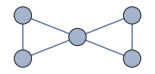
```mathematica
g=-Graphics-;
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},VertexLabels->"Name"]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},SelfLoops->True]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},SelfLoops->True,MultiEdges->True]
```

```mathematica
IGVertexContract[g,{{1,2,3},{4,5}},MultiEdges->True]
```

When using both SelfLoops→True and MultiEdges→True, the edge ordering is maintained relative to the input graph. This allows easily transferring edge weights, and combining them if necessary.

```mathematica
g=IGShorthand["a-b-c-d-a,a-c",
EdgeWeight->{1,2,3,4,5},EdgeLabels->"EdgeWeight"]
```

```mathematica
IGWeightedSimpleGraph[
IGVertexContract[g,{{"a","b"}},
SelfLoops->True,MultiEdges->True,
EdgeWeight->IGEdgeProp[EdgeWeight][g]
],
EdgeLabels->"EdgeWeight",VertexLabels->"Name"
]
```

#### IGConnectNeighborhood

```mathematica
?IGConnectNeighborhood
```

IGConnectNeighborhood[g,k] connects each vertex in g to its order k neighbourhood. This operation is also known as the k^th power of the graph.

IGConnectNeighborhood differs from the built-in GraphPower in that it preserves parallel edges and self-loops.

Warning: Most graph properties, such as edge weights, will be lost.

Connect each vertex to its second order neighbourhood:

```mathematica
IGConnectNeighborhood[CycleGraph[15]]
```

Connect each vertex to its third order neighbourhood:

```mathematica
IGConnectNeighborhood[GridGraph[{10,10}],3]
```

#### IGMycielskian

```mathematica
?IGMycielskian
```

IGMycielskian applies the Mycielski construction to an undirected graph on n≥2 vertices to obtain a larger graph (the Mycielskian) on 2 n+1 vertices. If the graph has less than 2 vertices, then instead of applying the standard Mycielski construction, IGMycielskian simply adds one vertex and one edge.

If the original graph has chromatic number k, its Mycielskian has chromatic number k+1. The Mycielski construction preserves the triangle-free property of the graph.

```mathematica
g=CycleGraph[4]
```

```mathematica
{IGChromaticNumber[g],IGTriangleFreeQ[g]}
```

```mathematica
mg=IGMycielskian[g]
```

```mathematica
{IGChromaticNumber[mg],IGTriangleFreeQ[mg]}
```

Construct triangle-free graphs with successively larger chromatic numbers.

```mathematica
NestList[IGMycielskian,IGEmptyGraph[],5]
```

```mathematica
IGChromaticNumber/@%
```

#### IGSmoothen

```mathematica
?IGSmoothen
```

IGSmoothen suppresses all degree-2 vertices, thus obtaining the smallest topologically equivalent (i.e. homeomorphic) graph. See also IGHomeomorphicQ.

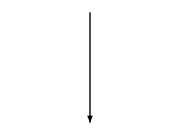
-Graphics-
-Graphics-
-Graphics-

The vertex names are preserved, and the weights of merged edges are summed up. All other graph properties are discarded. Edge directions are also discarded.

The smallest topological equivalent of a path graph consists of two connected vertices.

```mathematica
IGSmoothen[-Graphics-,VertexLabels->Automatic]
```

The result may contain self-loops. The smallest topological equivalent of a cycle graph is a single vertex with a self-loop.

```mathematica
IGSmoothen[CycleGraph[10]]
```

The result may also contain multi-edges.

```mathematica
IGSmoothen[-Graphics-,VertexLabels->Automatic]
```

The result is always a weighted graph. When contracting edges, their weights are added up. If the input graph was not weighted, all of its edge weights are considered to be 1. Thus, the graph distance of any two vertices in the result is always the same as it was in the input graph.

```mathematica
g=IGGiantComponent@RandomGraph[{100,100}]
```

```mathematica
tm=IGSmoothen[g]
```

```mathematica
IGEdgeWeightedQ[tm]
```

```mathematica
IGDistanceMatrix[g,VertexList[tm],VertexList[tm]]==IGDistanceMatrix[tm]
```

The result does not contain any degree-2 vertices.

```mathematica
Union@VertexDegree[tm]
```

The vertex coordinates, as well as any other graph properties are discarded.

```mathematica
g=IGMeshGraph@IGLatticeMesh["Hexagonal",{3,3}]
```

```mathematica
IGSmoothen[g]
```

Vertex coordinates can be transferred to the new graph as follows:

```mathematica
IGSmoothen[g,
VertexCoordinates->{v_:>PropertyValue[{g,v},VertexCoordinates]}]
```

Create a tree in which every non-leaf node has a degree of at least 3.

```mathematica
IGSmoothen[IGTreeGame[100],GraphLayout->"RadialEmbedding"]
```

Let us compute the effective resistance of a resistor network by repeated smoothing (merger of resistors in series) and simplification (merger of resistors in parallel). Resistances are stored as edge weights. A zero-resistance input and output terminal is added to prevent the premature smoothing of these points.

```mathematica
resistorGrid=-Graphics-;
```

Merge resistors in series ...

```mathematica
reducedGrid=IGSmoothen[resistorGrid]
```

... then merge resistors in parallel and check the resulting edge weights.

```mathematica
reducedGrid=IGWeightedSimpleGraph[reducedGrid, 1/Total[1/{##}]&,EdgeLabels->"EdgeWeight"]
```

Repeat until a single resistor remains.

```mathematica
reducedGrid=IGSmoothen[reducedGrid]
```

```mathematica
reducedGrid=IGWeightedSimpleGraph[reducedGrid, 1/Total[1/{##}]&,EdgeLabels->"EdgeWeight"]
```

```mathematica
reducedGrid=IGSmoothen[reducedGrid,EdgeLabels->"EdgeWeight"]
```

```mathematica
IGEdgeProp[EdgeWeight][reducedGrid]
```

## Structural properties

### Centrality measures

#### Betweenness

```mathematica
?IGBetweenness
```

```mathematica
?IGBetweennessEstimate
```

```mathematica
?IGEdgeBetweenness
```

```mathematica
?IGEdgeBetweennessEstimate
```

Weighted graphs are supported by all betweenness functions in IGraph/M.

The betweenness of a vertex or edge is, roughly speaking, the number of shortest paths passing through it. More formally, the betweenness of vertex i is b_i=∑_(i≠s≠t) (g_(s,t)^(i))/(g_(s,t)), where g_(s,t) is the total number of shortest paths (geodesics) between vertices s and t, and g_(s,t)^(i) is the number of shortest paths between vertices s and t that pass through i.

Available options:

Method, see below. The default is "Precise". This method is currently only available for vertex betweenness calculations.

Normalized→True will compute the normalized betweenness by dividing the result by the number of (ordered or unordered) vertex pairs used in the shortest path calculation. Thus the normalization factor is (V-1) (V-2) for directed graphs and 1/2 (V-1) (V-2) for undirected graphs. The normalized value lies between 0 and 1.

Available Method options for vertex betweenness calculations:

"Precise" is accurate, but slow. This is the default.

"Fast" is fast, but may give incorrect results for large graphs with lots of shortest paths.

Compare the "Fast" and "Precise" methods:

```mathematica
g=GridGraph[{30,30}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

For this large grid graph, the "Fast" method no longer gives accurate results:

```mathematica
g=GridGraph[{40,40}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

Visualize the vertex and edge betweenness of a weighted geometrical graph, where weights represent Euclidean distances.

```mathematica
pts=RandomPoint[Disk[],100];
IGMeshGraph[
DelaunayMesh[pts],
EdgeStyle->Thick,VertexStyle->EdgeForm[None]
]//
IGVertexMap[
ColorData["SolarColors"],
VertexStyle->Rescale@*IGBetweenness
]/*
IGEdgeMap[
ColorData["SolarColors"],
EdgeStyle->Rescale@*IGEdgeBetweenness
]
```

Compute the betweenness of a subset of vertices.

```mathematica
g=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}];
```

```mathematica
Take[VertexList[g],5]
```

```mathematica
IGBetweenness[g,%]
```

Visualize the betweenness of a periodic grid with slightly randomized edge weights.

```mathematica
n=40;
IGSquareLattice[{n,n},
"Periodic"->True,
VertexCoordinates->Tuples[Range[n],{2}],
EdgeWeight->{_:>RandomReal[{.99,1.01}]},
GraphStyle->"BasicBlack",
EdgeShapeFunction->None,
VertexSize->1
]//IGVertexMap[
ColorData["BlueGreenYellow"],
VertexStyle->Rescale@*IGBetweenness
]
```

Possible issues:

Weighted betweenness calculations may be affected by numerical precision when non-integer weights are used. Betweenness computations count shortest paths, which means that the total weight of different paths must be compared for equality.  Equality testing with floating point numbers is unreliable.  This can be demonstrated on an example which is purposefully constructed to be problematic.

An unweighted grid graph has many shortest paths between the same pair of vertices.

```mathematica
g=GridGraph[{6,6}];
```

Let us construct non-integer weights which can add up to (equal) integers in many different ways.

```mathematica
weights=1/RandomInteger[{1,5},EdgeCount[g]];
```

Let us now associate weights with edges and order the edges in two different random ways. Betweenness should not depend on edge ordering, so graphs constructed from both should have the same betweenness values.

```mathematica
asc1=Association@RandomSample@Thread[EdgeList[g]->weights];
asc2=Association@RandomSample@Thread[EdgeList[g]->weights];
```

```mathematica
g1=Graph[Keys[asc1],EdgeWeight->Values[asc1]];
g2=Graph[Keys[asc2],EdgeWeight->Values[asc2]];
```

```mathematica
KeySort@AssociationThread[VertexList[g1],IGBetweenness[g1]]-
KeySort@AssociationThread[VertexList[g2],IGBetweenness[g2]]
```

```mathematica
Max@Abs[%]
```

Yet the results differ. This is because IGraph/M works with floating point numbers. Even when different sums of exact weights happen to be equal, floating point calculations will give slightly different results.

To obtain a reliable result, we must use integer weights. The weights in these example were inverses of {1,2,3,4,5}. Multiplying these by their least common multiple will always yield an integer.

```mathematica
LCM@@{1,2,3,4,5}
```

```mathematica
asc1=Association@RandomSample@Thread[EdgeList[g]->60weights];
asc2=Association@RandomSample@Thread[EdgeList[g]->60weights];
```

```mathematica
g1=Graph[Keys[asc1],EdgeWeight->Values[asc1]];
g2=Graph[Keys[asc2],EdgeWeight->Values[asc2]];
```

```mathematica
KeySort@AssociationThread[VertexList[g1],IGBetweenness[g1]]-
KeySort@AssociationThread[VertexList[g2],IGBetweenness[g2]]
```

```mathematica
Chop@Max@Abs[%]
```

Now IGBetweenness gives the same result regardless of edge ordering.

#### Closeness

```mathematica
?IGCloseness
```

```mathematica
?IGClosenessEstimate
```

The normalized closeness centrality of a vertex is the inverse average shortest path length to other vertices.

Weighted graphs are supported.

Available options:

Normalized→True will normalize values by the number of vertices minus one. Effectively, this computes closeness as the reciprocal of the average distance to all other nodes. Normalized→False uses the sum (instead of the average) of distances to all other nodes. The default is False for consistency with igraph interfaces in other languages.

igraph’s closeness calculation differs from Mathematica’s in that when there is no path connecting two vertices, the total number of vertices is used as their distance (a number larger than any other distance in an unweighted graph). Mathematica computes closeness separately within each connected component.

Visualize the closeness of nodes in a weighted geometrical graph where weights correspond to Euclidean distances.

```mathematica
pts=RandomPoint[Polygon@CirclePoints[3],75];
IGVertexMap[
ColorData["Rainbow"],
VertexStyle->Rescale@*IGCloseness,
IGMeshGraph[DelaunayMesh[pts],GraphStyle->"BasicBlack"]
]
```

Indeterminate is returned for a single-vertex graph.

```mathematica
IGCloseness@IGEmptyGraph[1]
```

#### PageRank

```mathematica
?IGPageRank
```

```mathematica
?IGPersonalizedPageRank
```

Weighted graphs and multigraphs are supported.

The default damping factor is 0.85.

The following Method options are available:

"PowerIteration", deprecated, not recommended. Takes suboptions "MaxIterations" and "Epsilon". Does not support weights or multigraphs.

"Arnoldi" uses ARPACK

"PRPACK" uses PRPACK. It is the default method.

#### Eigenvector centrality

```mathematica
?IGEigenvectorCentrality
```

Weighted graphs are supported.

The available options are:

Normaized→True will scale the result so that the maximum centrality is 1. The default is True.

DirectedEdges→False ignores edge directions.

#### Kleinberg’s hub and authority scores

```mathematica
?IGHubScore
```

```mathematica
?IGAuthorityScore
```

Weighted graphs are supported.

The available options are:

Normalized→True scales the result so that the maximum centrality is 1. The default is True.

#### Burt’s constraint score

```mathematica
?IGConstraintScore
```

Weighted graphs are supported.

### Centralization

```mathematica
?IG*Centralization
```

Centralization is computed from centrality values in a way equivalent to Total[Max[centralities]-centralities]. With the (default) option Normalized→True, the result is normalized by dividing it by the highest value it can achieve for a graph of the same directedness on the same number of vertices.

```mathematica
g=IGBarabasiAlbertGame[100,2,DirectedEdges->False];
```

```mathematica
IGBetweennessCentralization[g]
```

```mathematica
IGClosenessCentralization[g]
```

```mathematica
IGDegreeCentralization[g]
```

```mathematica
IGEigenvectorCentralization[g]
```

### Topological sorting and acyclic graphs

```mathematica
?IGFeedbackArcSet
```

```mathematica
?IGDirectedAcyclicGraphQ
```

```mathematica
?IGTopologicalOrdering
```

IGFeedbackArcSet[] returns a set of directed edges (also called arcs) the removal of which makes the graph acyclic.

With Method→"IntegerProgramming", it finds an exact minimal feedback arc set through integer programming using the triangle inequality formulation. With Method→"EadesLinSmyth", it finds a feedback arc set (not necessarily minimal) using the fast heuristic of Eades, Lin and Smyth (1993).

The following directed graph is not acyclic.

```mathematica
g=RandomGraph[{10,20},DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
{AcyclicGraphQ[%],IGDirectedAcyclicGraphQ[%]}
```

Removing these edges breaks all cycles.

```mathematica
IGFeedbackArcSet[g]
```

```mathematica
ag=EdgeDelete[g,%]
```

```mathematica
IGDirectedAcyclicGraphQ[ag]
```

Vertices of a directed acyclic graph can be sorted topologically. IGTopologicalOrdering returns a permutation that sorts them this way, and thus makes the graph’s adjacency matrix upper triangular.

```mathematica
perm=IGTopologicalOrdering[ag]
```

```mathematica
With[{am=AdjacencyMatrix[ag]},
ArrayPlot/@{am,am[[perm,perm]]}
]
```

##### References

P. Eades, X. Lin, and W. F. Smyth, A fast and effective heuristic for the feedback arc set problem, Inf. Process. Lett. 47, 319 (1993).

### Chordal graphs

#### IGChordalQ

```mathematica
?IGChordalQ
```

A graph is chordal if each of its cycles of four or more nodes has a chord, i.e. an edge joining two non-adjacent vertices in the cycle. Equivalently, all chordless cycles in a chordal graph have at most 3 vertices.

Chordal graphs are also called rigid circuit graphs or triangulated graphs.

Grid graphs are not chordal because they have chordless 4 cycles.

```mathematica
g=GridGraph[{2,3},VertexLabels->"Name"]
```

```mathematica
IGChordalQ[g]
```

Adding chords to the 4 cycles makes them chordal.

```mathematica
EdgeAdd[g,{1<->4,4<->5}]
```

```mathematica
IGChordalQ[%]
```

#### IGChordalCompletion

```mathematica
?IGChordalCompletion
```

IGChordalCompletion computes a set of edges that, when added to a graph, make it chordal. The edge set returned is not usually minimal, i.e. some of the edges may not be necessary to create a chordal graph.

```mathematica
g=CycleGraph[5]
```

```mathematica
completion=IGChordalCompletion[g];
HighlightGraph[EdgeAdd[g,completion],completion]
```

#### IGMaximumCardinalitySearch

```mathematica
?IGMaximumCardinalitySearch
```

The maximum cardinality search algorithm visits the vertices of the graph in such an order so that every time the vertex with the most already visited neighbours is visited next. The visiting order is animated below:

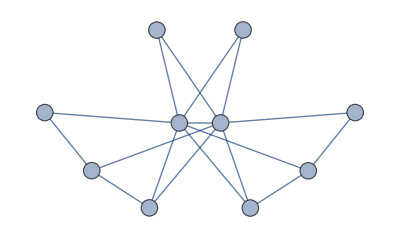
```mathematica
g=-Graphics-;
```

```mathematica
seq=InversePermutation@IGMaximumCardinalitySearch[g]
```

```mathematica
Table[
HighlightGraph[
Graph[g,VertexLabels->"Name"],
Take[seq,-i]
],
{i,1,10}
]//ListAnimate
```

### Clustering coefficient

```mathematica
?IG*ClusteringCoefficient
```

Clustering coefficients are measures of the degree to which vertices in a graph tend to cluster together. They are also referred to as transitivity, as they measure how often two vertices that are connected through a third one are also directly connected.

All clustering coefficient calculations in IGraph/M ignore edge directions.

#### IGGlobalClusteringCoefficient

```mathematica
?IGGlobalClusteringCoefficient
```

The clustering coefficient of an undirected graph is defined as

C=(number of closed ordered triplets)/(number of connected ordered triplets)

The available options are:

"ExcludeIsolates"→True will cause Indeterminate to be returned if the graph has no connected triplets. With the default "ExcludeIsolates"→False, 0 is returned.

The following graph has 10 connected ordered triplets, namely {3, 1, 2}, {2, 1, 3}, {1, 2, 3}, {3, 2, 1}, {2, 3, 1}, {2, 3, 4}, {1, 3, 4}, {1, 3, 2}, {4, 3, 2}, {4, 3, 1}. Out of these, only 6 are closed: {1, 3, 2}, {1, 2, 3}, {2, 1, 3}, {2, 3, 1}, {3, 2, 1}, {3, 1, 2}. Thus the clustering coefficient is 6/10=0.6.

```mathematica
IGGlobalClusteringCoefficient[-Graphics-]
```

#### IGLocalClusteringCoefficient

```mathematica
?IGLocalClusteringCoefficient
```

The local clustering coefficient of a vertex is defined as

C=(number of connected pairs of neighbours)/(total number of pairs of neighbours)

The available options are:

"ExcludeIsolates"→True will cause Indeterminate to be returned for degree 0 and degree 1 vertices. With the default "ExcludeIsolates"→False, 0 is returned.

In the following graph, vertex 4 has only one neighbour. Thus its local clustering coefficient will be computed as either 0 or indeterminate depending on the setting for "ExcludeIsolates".

```mathematica
IGLocalClusteringCoefficient[-Graphics-]
```

```mathematica
IGLocalClusteringCoefficient[-Graphics-,"ExcludeIsolates"->True]
```

#### IGAverageLocalClusteringCoefficient

```mathematica
?IGAverageLocalClusteringCoefficient
```

The available options are:

"ExcludeIsolates"→True will cause degree 0 and degree 1 vertices to be excluded from the calculation.

With "ExcludeIsolates"→True, the local clustering coefficient of vertex 4 will be excluded from the calculation of the average.

```mathematica
{IGAverageLocalClusteringCoefficient[-Graphics-],
IGAverageLocalClusteringCoefficient[-Graphics-,"ExcludeIsolates"->True]}
```

#### IGWeightedClusteringCoefficient

```mathematica
?IGWeightedClusteringCoefficient
```

IGWeightedClusteringCoefficient computes the weighted local clustering coefficient, as defined by A. Barrat et al. (2004) http://arxiv.org/abs/cond-mat/0311416 . This function expects a weighted graph as input.

The available options are:

"ExcludeIsolates"→True will cause Indeterminate to be returned for degree 0 and degree 1 vertices. With the default "ExcludeIsolates"→False, 0 is returned.

### Shortest paths

The length of a path between two vertices is the number of edges the path consists of. Functions that use edge weights consider the path length to be the sum of edge weights along the path.

#### IGDistanceMatrix

```mathematica
?IGDistanceMatrix
```

IGDistanceMatrix takes the following Method options:

Automatic selects a method automatically. As of version 0.3.0, "Unweighted" is selected for unweighted graphs, "Dijkstra" for weighted graphs with only positive weights, and "Johnson" otherwise.

"Unweighted" ignores weights

"Dijkstra" uses Dijkstra’s algorithm. All weights must be non-negative.

"BellmanFord" uses the Bellman–Ford algorithm. Negative weights are supported but all cycles must have a non-negative total weight.

"Johnson" uses the Johnson algorithm. Negative weights are supported but all cycles must have a non-negative total weight.

The igraph C core may override explicit method settings when appropriate. For example, if the graph is not weighted, it always uses "Unweighted".

#### IGDistanceCounts

```mathematica
?IGDistanceCounts
```

IGDistanceCounts[graph] counts all-pair unweighted shortest path lengths in the graph.
IGDistanceCounts[graph, {v_1,v_2,…}] counts unweighted shortest path lengths for paths starting at the given vertices.

For weighted path lengths, or to restrict the computation to both certain start and end vertex sets, use IGDistanceHistogram[].

Compute how the shortest path length distribution changes as we rewire a grid graph k times.

```mathematica
Table[
ListPlot[
Normalize[IGDistanceCounts@IGRewire[GridGraph[{50,50}],k],Total],
Joined->True,Filling->Bottom,PlotLabel->StringTemplate["rewiring steps: ``"][k]
],
{k,{0,5,10,20,50,100}}
]
```

#### IGNeighborhoodSize

```mathematica
?IGNeighborhoodSize
```

#### IGDistanceHistogram

```mathematica
?IGDistanceHistogram
```

IGDistanceHistogram[] computes the weighted shortest path length histogram between the specified start and end vertex sets. The start and end vertex sets do not need to be the same. Note that if the graph is undirected, path lengths between s and t will be double counted (from s→t and t→s) if s and t appear both in the starting and ending vertex sets.

IGDistanceHistogram[] is useful when the result of IGDistanceMatrix[] (or GraphDistanceMatrix[]) does not fit in memory.

#### IGAveragePathLength

```mathematica
?IGAveragePathLength
```

If the graph is unconnected, vertex pairs between which there is no path are excluded from the calculation. This is different from the behaviour of MeanGraphDistance[], which returns ∞ in this case.

#### IGGirth

```mathematica
?IGGirth
```

```mathematica
IGGirth[-Graphics-]
```

#### IGDiameter and IGFindDiameter

```mathematica
?IGDiameter
```

The diameter of a graph is the length of the longest shortest path between any two vertices.

The available options are:

Method can take the values "Unweighted", "Dijkstra" or Automatic. "Dijkstra" takes edge weights into account. Automatic chooses based on whether the graph is weighted.

"ByComponents" controls how unconnected graphs are handled. If False, Infinity is returned. If True, the largest diameter within a component is returned.

```mathematica
IGDiameter[-Graphics-]
```

```mathematica
?IGFindDiameter
```

```mathematica
IGFindDiameter[-Graphics-]
```

```mathematica
g=Entity["Graph","DodecahedralGraph"]["Graph"];
```

```mathematica
HighlightGraph[g,PathGraph@IGFindDiameter[g],
GraphHighlightStyle->"DehighlightFade",PlotTheme->"RoyalColor"
]
```

#### IGEccentricity

```mathematica
?IGEccentricity
```

The eccentricity of a vertex is the longest shortest path to any other vertex. IGEccentricity computes the unweighted eccentricity of each vertex within the connected component where it is contained.

```mathematica
IGEccentricity@CycleGraph[8]
```

#### IGRadius

```mathematica
?IGRadius
```

The radius of a graph is the smallest eccentricity of any of its vertices.

For unconnected graphs, 0 is returned.

#### IGVoronoiCells

```mathematica
?IGVoronoiCells
```

IGVoronoiCells[graph, centers] partitions a graph’s vertices into groups based on which given centre vertex they are the closest to. Edge weights are considered for the distance calculations.

Available options:

"Tiebreaker" sets the function used to decide which cell a vertex should belong to if its distance to several different centres is equal. The default is to use the first qualifying cell. Possible useful settings are First, Last, RandomChoice.

```mathematica
g=PathGraph[Range[5],VertexLabels->"Name",VertexSize->Medium]
```

```mathematica
IGVoronoiCells[g,{2,4}]
```

```mathematica
HighlightGraph[g,Values[%]]
```

In the event of a tie, a vertex is added to the first qualifying cell. The tiebreaker function can be changed as below.

```mathematica
IGVoronoiCells[g,{2,4},"Tiebreaker"->Last]
```

```mathematica
Table[IGVoronoiCells[g,{2,4},"Tiebreaker"->RandomChoice],{5}]
```

Find Voronoi cells on a grid.

```mathematica
g=GridGraph[{10,10},VertexSize->Medium,GraphStyle->"BasicBlack"];
centers=RandomSample[VertexList[g],3];
HighlightGraph[g,
Append[
Subgraph[g,#]&/@Values@IGVoronoiCells[g,centers],
Style[centers,Black]
],
GraphHighlightStyle->"DehighlightHide"
]
```

Edge weights are interpreted as distances.

```mathematica
g=IGMeshGraph@DelaunayMesh@RandomPoint[Disk[],200];
centers=RandomSample[VertexList[g],3];
HighlightGraph[g,
Append[
Subgraph[g,#]&/@Values@IGVoronoiCells[g,centers],
Style[centers,Black]
],
GraphHighlightStyle->"DehighlightGray"
]
```

### Bipartite graphs

```mathematica
?IGBipartite*
```

#### IGBipartiteQ

```mathematica
?IGBipartiteQ
```

Generate a graph and verify that it is bipartite.

```mathematica
g=IGBipartiteGameGNM[5,5,10,VertexLabels->"Name"]
```

```mathematica
IGBipartiteQ[g]
```

Verify that no edges run between two disjoint vertex subsets of the graph.

```mathematica
IGBipartiteQ[g,{{1,2,3},{6,7,8}}]
```

#### IGBipartitePartitions

```mathematica
?IGBipartitePartitions
```

Find a bipartite partitioning of a graph.

```mathematica
g=-Graphics-;
```

```mathematica
IGBipartitePartitions[g]
```

Ensure that the partitions are returned in such an order that the first one contains vertex 5.

```mathematica
IGBipartitePartitions[g,5]
```

$Failed is returned for non-bipartite graphs.

```mathematica
IGBipartitePartitions[CompleteGraph[4]]
```

We can use IGPartitionsToMembership or IGKVertexColoring[…,2] to obtain a partition index for each vertex.

```mathematica
IGPartitionsToMembership[g]@IGBipartitePartitions[g]
```

```mathematica
IGKVertexColoring[g,2]
```

#### IGBipartiteProjections

```mathematica
?IGBipartiteProjections
```

The following bipartite graph described the relationship between diseases and genes.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}]
```

```mathematica
parts=Values@GroupBy[
Thread[IGVertexProp["Type"][g]->VertexList[g]],
First->Last
];
```

Construct a disease-disease and gene-gene network from it.

```mathematica
IGBipartiteProjections[g,parts]
```

#### IGBipartiteIncidenceMatrix and IGBipartiteIncidenceGraph

```mathematica
?IGBipartiteIncidenceGraph
```

```mathematica
?IGBipartiteIncidenceMatrix
```

Compute an incidence matrix. The default partitioning used by IGBipartiteIncidenceMatrix is the one returned by IGBipartitePartitions.

```mathematica
g=IGBipartiteGameGNM[5,5,10,VertexLabels->"Name"]
```

```mathematica
bm=IGBipartiteIncidenceMatrix[g];
MatrixForm[bm,TableHeadings->IGBipartitePartitions[g]]
```

Reconstruct a graph from an incidence matrix.

```mathematica
IGBipartiteIncidenceGraph[bm,VertexLabels->"Name",GraphLayout->"BipartiteEmbedding"]
```

Compute an incidence matrix using a given partitioning / vertex ordering. It is allowed to pass only a subset of vertices.

```mathematica
IGBipartiteIncidenceMatrix[g,{{1,2,3},{6,7,8}}]
```

Reconstruct the bipartite graph while specifying vertex names.

```mathematica
IGBipartiteIncidenceGraph[{{a,b,c},{d,e,f}},%,VertexLabels->"Name"]
```

### Similarity measures

```mathematica
?IGBibliographicCoupling
```

The bibliographic coupling of two vertices in a directed graph is the number of other vertices they both connect to. The bibliographic coupling matrix can also be obtained using IGZeroDiagonal[am.amᵀ], where am is the adjacency matrix of the graph.

```mathematica
?IGCocitationCoupling
```

The co-citation coupling of two vertices in a directed graph is the number of other vertices that connect to both of them. The co-citation coupling matrix can also be obtained using IGZeroDiagonal[amᵀ.am], where am is the adjacency matrix of the graph.

```mathematica
?IGDiceSimilarity
```

The Dice similarity coefficient of two vertices is twice the number of common neighbours divided by the sum of the degrees of the vertices.

```mathematica
?IGJaccardSimilarity
```

The Jaccard similarity coefficient of two vertices is the number of common neighbours divided by the number of vertices that are neighbours of at least one of the two vertices being considered.

```mathematica
?IGInverseLogWeightedSimilarity
```

The inverse log-weighted similarity of two vertices is the number of their common neighbours, weighted by the inverse logarithm of their degrees. It is based on the assumption that two vertices should be considered more similar if they share a low-degree common neighbour, since high-degree common neighbours are more likely to appear even by pure chance.

Isolated vertices will have zero similarity to any other vertex. Self-similarities are not calculated.

##### References

Lada A. Adamic and Eytan Adar: Friends and neighbors on the Web, Social Networks, 25(3):211-230, 2003.

### Connectivity and graph components

#### IGConnectedQ and IGWeaklyConnectedQ

```mathematica
?IGConnectedQ
```

```mathematica
?IGWeaklyConnectedQ
```

IGConnectedQ checks if the graph is (strongly) connected. It is equivalent to ConnectedGraphQ. IGWeaklyConnectedQ check if a directed graph is weakly connected. It is equivalent to WeaklyConnectedGraphQ. Both of these functions use the implementation from the core igraph library, and will always be consistent with it for edge cases such as the null graph.

This graph is connected.

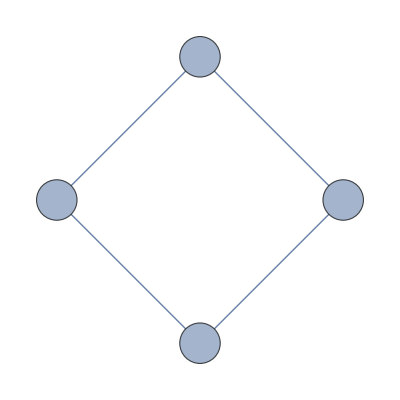
```mathematica
IGConnectedQ[-Graphics-]
```

This directed graph is only weakly connected.

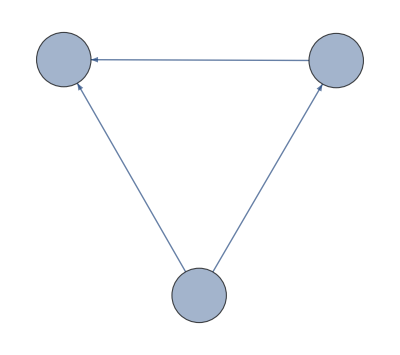
```mathematica
IGConnectedQ[-Graphics-]
```

```mathematica
IGWeaklyConnectedQ[-Graphics-]
```

The null graph is considered connected by convention.

```mathematica
IGConnectedQ@IGEmptyGraph[0]
```

#### IGConnectedComponentSizes and IGWeaklyConnectedComponentSizes

```mathematica
?IGConnectedComponentSizes
```

```mathematica
?IGWeaklyConnectedComponentSizes
```

IGWeaklyConnectedComponentsSizes and IGConnectedComponentSizes return the sizes of the graph’s weakly or strongly connected components in decreasing order.

In large graphs, these functions will be faster than the equivalent Length/@ConnectedComponents[g].

The emergence of a giant component as the number of edges in a random graph increases.

```mathematica
Table[
{m,First@IGConnectedComponentSizes@RandomGraph[{1000,m}]},
{m,5,2000,5}
]//ListPlot
```

The number of weakly and strongly connected components versus the number of edges in a random directed graph.

```mathematica
Table[
With[{g=RandomGraph[{1000,m},DirectedEdges->True]},
{{m,Length@IGWeaklyConnectedComponentSizes[g]},{m,Length@IGConnectedComponentSizes[g]}}
],
{m,5,3000,5}
]//Transpose//ListPlot
```

#### Vertex separators

A vertex separator is a set of vertices whose removal disconnects the graph.

```mathematica
?IGMinimalSeparators
```

```mathematica
?IGMinimumSeparators
```

```mathematica
?IGVertexSeparatorQ
```

```mathematica
?IGMinimalVertexSeparatorQ
```

```mathematica
g=ExampleData[{"NetworkGraph","Friendship"}]
```

```mathematica
separators=IGMinimumSeparators[g]
```

Removing any of these vertex sets will disconnect the graph:

```mathematica
VertexDelete[g,#]&/@separators
```

```mathematica
IGVertexSeparatorQ[g,#]&/@separators
```

```mathematica
IGMinimalVertexSeparatorQ[g,#]&/@separators
```

Removing Anna, Nora and Larry also disconnects the graph, thus this vertex set is a separator:

```mathematica
IGVertexSeparatorQ[g,{"Anna","Nora","Larry"}]
```

But it is not minimal:

```mathematica
IGMinimalVertexSeparatorQ[g,{"Anna","Nora","Larry"}]
```

IGMinimumSeparators returns only those vertex separators which are of the smallest possible size in the graph. IGMinimalSeparators returns all separators which cannot be made smaller by removing a vertex from them. The former is a subset of the latter.

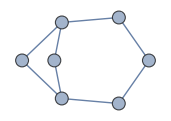
```mathematica
g=-Graphics-;
```

```mathematica
IGMinimalSeparators[g]
```

```mathematica
IGMinimumSeparators[g]
```

```mathematica
SubsetQ[%%,%]
```

#### IGEdgeConnectivity

```mathematica
?IGEdgeConnectivity
```

IGEdgeConnectivity ignores edge weights. To take edge weights into account, use IGMinimumCutValue instead.

Compute the edge connectivity of the dodecahedral graph.

```mathematica
IGEdgeConnectivity[GraphData["DodecahedralGraph"]]
```

The edge connectivity of the singleton graph is returned as 0.

```mathematica
IGEdgeConnectivity[IGEmptyGraph[1]]
```

#### IGVertexConnectivity

```mathematica
?IGVertexConnectivity
```

According to Steinitz’s theorem, the skeleton of every convex polyhedron is a 3-vertex-connected planar graph.

```mathematica
g=GraphData["DodecahedralGraph"]
```

```mathematica
IGVertexConnectivity[g]
```

To find the specific vertex sets that disconnect the graph, use IGMinimumSeparators or IGMinimalSeparators.

```mathematica
IGMinimumSeparators[g]
```

The vertex connectivity of the singleton graph is returned as 0.

```mathematica
IGVertexConnectivity[IGEmptyGraph[1]]
```

#### IGBiconnectedQ

```mathematica
?IGBiconnectedQ
```

IGBiconnectedQ checks if a graph is biconnected. Edge directions are ignored.

```mathematica
IGBiconnectedQ[-Graphics-]
```

Since IGBiconnectedComponents does not return any isolated vertices, Length@IGBiconnectedComponents[g]==1 cannot be used to check if a graph is biconnected. Use IGBiconnectedQ instead.

```mathematica
IGBiconnectedComponents[-Graphics-]
```

The singleton graph is not considered to be biconnected, but the two-vertex complete graph is.

```mathematica
Table[IGBiconnectedQ@CompleteGraph[k],{k,1,2}]
```

#### IGBiconnectedComponents and IGBiconnectedEdgeComponents

```mathematica
?IGBiconnectedComponents
```

```mathematica
?IGBiconnectedEdgeComponents
```

IGBiconnectedCompoments returns the vertices of the maximal biconnected components of the graph. IGBiconnectedEdgeComponents returns the edges of the components. Edge directions are ignored and isolated vertices are excluded.

IGBiconnectedComponents is equivalent to KVertexConnectedComponents[…,2], except that isolated vertices are not returned as individual components.

The articulation vertices will be part of more than a single component, thus the biconnected components are not disjoint subsets of the vertex set.

```mathematica
IGBiconnectedComponents[-Graphics-]
```

However, each edge is part of precisely one biconnected components.

```mathematica
IGBiconnectedEdgeComponents[-Graphics-]
```

Thus, visualizing biconnected components is best done by colouring the edges, not the vertices.

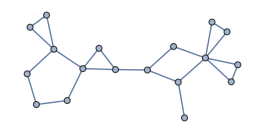
```mathematica
g=-Graphics-;
```

```mathematica
HighlightGraph[g,IGBiconnectedEdgeComponents[g],GraphStyle->"ThickEdge"]
```

#### IGArticulationPoints

```mathematica
?IGArticulationPoints
```

IGArticulationPoints finds vertices whose removal increases the number of (weakly) connected components in the graph. Edge directions are ignored.

```mathematica
g=Graph[{1->2,2->3,3->1,3->4,4->5,5->6,6->4},DirectedEdges->False,VertexLabels->Automatic]
```

```mathematica
IGArticulationPoints[g]
```

```mathematica
VertexDelete[g,#]&/@%
```

Articulation points are also size-1 separators.

```mathematica
IGMinimumSeparators[g]
```

Highlight the articulation points of a cactus graph.

```mathematica
g=-Graphics-;
```

```mathematica
HighlightGraph[g,IGArticulationPoints[g]]
```

Compute the block-cut tree of a connected graph. The blocks are the biconnected components. Together with the articulation vertices they form a bipartite graph, specifically a tree.

```mathematica
RelationGraph[
MemberQ,
Join[IGBiconnectedComponents[g],IGArticulationPoints[g]],
DirectedEdges->False,
GraphStyle->"ClassicDiagram",
VertexSize->{3,1}/7,VertexLabelStyle->8
]
```

#### IGBridges

```mathematica
?IGBridges
```

A bridge is an edge whose removal disconnects the graph (or increases the number of connected components if the graph was already disconnected). Edge directions are ignored.

```mathematica
IGShorthand["1-2-3-1-4-5-6-4"]
```

```mathematica
IGBridges[%]
```

Highlight bridges in a network.

```mathematica
g=ExampleData[{"NetworkGraph","FlorentineFamilies"}];
HighlightGraph[g,IGBridges[g]]
```

#### IGSourceVertexList and IGSinkVertexList

```mathematica
?IGSourceVertexList
```

```mathematica
?IGSinkVertexList
```

Find and highlight the source and sink vertices of a random acyclic graph.

```mathematica
g=DirectedGraph[RandomGraph[{10,20}],"Acyclic",VertexLabels->"Name",VertexSize->Large,EdgeStyle->Gray]
```

```mathematica
IGSourceVertexList[g]
```

```mathematica
IGSinkVertexList[g]
```

```mathematica
HighlightGraph[g,{IGSourceVertexList[g],IGSinkVertexList[g]}]
```

Undirected graphs have neither source nor sink vertices because undirected edges are counted as bidirectional.

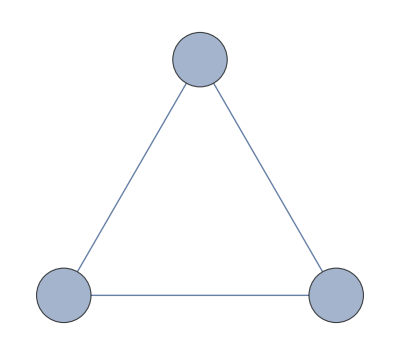
```mathematica
IGSourceVertexList[-Graphics-]
```

The exception is isolated vertices, which are counted both as sources and sinks.

```mathematica
Through[{IGSourceVertexList,IGSinkVertexList}@Graph[{1,2},{}]]
```

These are merely convenience functions that can be implemented straightforwardly as

```mathematica
Pick[VertexList[g],VertexOutDegree[g],0]
```

#### IGGiantComponent

```mathematica
?IGGiantComponent
```

IGGiantComponent is a convenience function that returns the largest weakly connected component of graph. If there are multiple components of largest size, there is no guarantee about which one would be returned. If this is a concern, use WeaklyConnectedComponents or WeaklyConnectedGraphComponents instead.

```mathematica
g=RandomGraph[{200,200}];
HighlightGraph[
g,
IGGiantComponent[g]
]//IGLayoutFruchtermanReingold
```

IGGiantComponent takes all standard graph options.

```mathematica
IGGiantComponent[g,GraphStyle->"BasicGreen",GraphLayout->"SpringEmbedding"]
```

Size of the giant component of a random subgraph of a grid graph.

```mathematica
g=IGSquareLattice[{30,30},"Periodic"->True];
Table[
{k,VertexCount@IGGiantComponent@Subgraph[g,RandomSample[VertexList[g],k]]},
{k,1,VertexCount[g],1}
]//ListPlot
```

### Trees

#### IGTreeQ

```mathematica
?IGTreeQ
```

IGTreeQ checks if a graph is a tree. An undirected tree is a connected graph with no cycles. A directed tree is similar, with its edges oriented either away from a root vertex (out-tree or arborescence) or towards a root vertex (in-tree or anti-arborescence).

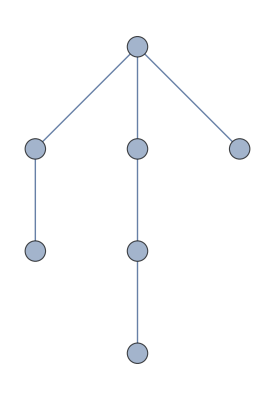
```mathematica
IGTreeQ[-Graphics-]
```

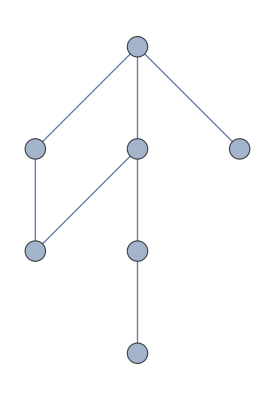
```mathematica
IGTreeQ[-Graphics-]
```

By convention, the null graph is not a tree.

```mathematica
IGTreeQ[IGEmptyGraph[0]]
```

This is an out-tree.

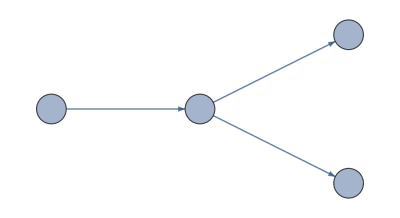
```mathematica
IGTreeQ[-Graphics-]
```

It is not also an in-tree.

```mathematica
IGTreeQ[-Graphics-,"In"]
```

It becomes an in-tree if we reverse its edges.

```mathematica
IGTreeQ[ReverseGraph[-Graphics-],"In"]
```

This graph is neither an out-tree nor an in-tree.

```mathematica
IGTreeQ[-Graphics-]
```

However, it becomes a tree if we ignore edge directions.

```mathematica
IGTreeQ[-Graphics-,"All"]
```

#### IGForestQ

```mathematica
?IGForestQ
```

IGForestQ is a convenience function that tests if all connected components of a graph are trees.

This graph is not a tree, but it is a forest.

```mathematica
Through[{IGTreeQ,IGForestQ}[-Graphics-]]
```

By convention, the null graph is not a tree, but it is a forest.

```mathematica
{IGTreeQ[IGEmptyGraph[0]],IGForestQ[IGEmptyGraph[0]]}
```

Use the second argument to test for forests of out-trees or in-trees. By default, directed graphs are checked to be out-forests.

```mathematica
g=IGShorthand["1->2<-3, 4<-5->6"]
```

```mathematica
{IGForestQ[g],IGForestQ[g,"Out"],IGForestQ[g,"In"],IGForestQ[g,"All"]}
```

#### IGStrahlerNumber

```mathematica
?IGStrahlerNumber
```

IGStrahlerNumber computes the Horton–Strahler index of each vertex in a rooted tree. The tree must be directed—this is how the root is encoded. The Horton–Strahler index of the tree itself is the index of the root, i.e. the largest returned index. This measure is also called stream order, as it was originally used to characterize river networks.

```mathematica
tree=IGTreeGame[30,DirectedEdges->True,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
IGVertexMap[#&,VertexLabels->IGStrahlerNumber,tree]
```

To get the Horton–Strahler number of the tree, find the maximal element.

```mathematica
Max@IGStrahlerNumber[tree]
```

IGStrahlerNumber requires a directed (i.e. rooted) tree as input.

```mathematica
IGStrahlerNumber[-Graphics-]
```

Orient undirected trees, effectively specifying a root vertex, before passing them to IGStrahlerNumber.

```mathematica
IGStrahlerNumber@IGOrientTree[-Graphics-,5]
```

#### IGTreelikeComponents

```mathematica
?IGTreelikeComponents
```

IGTreelikeComponents finds the tree-like components of an undirected graph by repeatedly identifying and removing degree-1 vertices. Vertices in the tree-like components are not part of any undirected cycle, nor are they on a path connecting vertices that belong to a cycle.

```mathematica
g=RandomGraph[{100,100}];
HighlightGraph[
g,
IGTreelikeComponents[g]
]//IGLayoutFruchtermanReingold
```

Highlight both the edges and vertices of tree-like components.

```mathematica
g=IGGiantComponent@RandomGraph[{50,50}];
HighlightGraph[
g,
Join[
Union@@(IncidenceList[g,#]&)/@IGTreelikeComponents[g],
IGTreelikeComponents[g]
]
]
```

```mathematica
IGLayoutFruchtermanReingold[%]
```

Remove tree-like components.

```mathematica
VertexDelete[g,IGTreelikeComponents[g]]
```

Vertices incident to multi-edges or loop-edges are not part of tree-like components.

```mathematica
IGTreelikeComponents[-Graphics-]
```

#### IGFromPrufer

```mathematica
?IGFromPrufer
```

#### IGToPrufer

```mathematica
?IGToPrufer
```

### Spanning trees

#### IGSpanningTree

```mathematica
?IGSpanningTree
```

```mathematica
IGSpanningTree[RandomGraph[{8,20}],GraphStyle->"DiagramGold"]
```

Find the shortest set of paths connecting a set of points in the plane:

```mathematica
pts=RandomReal[1,{10,2}];
g=IGMeshGraph@DelaunayMesh[pts];
```

```mathematica
tree=IGSpanningTree[g,VertexCoordinates->pts]
```

The edge weights are preserved in the result.

```mathematica
IGEdgeWeightedQ[tree]
```

Compute the total path length.

```mathematica
Total@IGEdgeProp[EdgeWeight][tree]
```

Find a maximum spanning tree by negating the weights before running the algorithm.

```mathematica
IGSpanningTree[IGEdgeMap[Minus,EdgeWeight,g],VertexCoordinates->pts]
```

#### IGRandomSpanningTree

```mathematica
?IGRandomSpanningTree
```

IGRandomSpanningTree samples the spanning trees (or forests) of a graph uniformly by performing a loop-erased random walk. Edge directions are ignored.

If a spanning forest of the entire graph is requested using IGRandomSpanningTree[g], then the vertex names and ordering are preserved. If a spanning tree of only a single component is requested using IGRandomSpanningTree[{g, v}], then this is not the case.

Highlight a few random spanning trees of the Petersen graph.

```mathematica
g=PetersenGraph[];
HighlightGraph[g,#,GraphHighlightStyle->"Thick"]&/@IGRandomSpanningTree[g,9]
```

If the input is a multi-graph, each edge will be considered separately for the purpose of spanning tree calculations. Thus the following graph has not 3, but 5 different spanning trees. Two pairs of these are indistinguishable based on their adjacency matrix due to the indistinguishability of the two parallel 1<->2 edges. However, since all 5 spanning trees are generated with equal probability, two of the 3 adjacency matrices will appear twice as frequently as the third one.

```mathematica
g=IGShorthand["1-2-3-1,1-2",MultiEdges->True,ImageSize->Small]
```

```mathematica
IGRandomSpanningTree[g,10000]//CountsBy[AdjacencyMatrix]//KeySort//KeyMap[MatrixForm]
```

Edge directions are ignored for the purpose of spanning tree calculation. Thus the result may not be an out-tree.

```mathematica
IGRandomSpanningTree@WheelGraph[11,DirectedEdges->True]
```

Create mazes by taking random spanning trees of grid graphs.

```mathematica
g=GridGraph[{10,10},GraphStyle->"Web"];
HighlightGraph[g,IGRandomSpanningTree[g],GraphHighlightStyle->"DehighlightHide"]
```

```mathematica
g=GridGraph[{6,6,6},VertexCoordinates->Tuples[Range[6],{3}]];
HighlightGraph[g,IGRandomSpanningTree[g],GraphHighlightStyle->"DehighlightHide"]
```

Generate a random spanning tree of the component containing vertex 8.

```mathematica
IGRandomSpanningTree[{-Graphics-,8},VertexLabels->Automatic]
```

#### IGSpanningTreeCount

```mathematica
?IGSpanningTreeCount
```

IGSpanningTreeCount computes the number of spanning trees of a graph using Kirchhoff’s theorem. Multigraphs and directed graphs are supported.

```mathematica
IGSpanningTreeCount[-Graphics-]
```

The number of spanning trees of a directed graph, rooted in any vertex.

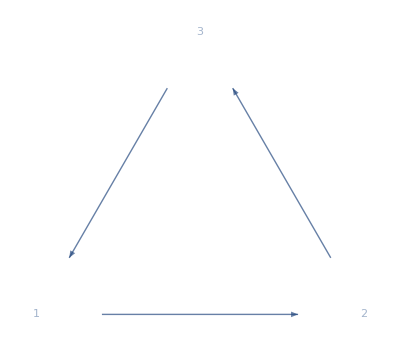
```mathematica
IGSpanningTreeCount[-Graphics-]
```

The number of spanning trees rooted in vertex 1.

```mathematica
IGSpanningTreeCount[-Graphics-,1]
```

```mathematica
IGSpanningTreeCount[PetersenGraph[]]
```

IGSpanningTreeCount works on large graphs.

```mathematica
g=HypercubeGraph[6]
```

```mathematica
IGSpanningTreeCount[g]
```

Edge multiplicities are taken into account. Thus the following graph has not 3, but 5 different spanning trees.

```mathematica
IGSpanningTreeCount[-Graphics-]
```

### Dominance

In a directed graph, a vertex d is said to dominate a vertex v if every path from the root to v passes through d. We say that d is an immediate dominator of v if it does not dominate any other dominator of v.

A dominator tree of a graph consists of the same vertices as the graph, and the children of a vertex are those other vertices which it immediately dominates.

#### IGDominatorTree

```mathematica
?IGDominatorTree
```

Find the dominator tree of a directed graph.

```mathematica
g=-Graphics-;
```

```mathematica
IGDominatorTree[g,"a",GraphStyle->"VintageDiagram"]
```

Vertices that cannot be reached from the specified root are left isolated in the returned graph.

```mathematica
IGDominatorTree[g,"b",GraphStyle->"VintageDiagram"]
```

IGDominatorTree accepts all standard Graph options.

```mathematica
IGDominatorTree[-Graphics-,8,
VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
```

#### IGImmediateDominators

```mathematica
?IGImmediateDominators
```

Directly find the immediate dominators of vertices in a graph.

```mathematica
g=-Graphics-;
IGImmediateDominators[g,"a"]
```

The immediate dominator of a vertex is its parent in the dominator tree.

```mathematica
tree=IGDominatorTree[g,"a",VertexLabels->Automatic]
```

```mathematica
IGAdjacencyList[tree,"In"]
```

Neither the root, nor vertices unreachable from the root are included in the keys of the returned association.

```mathematica
IGImmediateDominators[g,"b"]
```

### k-cores

```mathematica
?IGCoreness
```

A k-core of a graph is a maximal subgraph in which each vertex has degree at least k. The coreness of a vertex is the highest order of k-cores that contain it.

```mathematica
g=-Graphics-;
```

```mathematica
IGCoreness[g]
```

```mathematica
{KCoreComponents[g,2],KCoreComponents[g,3]}
```

By default, edge directions are ignored, and multi-edges are considered.

```mathematica
g=-Graphics-;
```

```mathematica
IGCoreness[g]
```

Use the second argument to consider only in- or out-degrees.

```mathematica
IGCoreness[g,"In"]
```

```mathematica
IGCoreness[g,"Out"]
```

### Matchings

#### IGMaximumMatching

```mathematica
?IGMaximumMatching
```

A matching of a graph is also known as an independent edge set.

IGMaximumMatching ignores edge directions and edge weights.

```mathematica
g=RandomGraph[{10,20}];
```

```mathematica
IGMaximumMatching[g]
```

```mathematica
HighlightGraph[g,IGMaximumMatching[g],GraphHighlightStyle->"Thick"]
```

#### IGMatchingNumber

```mathematica
?IGMatchingNumber
```

The matching number of a graph is the size of its maximum matchings.

### Graph traversal

#### IGUnfoldTree

```mathematica
?IGUnfoldTree
```

IGUnfoldTree creates a tree based on the breadth-first traversal of a graph. Each time a graph vertex is found, a new tree vertex is created.

Available options:

DirectedEdges→False will ignore edge directions in directed graphs. Otherwise, the search is done only along edge directions.

```mathematica
tree=IGUnfoldTree[-Graphics-,{1}]
```

The original vertex that generates a tree node is stored in the "OriginalVertex" property.

```mathematica
IGVertexProp["OriginalVertex"][tree]
```

We can label the tree nodes with the name of the original vertex either using pattern matching in VertexLabels along with PropertyValue …

```mathematica
IGLayoutReingoldTilford[
tree,
"RootVertices"->{1},VertexLabels->(v_:>PropertyValue[{tree,v},"OriginalVertex"])
]
```

… or using IGVertexMap.

```mathematica
IGLayoutReingoldTilford[tree,"RootVertices"->{1}]//IGVertexMap[#&,VertexLabels->IGVertexProp["OriginalVertex"]]
```

In directed graphs, the search is done along edge directions. It may be necessary to give multiple starting roots to fully unfold a weakly connected (or unconnected) graph.

```mathematica
IGUnfoldTree[Graph[{1->2,2->3}],{2,1}]//IGVertexMap[#&,VertexLabels->IGVertexProp["OriginalVertex"]]
```

Use DirectedEdges→False to ignore edge directions during the search. Edge directions are still preserved in the result.

```mathematica
IGUnfoldTree[Graph[{1->2,2->3}],{2},DirectedEdges->False]//IGVertexMap[#&,VertexLabels->IGVertexProp["OriginalVertex"]]
```

### Other properties

#### IGNullGraphQ

```mathematica
?IGNullGraphQ
```

IGNullGraphQ returns True only for the null graph, i.e. the graph that has no vertices.

```mathematica
IGNullGraphQ[IGEmptyGraph[]]
```

For graphs that have vertices, but no edges, it returns False.

```mathematica
IGNullGraphQ[IGEmptyGraph[5]]
```

In contrast, the built-in EmptyGraphQ tests if there are no edges:

```mathematica
EmptyGraphQ[IGEmptyGraph[5]]
```

#### IGCompleteQ

```mathematica
?IGCompleteQ
```

IGCompleteQ tests if a graph is complete, i.e. if all pairs of vertices are connected.

```mathematica
IGCompleteQ@IGCompleteGraph[10]
```

```mathematica
IGCompleteQ@IGCompleteGraph[5,DirectedEdges->True]
```

IGCompleteQ ignores self-loops and multi-edges.

```mathematica
IGCompleteQ[-Graphics-]
```

Check if each connected component of a graph is a clique.

```mathematica
g=GraphData[{8,911}]
```

```mathematica
AllTrue[ConnectedGraphComponents[g],IGCompleteQ]
```

The null graph is considered complete.

```mathematica
IGCompleteQ@IGEmptyGraph[]
```

#### IGCactusQ

```mathematica
?IGCactusQ
```

IGCactusQ tests if a graph is a cactus. A cactus graph is a connected undirected graph in which any two simple cycles share at most one vertex. Equivalently, a cactus is a connected graph in which every edge belongs to at most one simple cycle.

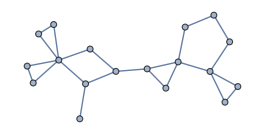
```mathematica
IGCactusQ[-Graphics-]
```

```mathematica
IGCactusQ[GridGraph[{2,3}]]
```

IGCactusQ supports multigraphs and ignores self-loops.

```mathematica
IGCactusQ/@{-Graphics-,-Graphics-}
```

The null graph is not considered to be a cactus, but the singleton graph is.

```mathematica
IGCactusQ/@{IGEmptyGraph[0],IGEmptyGraph[1]}
```

Currently, IGCactusQ does not support directed graphs.

```mathematica
IGCactusQ[Graph[{1->2}]]
```

## Motifs and subgraphs

### Motifs

IGraph/M’s motif-related functions count the number of times each possible connectivity pattern of k vertices (i.e. induced subgraph of size k) occurs in a graph. The patterns are called motifs. As of IGraph/M 0.4, only size 3 and 4 motifs are supported, and only (weakly) connected subgraphs are considered.

To count larger induced subgraphs, see IGLADSubisomorphismCount. To identify where a subgraph occurs, see IGLADFindSubisomorphisms.

To count non-connected size-3 subgraphs, use IGTriadCensus.

igraph’s motif functions use the RAND-ESU algorithm, which is able to uniformly sample a random subset of motifs (connected subgraphs), and can thus estimate motif counts even in very large graphs. See the description of IGMotifs for an example.

##### References

S. Wernicke, Efficient Detection of Network Motifs, IEEE/ACM Trans. Comput. Biol. Bioinforma. 3, 347 (2006).

#### IGMotifs

```mathematica
?IGMotifs
```

IGMotifs counts how many times each motif (i.e. induced subgraph) of the given size occurs in the graph. For subgraphs that are not weakly connected, Indeterminate is returned.

Available options are:

DirectedEdges→False treats the graph as undirected and DirectedEdges→True treats the graph as directed. The default is DirectedEdges→Automatic, which respects the directedness of the graph.

Motifs are returned by their IGIsoclass, i.e. the same order as listed in IGData.

```mathematica
mot3=Graph[#,ImageSize->36,VertexSize->0.1]&/@IGData[{"AllDirectedGraphs",3}]
```

Let us count size-3 motifs in the following graph, and summarize them a table. For non-weakly-connected subgraphs, Indeterminate is returned.

```mathematica
g=RandomGraph[{10,40},DirectedEdges->True]
```

```mathematica
Grid[{mot3,IGMotifs[g,3]}ᵀ,Frame->All]
```

Empty graphs are treated as undirected by default. To treat them as directed, use DirectedEdges→True. The result will be different as the number of non-isomorphic graphs on k vertices is not the same in the directed and undirected cases.

```mathematica
IGMotifs[IGEmptyGraph[5],3,DirectedEdges->#]&/@{Automatic,True,False}
```

##### Example: metabolic network

Let us find the size-4 motifs that stand out in the E. coli metabolic network by comparing the motif counts to that of a rewired graph:

```mathematica
g=ExampleData[{"NetworkGraph","MetabolicNetworkEscherichiaColi"}];
```

```mathematica
rg=IGRewire[g,50000];
```

```mathematica
ratios=N@Quiet[IGMotifs[g,4]/IGMotifs[rg,4]]
```

```mathematica
largeRatios=Select[ratios,#>5&]
```

There are two motifs that are more than 30 times more common in the metabolic network than in the rewired graph.

```mathematica
Extract[IGData[{"AllDirectedGraphs",4}],FirstPosition[ratios,#]]&/@largeRatios
```

The Davidson–Harel algorithm attempts to reduce edge crossings and can draw these subgraphs in a clearer way:

```mathematica
IGLayoutDavidsonHarel/@%
```

##### Estimating motif counts in large graphs

IGMotifs uses the RAND-ESU algorithm which can uniformly sample a random subset of motifs, and thus estimate motif counts even in very large graphs. To enable random sampling, set a cutoff probability cutoff={p_1,p_2,…,p_n} for stopping the search at each level of the ESU tree. The length of the cutoff probability vector, n, must be the same as the motif size. The number of sampled motifs is, on average, a fraction (1-p_1)×(1-p_2)×…×(1-p_n) of the total number.

```mathematica
bigG=ExampleData[{"NetworkGraph","WorldWideWeb"}];
{VertexCount[bigG],EdgeCount[bigG]}
```

Sample a fraction 0.1^3=0.001 of all motifs.

```mathematica
IGMotifs[bigG,3,1-0.1{1,1,1}]//AbsoluteTiming
```

Sample 12.5% of motifs, i.e. a fraction of 0.5^3.

```mathematica
IGMotifs[bigG,3,1-0.5{1,1,1}]//AbsoluteTiming
```

#### IGMotifsVertexParticipation

```mathematica
?IGMotifsVertexParticipation
```

IGMotifsVertexParticipation counts how many times each vertex participates in each motif. For each vertex, the result is returned in the same format as with IGMotifs.

Available options are:

DirectedEdges→False treats the graph as undirected and DirectedEdges→True treats the graph as directed. The default is DirectedEdges→Automatic, which respects the directedness of the graph.

Count how many times each vertex appears in each 3-motif in a directed graph.

```mathematica
g=-Graphics-;
```

```mathematica
mot=IGMotifsVertexParticipation[g,3]
```

The sum of the participation counts in 3-motifs is 3 times the total motif counts of the graph.

```mathematica
Total[mot]===3IGMotifs[g,3]
```

#### IGMotifsTotalCount and IGMotifsTotalCountEstimate

```mathematica
?IGMotifsTotalCount
```

```mathematica
?IGMotifsTotalCountEstimate
```

IGMotifsTotalCount[graph,motifSize] counts the number of weakly connected subgraphs of the given size in a graph.

IGMotifsTotalCountEstimate[graph,motifSize,sampleSize] estimates the total number of motifs by taking a random subset of vertices of the specified size, and counting motifs in which these vertices participate. The total number is estimated as motifCount×vertexCount/sampleSize. IGMotifsTotalCountEstimate[graph,motifSize,vertices] uses the specified vertices as the sample.

Let us create a graph.

```mathematica
g=RandomGraph[{20,50}];
```

The number of size-4 subgraphs it has is:

```mathematica
Binomial[VertexCount[g],4]
```

However, only a small fraction of these is connected:

```mathematica
IGMotifsTotalCount[g,4]
```

IGMotifsTotalCount is effectively equivalent to (but much faster than) the following:

```mathematica
Count[Subsets[VertexList[g],{4}],subset_/;WeaklyConnectedGraphQ@Subgraph[g,subset]]
```

Estimate the count of connected subgraphs by subsampling: at each level of the ESU tree, continue only with probability 0.9.

```mathematica
IGMotifsTotalCount[g,4,1-0.9{1,1,1,1}]/0.9^4
```

Estimate the count of connected subgraphs by considering a random subset of 15 vertices (out of a total of 20).

```mathematica
IGMotifsTotalCountEstimate[g,4,15]
```

Use the first 15 vertices tot estimate the count.

```mathematica
IGMotifsTotalCountEstimate[g,4,Range[15]]
```

### Triad and dyad census

```mathematica
?IGTriadCensus
```

```mathematica
?IGDyadCensus
```

See IGData["MANTriadLabels"] for the mapping between MAN labels and graphs.

IGTriadCensus[g] does not return triad counts in the same order as IGMotifs[g,3], i.e. ordered according to the triads’ IGIsoclass[]. To get the result ordered by isoclass, use

```mathematica
Lookup[IGTriadCensus[g],Keys@IGData["MANTriadLabels"]]
```

IGData["MANTriadLabels"] are ordered according to isoclass.

### Finding triangles

#### IGTriangles

```mathematica
?IGTriangles
```

Highlight all triangles in a graph.

```mathematica
g=RandomGraph[{8,16},VertexSize->Large];
```

```mathematica
HighlightGraph[g,Subgraph[g,#],ImageSize->Tiny,GraphHighlightStyle->"Thick"]&/@IGTriangles[g]
```

#### IGAdjacenctTriangleCount

```mathematica
?IGAdjacentTriangleCount
```

Label a graph’s vertices based on the number of adjacent triangles.

```mathematica
RandomGraph[{8,16},VertexSize->Large]//IGVertexMap[Placed[#,Center]&,VertexLabels->IGAdjacentTriangleCount]
```

#### IGTriangleFreeQ

Triangle-free graphs do not have any fully connected subgraphs of size 3. Equivalently, they do not have any cliques (other than 2-cliques, which are edges).

```mathematica
?IGTriangleFreeQ
```

Mycielski graphs are triangle-free.

```mathematica
IGTriangleFreeQ@GraphData[{"Mycielski", 10}]
```

## Isomorphism and automorphism groups

igraph implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality.

Naming: Most of IGraph/M's isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. Functions named as …GetIsomorphism will find a single isomorphism. Functions named as …FindIsomorphisms can find multiple isomorphisms. Both return a result in a format compatible with the built-in FindGraphIsomorphism.

Additionally, IGIsomorphicQ[] and IGSubisomorphicQ[] try to select the best algorithm for the given graphs. For graphs without multi-edges, they use igraph’s default algorithm selection. For multigraphs, they use VF2 after internally transforming the multigraphs to edge- and vertex-coloured simple graphs, in a manner similar to IGColoredSimpleGraph.

### Basic functions

#### IGIsomorphicQ

```mathematica
?IGIsomorphicQ
```

```mathematica
?IGGetIsomorphism
```

IGIsomorphicQ decides if two graphs are isomorphic.

```mathematica
IGIsomorphicQ[IGShorthand["a-b-c-a-d"],IGShorthand["1-2,3-4-2-3"]]
```

IGIsomorphicQ supports multigraphs.

```mathematica
IGIsomorphicQ[-Graphics-,-Graphics-]
```

```mathematica
IGIsomorphicQ[-Graphics-,-Graphics-]
```

Get a specific mapping between the vertices of the graphs.

```mathematica
IGGetIsomorphism[-Graphics-,-Graphics-]
```

When the graphs are not isomorphic, an empty list is returned.

```mathematica
IGGetIsomorphism[CycleGraph[4],IGCompleteGraph[4]]
```

#### IGSubisomorphicQ

```mathematica
?IGSubisomorphicQ
```

```mathematica
?IGGetSubisomorphism
```

IGSubisomorphicQ decides if a subgraph is part of a larger graph.

A dodecahedral graph does not contain a [1,2,3] symmetric tree.

```mathematica
target=GraphData["DodecahedralGraph"];
pattern=IGSymmetricTree[{1,2,3}];
```

```mathematica
IGSubisomorphicQ[pattern,target]
```

It does contain a [3,2,1] tree.

```mathematica
pattern=IGSymmetricTree[{3,2,1}];
IGSubisomorphicQ[pattern,target]
```

Let us retrieve a specific mapping ...

```mathematica
{iso}=IGGetSubisomorphism[pattern,target]
```

... and highlight it.

```mathematica
HighlightGraph[target,VertexReplace[pattern,Normal[iso]],
GraphHighlightStyle->"Thick"
]
```

IGSubisomorphicQ supports multigraphs.

```mathematica
IGSubisomorphicQ[-Graphics-,-Graphics-]
```

```mathematica
IGGetSubisomorphism[-Graphics-,-Graphics-]
```

```mathematica
IGSubisomorphicQ[-Graphics-,-Graphics-]
```

```mathematica
IGSubisomorphicQ[-Graphics-,-Graphics-]
```

### Bliss

The Bliss library was developed by Tommi Junttila and Petteri Kaski. It is capable of canonical labelling of directed or undirected vertex coloured graphs.

Bliss generally outperforms Mathematica’s built-in isomorphisms functions (including finding and counting automorphisms) as of Mathematica 12.0. However, this advantage will only be apparent for large and difficult graphs. For small ones the overhead of having to copy the graph and convert it to igraph’s internal format is much larger than the actual computation time.

```mathematica
?IGBliss*
```

All Bliss functions take a "SplittingHeuristics" option, which can influence the performance of the method. Possible values are:

"First" – First non-unit cell. Very fast but may result in large search spaces on difficult graphs. Use for large but easy graphs.

"FirstSmallest" – First smallest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstLargest" – First largest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstMaximallyConnected" – First maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstSmallestMaximallyConnected" – First smallest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstLargestMaximallyConnected" – First largest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

The default setting is "FirstLargest", which performs well on average on sparse graphs.

Note: The result of the IGBlissCanonicalLabeling, IGBlissCanonicalPermutation and IGBlissanonicalGraph functions depend on the choice of "SplittingHeuristics". See the Bliss documentation for more information.

##### Basic examples

Let us take the cuboctahedral graph from GraphData …

```mathematica
g1=GraphData["CuboctahedralGraph"]
```

… and also generate it based on its LCF notation.

```mathematica
g2=IGLCF[{4,2},6]
```

The two graphs are isomorphic:

```mathematica
IGBlissIsomorphicQ[g1,g2]
```

One particular mapping between them is the following:

```mathematica
IGBlissGetIsomorphism[g1,g2]
```

How many mappings are there in total? The same number as the number of automorphisms of either graph.

```mathematica
IGBlissAutomorphismCount[g1]
```

Bliss cannot generate all 48 of these mappings directly.  We can either use VF2 for this …

```mathematica
IGVF2FindIsomorphisms[g1,g2]//Length
```

… or we can use the automorphism group computed by the IGBlissAutomorphismGroup function.

```mathematica
group=IGBlissAutomorphismGroup[g1]
```

```mathematica
GroupOrder[group]
```

Ask for all 48 vertex permutations that create isomorphic graphs:

```mathematica
PermutationReplace[VertexList[g1],group]
```

Permuting the adjacency matrix with any of these leaves it invariant.

```mathematica
perms=PermutationList[#,VertexCount[g1]]&/@GroupElements[group];
Equal@@(AdjacencyMatrix[g1][[#,#]]&/@perms)
```

Bliss works by computing a canonical labelling of vertices. Then isomorphism can be tested for by comparing the canonically relabelled graphs.

```mathematica
IGBlissCanonicalGraph[g1]===IGBlissCanonicalGraph[g2]
```

IGBlissCanonicalGraph returns graphs in a consistent format so that two graphs are isomorphic if and only if their canonical graphs will compare equal with ===. Note that in Mathematica, graphs may not always compare equal even if they have the same vertex and edge lists.

The corresponding permutation and labelling are

```mathematica
IGBlissCanonicalPermutation[g1]
```

```mathematica
IGBlissCanonicalLabeling[g1]
```

Notice that the canonical labelling is simply

```mathematica
AssociationThread[VertexList[g1],IGBlissCanonicalPermutation[g1]]
```

Also notice that it is a mapping from g1 to IGBlissCanonicalGraph[g1]:

```mathematica
MemberQ[
IGVF2FindIsomorphisms[g1,IGBlissCanonicalGraph[g1]],
IGBlissCanonicalLabeling[g1]
]
```

The canonical graph returned by IGBlissCanonicalGraph always has vertices labelled by the integers 1,2,… It can also be used to filter duplicates from a list of graphs

For example, let us generate all possible adjacency matrices of 3-vertex simple directed graphs.

```mathematica
(* fills nondiagonal entries of n by n matrix from vector *)
toMat[vec_,n_]:=SparseArray@Partition[Flatten@Riffle[Partition[vec,n],0,{1,-1,2}],n]
```

There are 2^(3 2)=2^6=64 such matrices.

```mathematica
graphs=AdjacencyGraph[toMat[#,3],DirectedEdges->True]&/@IntegerDigits[Range[2^6]-1,2,6];
```

But only 16 of them correspond to non-isomorphic graphs

```mathematica
DeleteDuplicatesBy[graphs,IGBlissCanonicalGraph]//Length
```

When IGBlissCanonicalGraph is given a vertex coloured graph, it will encode the colours into a vertex property named "Color". This allows distinguishing between graphs whose canonical graphs are identical in structure, but differ in colouring.

Take for example the following coloured graphs:

```mathematica
g=Graph[{1<->2,2<->3},VertexSize->Large,GraphStyle->"BasicBlack"];
colg1=Graph[g,Properties->{1->{"color"->1},2->{"color"->3},3->{"color"->2}}];
colg2=Graph[g,Properties->{1->{"color"->1},2->{"color"->3},3->{"color"->1}}];
```

Visualize them for clarity:

```mathematica
IGVertexMap[ColorData[97],VertexStyle->IGVertexProp["color"]]/@{colg1,colg2}
```

The vertex and edge lists of their canonical graphs are identical:

```mathematica
cang1=IGBlissCanonicalGraph[{colg1,"VertexColors"->"color"}];
cang2=IGBlissCanonicalGraph[{colg2,"VertexColors"->"color"}];
```

```mathematica
VertexList/@{cang1,cang2}
EdgeList/@{cang1,cang2}
```

But they differ in colouring, and therefore do not compare equal:

```mathematica
IGVertexPropertyList[cang1]
```

```mathematica
IGVertexProp["Color"]/@{cang1,cang2}
```

```mathematica
cang1===cang2
```

The performance of Bliss functions may depend significantly on the choice of splitting heuristics.

```mathematica
g=LineGraph@GraphData[{"Hadamard",{24,6}}];
timings={#,First@Timing@IGBlissAutomorphismGroup[g,"SplittingHeuristics"->#]}&/@
{"First","FirstSmallest","FirstLargest","FirstMaximallyConnected","FirstSmallestMaximallyConnected","FirstLargestMaximallyConnected"};
TableForm[timings,TableHeadings->{None,{"Splitting heuristics","Timing (s)"}}]
```

##### Additional examples

Let us visualize the vertex equivalence classes induced by a graph’s automorphism group. Two vertices are considered equivalent if there is an automorphism that maps one into the other.

```mathematica
With[{g=GraphData[{"Mycielski", 4}]},HighlightGraph[g,GroupOrbits@IGBlissAutomorphismGroup[g],
VertexSize->Large,GraphStyle->"BasicBlack"]
]
```

Visualize the edge equivalence classes of a polyhedron, induced by its skeleton’s automorphism group.

```mathematica
mesh=PolyhedronData["TruncatedOctahedron","BoundaryMeshRegion"]
```

```mathematica
With[{g=IGMeshGraph[mesh,VertexStyle->Black]},
HighlightGraph[g,
EdgeList[g][[#]]&/@GroupOrbits@IGBlissAutomorphismGroup@LineGraph[g]
]
]
```

##### References

T. Junttila, P. Kaski, Engineering an Efficient Canonical Labeling Tool for Large and Sparse Graphs, 2007 Proceedings of the Ninth Workshop on Algorithm Engineering and Experiments, doi:10.1137/1.9781611972870.13.

### VF2

```mathematica
?IGVF2*
```

VF2 supports vertex coloured and edge coloured graphs. A colour specification consists of one or more of the "VertexColors" and "EdgeColors" options. Allowed formats for these options are a list of integers, an association assigning integers to the vertices/edges, or None. When using associations, it is not necessarily to specify a colour for each vertex/edge. The omitted ones are assumed to have colour 0.

The VF2 algorithm only supports simple graphs.

The following graph has two automorphisms: {1,2} and {2,1}.

```mathematica
g=Graph[{1<->2}];
IGVF2IsomorphismCount[g,g]
```

If we colour one of the vertices, the permutation {2,1} becomes forbidden, so only one automorphism remains.

```mathematica
IGVF2IsomorphismCount[{g,"VertexColors"->{1,2}},{g,"VertexColors"->{1,2}}]
```

Multigraphs are not directly supported for isomorphism checking, but we can map the multigraph isomorphism problem into an edge-coloured graph isomorphism one by designating the multiplicity of each edge as its colour.

```mathematica
g1=EdgeAdd[PathGraph[Range[5],VertexLabels->"Name"],2<->3]
```

```mathematica
g2=EdgeAdd[PathGraph[Range[5],VertexLabels->"Name"],4<->3]
```

```mathematica
IGVF2IsomorphicQ[g1,g2]
```

Since g1 and g2 are undirected, we need to bring their edges into a sorted canonical form before counting them. This ensures that 4<->3 and 3<->4 are treated as the same edge.

```mathematica
colors1=Counts[Sort/@EdgeList[g1]]
```

```mathematica
colors2=Counts[Sort/@EdgeList[g2]]
```

```mathematica
IGVF2IsomorphicQ[{Graph@Keys[colors1],"EdgeColors"->colors1},{Graph@Keys[colors2],"EdgeColors"->colors2}]
```

IGIsomorphicQ and IGSubisomorphicQ check multigraph isomorphism in a similar way, based on edge colouring.

##### References

L. P. Cordella, P. Foggia, C. Sansone, and M. Vento, IEEE Trans. Pattern Anal. Mach. Intell. 26, 1367 (2004).

### LAD

The LAD library was developed by Christine Solnon. It is capable of finding subgraphs in a larger graph.

The LAD algorithm only supports simple graphs.

```mathematica
?IGLAD*
```

With the "Induced"→True option LAD will search for induced subgraphs.



```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-]
```

```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

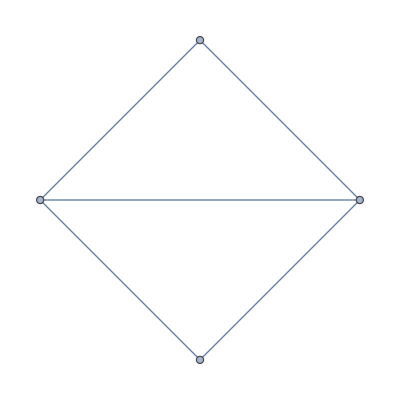
```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

Highlight subgraphs in a grid graph.

```mathematica
g=GridGraph[{3,3}];
HighlightGraph[g,Subgraph[g,#],GraphHighlightStyle->"Thick"]&/@Union[Sort@*Values/@IGLADFindSubisomorphisms[GridGraph[{2,2}],g]]
```

Count how many times each vertex of a graph appears at the apex of the following subgraph (motif):

Generate a directed random graph to do the counting in.

```mathematica
g=RandomGraph[{20,120},DirectedEdges->True]
```

IGShorthand provides a concise way to input this subgraph.

```mathematica
motif=IGShorthand["2<->1<->3"]
```

This motif has a two-fold symmetry, as revealed by its automorphism group. We divide the final counts by two.

```mathematica
Counts@Lookup[
IGLADFindSubisomorphisms[motif,g,"Induced"->True],
1
]/IGBlissAutomorphismCount[motif]
```

Check that a graph is claw-free.

```mathematica
clawFreeQ[graph_?UndirectedGraphQ]:=
Not@IGLADSubisomorphicQ[
StarGraph[4], (* claw graph *)
graph,
"Induced"->True
]
```

```mathematica
clawFreeQ/@{GraphData["DodecahedralGraph"],GraphData["TruncatedPrismGraph"]}
```

##### References

Christine Solnon, AllDifferent-based filtering for subgraph isomorphism, Artificial Intelligence 174 (2010), doi:10.1016/j.artint.2010.05.002

### Isomorphism of coloured graphs

All three included isomorphism algorithms support vertex coloured graphs, and VF2 supports edge coloured graphs as well. A coloured graph is specified as {g, "VertexColors"→…,"EdgeColors"→…}, where both vertex and edge colour specifications are optional. Colours are represented by integers and may be specified in one of the following ways:

A list of integers, given in the same order as VertexList[g] (or EdgeList[g] if specifying edge colours).

{Graph[{a,b},{a<->b}],"VertexColors"→{1,2}}.

An association assigning integers to vertices (or edges). Vertices (or edges) not present in the association are assumed to have colour 0.

{Graph[{a<->b}],"VertexColors"→<|a→1,b→2|>}.

The name of a a vertex (or edge) property. Vertices (or edges) without an assigned property value are assumed to have colour 0.

{Graph[{Property[a,"color"→1],Property[b,"color"→2]},{a<->b}],"VertexColors"→"color"}

"VertexColors"→None indicates no colouring.

Example. Define a graph along with the colours of its vertices.

```mathematica
g=CycleGraph[4];
vcols=<|
1->1,2->1,
3->2,4->2
|>;
```

Visualize it.

```mathematica
Graph[g,
VertexStyle->Normal[ColorData[24]/@vcols],
VertexSize->Medium,VertexLabels->Placed["Name",Center]
]
```

Compute its automorphism group, taking vertex colours into account.

```mathematica
IGBlissAutomorphismGroup[{g,"VertexColors"->vcols}]
```

### Properties related to the automorphism group

The functions in this section test for properties related to a graph’s automorphism group. The summary table below illustrates the functions on a set of graphs which all have different properties.

```mathematica
graphs={StarGraph[4],IGSquareLattice[{2,3},"Periodic"->True],HypercubeGraph[3],GraphData[{"Rook", {4, 4}}],GraphData["ShrikhandeGraph"],GraphData["HoltGraph"],GraphData["Tutte12Cage"],GraphData[{"Paulus",{25,1}}]};

functions=<|
"regular"->IGRegularQ,
"strongly regular"->IGStronglyRegularQ,"distance regular"->IGDistanceRegularQ,
"vertex transitive"->IGVertexTransitiveQ,
"edge transitive"->IGEdgeTransitiveQ,
"arc transitive"->IGEdgeTransitiveQ@*DirectedGraph,
"distance transitive"->IGDistanceTransitiveQ
|>;

TableForm[
Through[Values[functions][#]]&/@graphs,
TableHeadings->{Show[#,ImageSize->50]&/@graphs,Keys[functions]},
TableDirections->Row
]//Style[#,"Text"]&
```

#### IGRegularQ

```mathematica
?IGRegularQ
```

IGRegularQ checks if a graph is regular. All vertices of a regular graph have the same degrees. In regular directed graphs, the in- and out-degrees are also equal to each other.

```mathematica
IGRegularQ[IGSquareLattice[{3,4},"Periodic"->True]]
```

Check if a graph is k-regular for k=2 and k=3.

```mathematica
IGRegularQ[CycleGraph[10],2]
```

```mathematica
IGRegularQ[CycleGraph[10],3]
```

The null graph is considered 0-regular.

```mathematica
IGRegularQ[IGEmptyGraph[]]
```

Check if a directed graph is regular.

```mathematica
IGRegularQ[CycleGraph[5,DirectedEdges->True]]
```

IGRegularQ considers self-loops and multi-edges when computing vertex degrees.

```mathematica
IGRegularQ[-Graphics-]
```

#### IGStronglyRegularQ

```mathematica
?IGStronglyRegularQ
```

IGStronglyRegularQ checks if a graph is strongly regular. A strongly regular graph is a regular graph where each pair of connected vertices have the same number of common neighbours, λ, and each pair of unconnected vertices also have the same number of common neighbours, μ.

```mathematica
IGStronglyRegularQ@GraphData["ShrikhandeGraph"]
```

Hypercube graphs and 3 and higher dimensions are not strongly regular, even though they are regular.

```mathematica
IGStronglyRegularQ/@HypercubeGraph/@Range[2,4]
```

Some authors exclude empty and complete graph from the definition, as they satisfy these conditions trivially. IGStronglyRegularQ returns True for these.

```mathematica
IGStronglyRegularQ/@{IGEmptyGraph[5],IGCompleteGraph[6]}
```

It also returns True for graphs on 0, 1 and 2 vertices.

```mathematica
IGStronglyRegularQ/@IGCompleteGraph/@Range[0,2]
```

Currently, IGStronglyRegularQ does not support directed graphs.

```mathematica
IGStronglyRegularQ@Graph[{1->2}]
```

#### IGStronglyRegularParameters

```mathematica
?IGStronglyRegularParameters
```

IGStronglyRegularParameters returns the parameters (v,k,λ,μ) of a strongly regular graph. v is the number of vertices, k the degree of the vertices, λ the number of common neighbours of connected vertices and μ the number of common neighbours of unconnected vertices.

```mathematica
IGStronglyRegularParameters[PetersenGraph[]]
```

```mathematica
IGStronglyRegularParameters[CycleGraph[5]]
```

The parameters of a strongly regular graph satisfy the equation (v-k-1)μ==k(k-λ-1).

```mathematica
{v,k,lambda,mu}=IGStronglyRegularParameters[GraphData[{"Paley", 101}]]
```

```mathematica
(v-k-1)mu==k(k-lambda-1)
```

λ and μ are not well-defined for empty and complete graphs, respectively. In these cases, 0 is returned.

```mathematica
IGStronglyRegularParameters/@{IGEmptyGraph[5],IGCompleteGraph[6]}
```

For non-strongly-regular graphs, {} is returned.

```mathematica
IGStronglyRegularParameters[HypercubeGraph[3]]
```

#### IGDistanceRegularQ

```mathematica
?IGDistanceRegularQ
```

IGDistanceRegularGraph checks if a graph is distance regular.

```mathematica
IGDistanceRegularQ@HypercubeGraph[5]
```

```mathematica
IGDistanceRegularQ@IGSquareLattice[{2,5},"Periodic"->True]
```

A distance regular graph with a diameter of 2 is also strongly regular.

```mathematica
g=GraphData[{"Paley",13}]
```

```mathematica
{IGDiameter[g],IGDistanceRegularQ[g],IGStronglyRegularQ[g]}
```

The Shrikhande graph is the smallest graph that is distance regular, but not distance transitive.

```mathematica
Through[{IGDistanceRegularQ,IGDistanceTransitiveQ}[GraphData["ShrikhandeGraph"]]]
```

A disconnected graph is distance regular if its components are distance regular and they are co-spectral. The following graphs are co-spectral:

```mathematica
components={GraphData[{"Rook", {4, 4}}],GraphData["ShrikhandeGraph"]}
```

```mathematica
Eigenvalues/@AdjacencyMatrix/@components
```

They are both distance regular with the same intersection array.

```mathematica
IGIntersectionArray/@components
```

Thus their disjoint union is also distance regular.

```mathematica
IGDistanceRegularQ@IGDisjointUnion[components]
```

All distance transitive graphs are also distance regular, but the reverse is not true.

```mathematica
IGDistanceTransitiveQ/@components
```

IGDistanceRegularQ does not currently support directed graphs or non-simple graphs.

```mathematica
IGDistanceRegularQ[Graph[{1->2}]]
```

```mathematica
IGDistanceRegularQ[Graph[{1<->2,1<->2}]]
```

#### IGIntersectionArray

```mathematica
?IGIntersectionArray
```

```mathematica
IGIntersectionArray@GraphData["IcosahedralGraph"]
```

```mathematica
IGIntersectionArray@GraphData["SuzukiGraph"]
```

```mathematica
IGIntersectionArray@CycleGraph[6]
```

For non-distance-regular graphs, {} is returned.

```mathematica
IGIntersectionArray[GridGraph[{3,3}]]
```

IGIntersectionArray does not currently support directed graphs.

```mathematica
IGIntersectionArray[Graph[{1->2}]]
```

#### IGVertexTransitiveQ

```mathematica
?IGVertexTransitiveQ
```

IGVertexTransitiveQ checks if a graph is vertex transitive, i.e. if any vertex can be mapped into any other by some automorphism of the graph.

```mathematica
IGVertexTransitiveQ[-Graphics3D-]
```

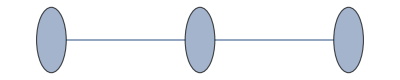
```mathematica
IGVertexTransitiveQ[-Graphics-]
```

All Cayley graphs are vertex transitive.

```mathematica
cg=CayleyGraph@IGBlissAutomorphismGroup@IGLCF[{2,-1,2},3]
```

```mathematica
IGVertexTransitiveQ[cg]
```

#### IGEdgeTransitiveQ

```mathematica
?IGEdgeTransitiveQ
```

IGEdgeTransitiveQ checks if a graph is edge transitive, i.e. if any edge can be mapped into any other by some automorphism of the graph.

```mathematica
IGEdgeTransitiveQ[-Graphics3D-]
```

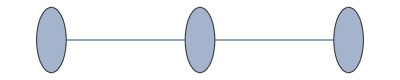
```mathematica
IGEdgeTransitiveQ[-Graphics-]
```

The Folkman graph is not vertex transitive but it is edge transitive.

```mathematica
Through[{IGVertexTransitiveQ,IGEdgeTransitiveQ}@GraphData["FolkmanGraph"]]
```

IGEdgeTransitiveQ takes into account edge directions.

```mathematica
IGEdgeTransitiveQ@Graph[{1->2,2->3}]
```

```mathematica
IGEdgeTransitiveQ@Graph[{1->2,3->2}]
```

Arc transitivity in an undirected graph refers to edge transitivity when each undirected edge is replaced by two opposite directed edges.

```mathematica
arcTransitiveQ[graph_?UndirectedGraphQ]:=IGEdgeTransitiveQ@DirectedGraph[graph]
```

Some graphs are edge transitive, but not arc transitive.

```mathematica
IGEdgeTransitiveQ@GraphData[{"Bouwer",{2,4,15}}]
```

```mathematica
arcTransitiveQ@GraphData[{"Bouwer",{2,4,15}}]
```

Most graphs are edge transitive if their line graphs are vertex transitive. The exceptions are disjoint unions of the 3-star and 3-cycle. These two graphs have the same line graph, but they are not isomorphic.

```mathematica
g=-Graphics-;
```

```mathematica
{IGEdgeTransitiveQ[g],IGVertexTransitiveQ@LineGraph[g]}
```

#### IGSymmetricQ

```mathematica
?IGSymmetricQ
```

IGSymmetricQ checks if a graph is both vertex transitive and edge transitive. Note that this property is distinct from being arc transitive, which is the definition used for “symmetric” by some authors.

```mathematica
IGSymmetricQ[GraphData["DodecahedralGraph"]]
```

Make a table of symmetric graphs up to size 7:

```mathematica
Grid[
Table[
Graph[#,ImageSize->50,PlotTheme->"Business"]&/@Select[GraphData/@GraphData[k],IGSymmetricQ],
{k,1,7}
],Frame->All,ItemSize->All]
```

Some authors use the term symmetric graph to refer to arc transitive graphs. Arc transitivity can be checked using IGEdgeTransitiveQ@DirectedGraph[#]&. All arc-transitive graphs are both vertex- and edge-transitive, but the reverse is not true. The smallest graph that is both vertex- and edge-transitive, but not arc-transitive, is the 27-vertex Doyle graph, also known as the Holt graph.

```mathematica
doyle=GraphData["DoyleGraph"]
```

```mathematica
{IGVertexTransitiveQ[doyle],IGEdgeTransitiveQ[doyle]}
```

```mathematica
IGEdgeTransitiveQ@DirectedGraph[doyle]
```

#### IGDistanceTransitiveQ

```mathematica
?IGDistanceTransitiveQ
```

IGDistanceTransitiveQ checks if a graph is distance transitive. In a distance transitive graph, any two ordered pairs of vertices which are the same distance apart can be mapped into each other by some automorphism.

All Platonic graphs are distance transitive.

```mathematica
IGMeshGraph@PolyhedronData[#,"BoundaryMeshRegion"]&/@PolyhedronData["Platonic"]
```

```mathematica
IGDistanceTransitiveQ/@%
```

Some graphs are symmetric, but not distance transitive.

```mathematica
g=GraphData[{"Circulant",{10,{1,4}}}]
```

```mathematica
{IGSymmetricQ[g],IGDistanceTransitiveQ[g]}
```

IGDistanceTransitiveQ does not exclude non-connected graphs.

```mathematica
IGDistanceTransitiveQ[-Graphics-]
```

IGDistanceTransitiveQ works with directed graphs.

```mathematica
g=With[{n=11},
RelationGraph[MemberQ[Rest@Union@Mod[Range[n]^2,n],Mod[#1-#2,n]]&,Range[n]-1]
]
```

```mathematica
IGDistanceTransitiveQ[g]
```

The following directed graph is vertex transitive, but not distance transitive.

```mathematica
IGDistanceTransitiveQ[-Graphics-]
```

### Homeomorphism

```mathematica
?IGHomeomorphicQ
```

IGHomeomorphicQ tests if two graphs are homeomorphic, i.e. whether they have the same topological structure. Two graphs G_1 and G_2 are homeomorphic if there is an isomorphism from a subdivision of G_1 to a subdivision of G_2.

IGHomeomorphicQ[g_1,g_2] is effectively implemented as IGIsomorphicQ[IGSmoothen[g_1],IGSmoothen[g_2]].

The following graphs are homeomorphic.

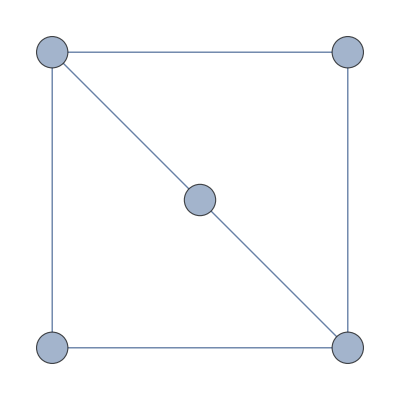
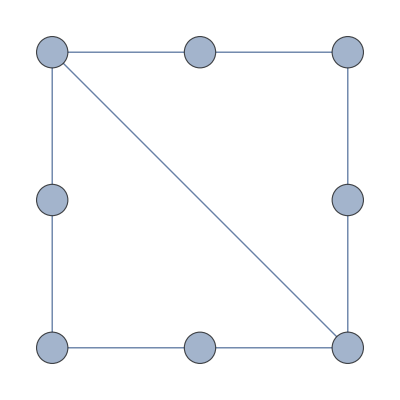
```mathematica
IGHomeomorphicQ[-Graphics-,-Graphics-]
```

They smoothen to the same graph.

```mathematica
IGSmoothen/@{-Graphics-,-Graphics-}
```

Any two cycle graphs are homeomorphic.

```mathematica
IGHomeomorphicQ[CycleGraph[5],CycleGraph[9]]
```

A cycle and a path graph are not homeomorphic.

```mathematica
IGHomeomorphicQ[CycleGraph[5],PathGraph@Range[5]]
```

A triangular and a square lattice on the same number of vertices are, in general, topologically different.

```mathematica
IGHomeomorphicQ[IGSquareLattice[{3,3}],IGTriangularLattice[{3,3}]]
```

When testing empirical graphs for equivalence, it is often useful to remove tree-like components. For example, the face-face and the face-edge adjacency graphs of a geometric mesh are equivalent, save for the tree-like components.

```mathematica
mesh=IGLatticeMesh["SnubSquare",{3,3}];
```

```mathematica
ffg=IGMeshCellAdjacencyGraph[mesh,2,VertexCoordinates->Automatic]
```

```mathematica
feg=IGMeshCellAdjacencyGraph[mesh,1,2,VertexCoordinates->Automatic]
```

```mathematica
IGHomeomorphicQ[feg,ffg]
```

```mathematica
feg=VertexDelete[feg,IGTreelikeComponents[feg]]
```

```mathematica
ffg=VertexDelete[ffg,IGTreelikeComponents[ffg]]
```

```mathematica
IGHomeomorphicQ[feg,ffg]
```

### Other functions

#### IGSelfComplementary

```mathematica
?IGSelfComplementaryQ
```

A graph is called self-complementary if it is isomorphic with its complement.

The 4-vertex path graph is self-complementary.

```mathematica
IGSelfComplementaryQ[PathGraph@Range[4]]
```

Find all 3-vertex self-complementary directed graphs.

```mathematica
Select[IGData[{"AllDirectedGraphs",3}],IGSelfComplementaryQ]
```

#### IGColoredSimpleGraph

```mathematica
?IGColoredSimpleGraph
```

IGColoredSimpleGraph is a helper function that encodes a non-simple graph (i.e a graph with self-loops or multi-edges) into an edge- and vertex-colored simple graph. The coloured simple graph can be used directly as an input to coloured isomorphism checking functions such as IGVF2IsomorphicQ.

The vertex colours are computed as the multiplicity of self-loops at each vertex. The edge colours are computed as the multiplicities or non-loop edges.

The following graphs are not simple and cannot be used with IGVF2IsomorphicQ directly.

```mathematica
{g1,g2,g3}={-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
IGVF2IsomorphicQ[g1,g2]
```

IGColoredSimpleGraph can encode them as coloured graphs. Its output can be supplied directly to IGVF2IsomorphicQ.

```mathematica
IGColoredSimpleGraph[g1]
```

Now can can determine that g1 is isomorphic to g2, but not to g3.

```mathematica
IGVF2IsomorphicQ[IGColoredSimpleGraph[g1],IGColoredSimpleGraph[g2]]
```

```mathematica
IGVF2IsomorphicQ[IGColoredSimpleGraph[g1],IGColoredSimpleGraph[g3]]
```

When searching for subgraphs in multigraphs with this method, be aware that a match occurs only if the edge multiplicities are the same. This sort of matching is useful e.g. in substructure search chemistry, where a double bond must only match another double bond, but not a single one.

```mathematica
IGVF2SubisomorphicQ[IGColoredSimpleGraph[-Graphics-],IGColoredSimpleGraph[-Graphics-]]
```

```mathematica
IGVF2SubisomorphicQ[IGColoredSimpleGraph[-Graphics-],IGColoredSimpleGraph[-Graphics-]]
```

Use IGSubisomorphicQ to match any subgraph.

```mathematica
IGSubisomorphicQ[-Graphics-,-Graphics-]
```

## Maximum flow and minimum cut

### Maximum flow

#### IGMaximumFlowValue

```mathematica
?IGMaximumFlowValue
```

IGMaximumFlowValue is equivalent to IGMinimumCutValue except that it uses the EdgeCapacity property instead of EdgeWeight.

Edge capacities are taken from the EdgeCapacity property.

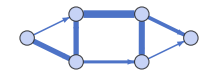
```mathematica
g=-Graphics-;
IGEdgeProp[EdgeCapacity][g]
```

```mathematica
IGMaximumFlowValue[g,1,4]
```

#### IGMaximumFlowMatrix

```mathematica
?IGMaximumFlowMatrix
```

Element F_(i,j) of the flow matrix is the flow through the edge connecting the ith node to the jth one. In an undirected graph, F_(i,j)=-F_(i,j).

Edge capacities are taken from the EdgeCapacity property.

Let us take a directed graph with edge capacities set ...

```mathematica
g=-Graphics-;
```

```mathematica
IGEdgeProp[EdgeCapacity][g]
```

... and compute the maximum flow between two of its vertices.

```mathematica
flowMat=IGMaximumFlowMatrix[g,1,4]
```

The result is returned as a sparse matrix containing the flows through each edge.

```mathematica
MatrixForm[flowMat]
```

If the input is an undirected graph, the flow matrix contains entries of opposing sign for the two directions along each edge.

```mathematica
IGMaximumFlowMatrix[UndirectedGraph[g],1,4]//MatrixForm
```

### Minimum edge cuts

#### IGMinimumCut

```mathematica
?IGMinimumCut
```

#### IGMinimumCutValue

```mathematica
?IGMinimumCutValue
```

Unlike IGEdgeConnectivity, IGMinimumCutValue takes weights into account.

```mathematica
IGMinimumCutValue[Graph[{1<->2,2<->3},EdgeWeight->{3.5,5.6}]]
```

The minimum cut value of the null graph and singleton graph are returned as 0 and ∞, respectively.

```mathematica
IGMinimumCutValue/@{IGEmptyGraph[0],IGEmptyGraph[1]}
```

#### IGGomoryHuTree

```mathematica
?IGGomoryHuTree
```

The Gomory–Hu tree is a weighted tree that encodes the minimum cuts between all pairs of vertices of an undirected graph. The Gomory–Hu tree has the same vertices as the graph it characterizes. The minimum cut between an s-t pair of the graph has the same size as smallest edge weight on the path from s to t in the Gomory–Hu tree.

Weighted graphs are supported.

```mathematica
g=-Graphics-;
```

```mathematica
t=IGGomoryHuTree[g,
EdgeLabels->"EdgeWeight",VertexShapeFunction->"Name"
]
```

The path from 1 to 9 is 1<->2<->5<->9 and has the weights {3,5,4}. The smallest one, 3, is the minimum value of a cut separating 1 from 9.

```mathematica
{IGMinimumCutValue[g,1,9],IGMinimumCutValue[t,1,9]}
```

### Cohesive blocks

```mathematica
?IGCohesiveBlocks
```

The following examples are based on the ones in the R/igraph documentation.

This is the network from the Moody-White paper:

J. Moody and D. R. White. Structural cohesion and embeddedness: A hierarchical concept of social groups. American Sociological Review, 68(1):103–127, Feb 2003.

```mathematica
mw=Graph[{"1"<->"2","1"<->"3","1"<->"4","1"<->"5","1"<->"6","2"<->"3","2"<->"4","2"<->"5","2"<->"7","3"<->"4","3"<->"6","3"<->"7","4"<->"5","4"<->"6","4"<->"7","5"<->"6","5"<->"7","5"<->"21","6"<->"7","7"<->"8","7"<->"11","7"<->"14","7"<->"19","8"<->"9","8"<->"11","8"<->"14","9"<->"10","10"<->"12","10"<->"13","11"<->"12","11"<->"14","12"<->"16","13"<->"16","14"<->"15","15"<->"16","17"<->"18","17"<->"19","17"<->"20","18"<->"20","18"<->"21","19"<->"20","19"<->"22","19"<->"23","20"<->"21","21"<->"22","21"<->"23","22"<->"23"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[mw]
```

```mathematica
CommunityGraphPlot[mw,Rest@blocks,CommunityRegionStyle->Table[Directive[Opacity[0.5],ColorData[96][i]],{i,Length[blocks]-1}]]
```

```mathematica
cohesion
```

Science camp network:

```mathematica
sc=Graph[{"Pauline"<->"Jennie","Pauline"<->"Ann","Jennie"<->"Ann","Jennie"<->"Michael","Michael"<->"Ann","Holly"<->"Jennie","Jennie"<->"Lee","Michael"<->"Lee","Harry"<->"Bert","Harry"<->"Don","Don"<->"Bert","Gery"<->"Russ","Russ"<->"Bert","Michael"<->"John","Gery"<->"John","Russ"<->"John","Holly"<->"Pam","Pam"<->"Carol","Holly"<->"Carol","Holly"<->"Bill","Bill"<->"Pauline","Bill"<->"Michael","Bill"<->"Lee","Harry"<->"Steve","Steve"<->"Don","Steve"<->"Bert","Gery"<->"Steve","Russ"<->"Steve","Pam"<->"Brazey","Brazey"<->"Carol","Pam"<->"Pat","Brazey"<->"Pat","Carol"<->"Pat","Holly"<->"Pat","Gery"<->"Pat"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[sc]
```

```mathematica
CommunityGraphPlot[sc,Rest@blocks,CommunityRegionStyle->ColorData[96],ImageSize->Large]
```

## Cliques and independent vertex sets

```mathematica
?IG*Clique*
```

A clique is a fully connected subgraph. An independent vertex set is a subset of a graph’s vertices with no connections between them.

### Counting cliques

Mathematica’s FindClique function only finds maximal cliques. IGraph/M provides functions for finding or counting all cliques, i.e. complete subgraphs, of a graph.

```mathematica
g=ExampleData[{"NetworkGraph","CoauthorshipsInNetworkScience"}];
```

```mathematica
{VertexCount[g],EdgeCount[g]}
```

Simply counting cliques is much more memory efficient (and faster) than returning all of them.

```mathematica
IGCliqueSizeCounts[g]
```

```mathematica
BarChart[%,ChartLabels->Range@Length[%]]
```

```mathematica
IGMaximalCliqueSizeCounts[g]
```

```mathematica
BarChart[%,ChartLabels->Range@Length[%]]
```

```mathematica
IGLargestCliques[g]
```

### Cliques in directed graphs

The clique finder in IGraph/M ignores edge directions.

```mathematica
g=RandomGraph[{10,60},DirectedEdges->True]
```

```mathematica
IGMaximalCliques[g]
```

To find cliques in directed graphs, convert them to undirected and keep mutual (bidirectional) edges only.

```mathematica
IGMaximalCliques@IGUndirectedGraph[g,"Mutual"]
```

### Clique cover

```mathematica
?IGCliqueCover
```

```mathematica
?IGCliqueCoverNumber
```

A clique cover of a graph is a partitioning of its vertices such that each partition forms a clique. IGCliqueCover finds a minimum clique cover, i.e. a partitioning into a smallest number of cliques.

The clique cover number of a graph is the smallest number of cliques that can be used to cover its vertices.

Available Method option values are:

"Minimum" finds a minimum clique cover.

"Heuristic" is much faster, but the result is not typically a minimum cover.

Compute a minimum clique cover of a random graph.

```mathematica
g=RandomGraph[{10,20}]
```

```mathematica
IGCliqueCover[g]
```

Visualize the clique cover.

```mathematica
HighlightGraph[g,IGCliqueCover[g],VertexSize->Large]
```

Find the clique cover number without returning a cover.

```mathematica
IGCliqueCoverNumber[g]
```

The clique cover problem is equivalent to the colouring of the complement graph. IGCliqueCover is effectively implemented as

```mathematica
IGMembershipToPartitions[g]@IGMinimumVertexColoring@GraphComplement[g]
```

For difficult problems, it may be useful to use IGMinimumVertexColoring or IGVertexColoring directly instead of IGCliqueCover, and tune their options to achieve better performance. See the "ForcedColoring" option of IGMinimumVertexColoring on how to do this.

### Reconstruct bipartite graph of co-occurrence network

```mathematica
g=ExampleData[{"NetworkGraph","LesMiserables"}]
```

```mathematica
ExampleData[{"NetworkGraph","LesMiserables"},"LongDescription"]
```

The maximal cliques of the graph can approximate the scenes in which characters appear together.

```mathematica
cliques=IGMaximalCliques[g];
```

We can construct a bipartite graph of connections between potential scenes and characters

```mathematica
IGLayoutBipartite[
Graph@Catenate[Thread/@Thread[Range@Length[cliques]<->cliques]],
VertexSize->0.5,ImageSize->220
]//IGVertexMap[Placed[#,If[IntegerQ[#],Before,After]]&,VertexLabels->VertexList]
```

### Graphlet decomposition

```mathematica
?IGGraphlets
```

```mathematica
?IGGraphletBasis
```

```mathematica
?IGGraphletProject
```

TODO TODO TODO

Graphlet decomposition in igraph works for graphs with integer edge weights.

```mathematica
g=IGShorthand["A,B,D,E,C, A-B-C-A, C-E-D-B, D-C, E-B",
EdgeWeight->{2,3,2,4,4,1,4,1},
EdgeLabels->"EdgeWeight",VertexLabels->None,
VertexShapeFunction->"Name",PerformanceGoal->"Quality",
GraphLayout->"CircularEmbedding"
]
```

```mathematica
basis=IGGraphletBasis[g]
```

```mathematica
IGGraphletProject[g,Keys[basis]]
```

```mathematica
IGGraphlets[g]
```

## Layout algorithms

The following functions are available:

```mathematica
?IGLayout*
```

If you are looking for the Sugiyama layout from igraph, try the built-in  GraphLayout→"LayeredDigraphEmbedding", or LayeredGraphPlot. These are also based on the Sugiyama algorithm.

### Common options and examples

Layout functions also take any standard Graph option.

Many layout algorithms take the following options:

"MaxIterations" controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm and settings. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

"Align"→True aligns the output horizontally. Examples:

```mathematica
{IGLayoutFruchtermanReingold[IGSquareLattice[{2,4}](*, "Align" -> True is the default *)],IGLayoutFruchtermanReingold[IGSquareLattice[{2,4}],"Align"->False]}
```

"Continue"→True allows using existing vertex coordinates as starting points for algorithms that update vertex positions incrementally. We can use this to visualize how the layout algorithms work …

```mathematica
g=IGLayoutRandom@RandomGraph[BarabasiAlbertGraphDistribution[100,1]];
ListAnimate@NestList[IGLayoutGraphOpt[#,"Continue"->True,"MaxIterations"->80]&,g,40]
```

… or to visualize dynamic graph processes such as adding edges to the graph one by one:

```mathematica
g=IGLayoutKamadaKawai@Graph[Range[25],{1<->25},VertexLabels->"Name"];
ListAnimate@NestList[
IGLayoutKamadaKawai[EdgeAdd[#,UndirectedEdge@@RandomSample[VertexList[#],2]],"MaxIterations"->15,"Continue"->True,"Align"->False]&,
g,
30
]
```

Visualize a planar graph without edge crossings using the Davidson–Harel simulated annealing method, and taking starting coordinates from GraphLayout→"PlanarEmbedding".

```mathematica
g=Graph@GraphData[{"Fullerene",{60,1}},"EdgeList"]
```

This layout avoids crossings, but it is not pleasing:

```mathematica
Graph[g,GraphLayout->"PlanarEmbedding"]
```

We can post process it while avoiding the introduction of any edge crossings:

```mathematica
IGLayoutDavidsonHarel[
IGVertexMap[#&,VertexCoordinates->(Rescale@GraphEmbedding[#,"PlanarEmbedding"]&),g],
"Continue"->True,"EdgeCrossingWeight"->1000
]
```

### Weighted graphs

Several of the graph layout algorithms in igraph can take edge weights into accounts. How the weights are used during layout differs between them.

IGLayoutFruchtermanReingold multiplies the attraction between vertices by the weights. Thus higher weights result in shorter edges.

IGLayoutKamadaKawai produces longer edges for higher weights

### Drawing trees

IGLayoutReingoldTilford[] and IGLayoutReingoldTilfordCircular[] are designed for laying out trees. The following options are available:

"RootVertices" allows nodes to be used as the root nodes in the layout. It must be a list, even if there is a single root node. Multiple root nodes are meant to be used with forests.

DirectedEdges→True lays out the graph so that directed edges are pointing form lower levels (near the root) towards higher ones (away from the root).

"Rotation" controls the orientation of the layout. It must be given in radians.

### Drawing bipartite graphs

```mathematica
?IGLayoutBipartite
```

IGLayoutBipartite draws a bipartite graph, attempting to minimize the number of edge crossing using the Sugiyama algorithm.

The available options are:

"Orientation" can be Horizontal or Vertical

"PartitionGap" controls the size of the gap between the two partitions

"VertexGap" controls the minimum size of the gap between vertices in a partition

MaxIterations controls the maximum number of iterations performed during edge crossing minimization.

"BipartitePartitions" can be used to explicitly specify the partitioning of the graph.

```mathematica
IGLayoutBipartite[IGBipartiteGameGNP[10,10,0.2],VertexLabels->"Name"]
```

By default, a partitioning is computed automatically.

```mathematica
g=Graph[{1<->2,3<->4},VertexLabels->"Name"];
IGLayoutBipartite[g]
```

The partitioning can also be specified explicitly.

```mathematica
IGLayoutBipartite[g,"BipartitePartitions"->{{2,3},{4,1}}]
```

Draw a bipartite layout with curved edges.

```mathematica
snake[{x1_,y1_},{x2_,y2_}]:=BezierCurve[{{x1,y1},{(x1+x2)/2,y1},{(x1+x2)/2,y2},{x2,y2}}]
IGLayoutBipartite@IGBipartiteGameGNM[10,10,20,EdgeShapeFunction->({CapForm["Round"],snake[First[#1],Last[#1]]}&),GraphStyle->"ThickEdge",VertexStyle->Black]
```

### Drawing large graphs

IGLayoutDrL is designed specifically for visualizing large graphs with high clustering. The following image is created using DrL and shows a 36000 node network of collaborations between condensed matter scientists.

-Graphics-

The image was generated using the following code:

```mathematica
lg=ExampleData[{"NetworkGraph","CondensedMatterCollaborations2005"}];
lg=IndexGraph@Subgraph[lg,First@ConnectedComponents[lg]];
c=IGCommunitiesMultilevel[lg]
pts=GraphEmbedding@IGLayoutDrL[lg]; (* this takes a while *)
figure=Graphics[
GraphicsComplex[pts,
{
{White,AbsoluteThickness[0.3],Opacity[0.05],
Line[List@@@EdgeList[lg]]},
{AbsolutePointSize[2],Opacity[0.7],
MapIndexed[
{ColorData[45]@First[#2],Point[#1]}&,
c["Communities"]
]}
}
],
Background->Black
]
```

⇧-⌤ evaluation is disabled in the cell above to avoid running it accidentally. Running the code takes about 2-3 minutes on a modern computer. Copy the code to a new cell to try it.

### Gallery

Create galleries of the various graph layouts available in IGraph/M.

Visualise a tree graph with all layouts.

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[30,1]];
layouts=Graph[#[g],PlotLabel->#,LabelStyle->7]&/@{IGLayoutCircle,IGLayoutDavidsonHarel,IGLayoutDrL,IGLayoutDrL3D,IGLayoutFruchtermanReingold,IGLayoutFruchtermanReingold3D,IGLayoutGEM,IGLayoutGraphOpt,IGLayoutKamadaKawai,IGLayoutKamadaKawai3D,IGLayoutRandom,IGLayoutReingoldTilford,IGLayoutReingoldTilfordCircular,IGLayoutSphere,IGLayoutBipartite,IGLayoutPlanar};
Multicolumn[layouts]
```

Visualise a polyhedral graph with all layouts.

```mathematica
g=GraphData["DodecahedralGraph"];
layouts=Graph[#[g],PlotLabel->#,LabelStyle->7]&/@{IGLayoutCircle,IGLayoutDavidsonHarel,IGLayoutDrL,IGLayoutDrL3D,IGLayoutFruchtermanReingold,IGLayoutFruchtermanReingold3D,IGLayoutGEM,IGLayoutGraphOpt,IGLayoutKamadaKawai,IGLayoutKamadaKawai3D,IGLayoutRandom,IGLayoutSphere,IGLayoutPlanar,IGLayoutTutte};
Multicolumn[layouts]
```

## Community detection

The following functions are available:

```mathematica
?IGCommunities*
```

### Concepts

Modularity is defined for a given partitioning of a graph’s vertices into communities. It is defined as

Q=1/(2m)∑_(i,j) (A_(i,j)-(k_i k_j)/(2m))δ_(c_i,c_j),

where m is the number of edges, A is the adjacency matrix, k_i is the degree of node i, and c_i is the community that node i belongs to. δ_(i,j) is the Kronecker δ symbol. For weighted graphs, A is the weighted adjacency matrix, k_i are the sum of weights of edges incident on node i, and m is the sum of all weights.

Modularity characterizes the tendency of vertices to connect more within their own group than with other groups. For a given partitioning, it can be computed using IGModularity. Community detection functions find a partitioning of the graph which results in high modularity.

### Basic usage and utility functions

Community detection functions return IGClusterData objects.

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}]
```

```mathematica
cl=IGCommunitiesGreedy[g]
```

The data available in the object can be queried using IGClusterData[…]["Properties"]. See the Examples section below for more information.

```mathematica
cl["Properties"]
```

```mathematica
cl["Communities"]
```

```mathematica
CommunityGraphPlot[g,cl["Communities"],ImageSize->Medium]
```

```mathematica
IGModularity[g,cl]
```

#### IGClusterData

```mathematica
?IGClusterData
```

IGClusterData represents a partitioning of a graph into communities. This object cannot be created directly. It is returned by community detection functions. See the Examples section below for more information.

```mathematica
cl=IGCommunitiesLabelPropagation@ExampleData[{"NetworkGraph","FamilyGathering"}]
```

Query the available properties.

```mathematica
cl["Properties"]
```

Retrieve the communities.

```mathematica
cl["Communities"]
```

When the "Modularity" property is available, Max[cl["Modularity"]] gives the modularity of the current partitioning.

```mathematica
Max[cl["Modularity"]]
```

#### IGModularity

```mathematica
?IGModularity
```

IGModularity[graph,communities] is equivalent to GraphAssortativity[graph,communities,"Normalized"→False].

#### IGCompareCommunities

```mathematica
?IGCompareCommunities
```

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}];
```

```mathematica
{cl1,cl2}={IGCommunitiesGreedy[g],IGCommunitiesEdgeBetweenness[g]}
```

```mathematica
IGCompareCommunities[cl1,cl2]
```

### Community detection methods

#### IGCommunitiesEdgeBetweenness

```mathematica
?IGCommunitiesEdgeBetweenness
```

IGCommunitiesEdgeBetweenness[] implements the Girvan–Newman algorithm.

Weighted graphs are supported. Weights are treated as “distances”, i.e. a large weight represents a weak connection.

Available option values:

"ClusterCount", the number of communities to return. Default: Automatic.

Special properties returned with the result:

"RemovedEdges" is the list of edges removed in each step of the algorithm.

"Bridges" records the steps which resulted in splitting the graph into more components.

##### References

M. Girvan and M. E. J. Newman: Community structure in social and biological networks, PNAS 99, 7821-7826 (2002).

#### IGCommunitiesFluid

```mathematica
?IGCommunitiesFluid
```

IGCommunitiesFluid[] implements the fluid communities algorithm.

##### Reference

F. Parés, D. Garcia-Gasulla, A. Vilalta, J. Moreno, E. Ayguadé, Jesús Labarta, U. Cortés, T. Suzumura: Fluid Communities: A Competitive, Scalable and Diverse Community Detection Algorithm, https://arxiv.org/abs/1703.09307

#### IGCommunitiesGreedy

```mathematica
?IGCommunitiesGreedy
```

IGCommunitiesGreedy[] implements greedy optimization of modularity.

Weighted graphs are supported.

##### Reference

A. Clauset, M. E. J. Newman, C. Moore: Finding community structure in very large networks, http://www.arxiv.org/abs/cond-mat/0408187

#### IGCommunitiesInfoMAP

```mathematica
?IGCommunitiesInfoMAP
```

IGCommunitiesInfoMAP[] implements the InfoMAP algorithm.

It supports both edge weights and vertex weights.

The default number of trials is 10.

##### References

M. Rosvall and C. T. Bergstrom, Maps of information flow reveal community structure in complex networks, PNAS 105, 1118 (2008)

M. Rosvall, D. Axelsson, and C. T. Bergstrom, The map equation, Eur. Phys. J. Special Topics 178, 13 (2009)

#### IGCommunitiesLabelPropagation

```mathematica
?IGCommunitiesLabelPropagation
```

Weighted graphs are supported.

##### References

Raghavan, U.N. and Albert, R. and Kumara, S.: Near linear time algorithm to detect community structures in large-scale networks. Phys. Rev. E 76, 036106. (2007).

#### IGCommunitiesLeadingEigenvector

```mathematica
?IGCommunitiesLeadingEigenvector
```

Weighted graphs are supported.

Available option values:

"ClusterCount", the number of communities to return. May return fewer communities than requested. Default: Automatic.

##### References

M. E. J. Newman: Finding community structure using the eigenvectors of matrices, Phys. Rev. E 74:036104 (2006).

#### IGCommunitiesMultilevel

```mathematica
?IGCommunitiesMultilevel
```

IGCommunitiesMultilevel[] implements the Louvain community detection method.

Weighted graphs are supported.

##### References

V. D. Blondel, J.-L. Guillaume, R. Lambiotte and E. Lefebvre: Fast unfolding of community hierarchies in large networks, J. Stat. Mech. P10008 (2008)

#### IGCommunitiesLeiden

```mathematica
?IGCommunitiesLeiden
```

The Leiden algorithm is similar to the multilevel algorithm, often called the Louvain algorithm, but it is faster and yields higher quality solutions. It can optimize both modularity and the Constant Potts Model, which does not suffer from the resolution-limit (see preprint http://arxiv.org/abs/1104.3083).

The Leiden algorithm consists of three phases: (1) local moving of nodes, (2) refinement of the partition and (3) aggregation of the network based on the refined partition, using the non-refined partition to create an initial partition for the aggregate network. In the local move procedure in the Leiden algorithm, only nodes whose neighborhood has changed are visited. The refinement is done by restarting from a singleton partition within each cluster and gradually merging the subclusters. When aggregating, a single cluster may then be represented by several nodes (which are the subclusters identified in the refinement).

The Leiden algorithm provides several guarantees. The Leiden algorithm is typically iterated: the output of one iteration is used as the input for the next iteration. At each iteration all clusters are guaranteed to be connected and well-separated. After an iteration in which nothing has changed, all nodes and some parts are guaranteed to be locally optimally assigned. Finally, asymptotically, all subsets of all clusters are guaranteed to be locally optimally assigned.

The Leiden method maximizes a quality measure (a generalization of modularity) defined as

Q=1/(2m)∑_(i,j) (A_(i,j)-γ n_i n_j)δ_(c_i,c_j)

where m is the sum of edge weights (number of edges if the graph is unweighted), A is the weighted adjacency matrix, n_i is the weight of vertex i, and c_i is the community that vertex i belongs to. δ_(i,j) is the Kronecker δ symbol.

γ is a resolution parameter that can be set with the "Resolution" option.

The function chooses the vertex weights automatically, according to the value of the VertexWeight option:

VertexWeight→"NormalizedStrength" (default) sets n_i=k_i/(2m), where k_i is the strength (sum of incident edge weights) of vertex i. If γ=1, then the quality measure becomes equivalent to the modularity.

VertexWeight→"Constant" sets n_i=1. With this choice, it is recommended to set the resolution parameter γ. A reasonable γ value for unweighted graphs is the graph density.

VertexWeight→"VertexWeight" takes vertex weights from the VertexWeight graph property.

Other available options:

"Resolution"→γ sets the resolution parameter γ. The default is γ=1. With VertexWeight→"NormalizedStrength", a reasonable value is 1. With VertexWeight→"Constant", a reasonable value is the graph density.

"Beta"→β sets randomness used in the refinement step when merging clusters. The default is β=0.01.

Special properties returned with the result :

"Quality" is the value of the quality measure Q.

Examples:

```mathematica
g=Graph[ExampleData[{"NetworkGraph","LesMiserables"}],GraphStyle->"BasicBlack",VertexSize->2];
```

With the default option values VertexWeight→"NormalizedStrength" and "Resolution"→1, IGCommunitiesLeiden effectively uses the modularity as the quality measure.

```mathematica
cl=IGCommunitiesLeiden[g]
```

```mathematica
{cl["Quality"],IGModularity[g,cl]}
```

```mathematica
HighlightGraph[g,cl["Communities"]]
```

A higher "Resolution" value results in more communities.

```mathematica
HighlightGraph[
g,
IGCommunitiesLeiden[g,"Resolution"->3]["Communities"]
]
```

With VertexWeight→"Constant", it is recommended to set "Resolution" explicitly. A reasonable starting point is GraphDensity[g].

```mathematica
HighlightGraph[
g,
IGCommunitiesLeiden[g,VertexWeight->"Constant","Resolution"->0.1]["Communities"]
]
```

##### References

Traag, V. A., Waltman, L., van Eck, N. J. (2019). From Louvain to Leiden: guaranteeing well-connected communities. Scientific Reports, 9(1), 5233.  http://dx.doi.org/10.1038/s41598-019-41695-z

#### IGCommunitiesOptimalModularity

```mathematica
?IGCommunitiesOptimalModularity
```

Finds the clustering that maximizes modularity exactly. This algorithm is very slow.

Weighted graphs are supported.

#### IGCommunitiesSpinGlass

```mathematica
?IGCommunitiesSpinGlass
```

Weighted graphs are supported.

Option values for Method are:

"Original" only supports positive edge weights, but doesn’t check that the supplied weights are actually positive.

"Negative" supports negative weights as well.

Automatic selects "Negative" if negative weights are presents and "Original" otherwise.

Option values for "UpdateRule" are: "Simple", "Configuration"

##### References

For Method→"Original, see Joerg Reichardt and Stefan Bornholdt: Statistical Mechanics of Community Detection, http://arxiv.org/abs/cond-mat/0603718

For Method→"Negative", see V. A. Traag and Jeroen Bruggeman: Community detection in networks with positive and negative links, http://arxiv.org/abs/0811.2329

#### IGCommunitiesWalktrap

```mathematica
?IGCommunitiesWalktrap
```

IGCommunitiesWalktrap[] finds communities using short random walks, exploiting the fact that random walks tend to stay within the same cluster.

Weighted graphs are supported.

The default number of steps is 4.

Available option values:

"ClusterCount", the number of communities to return. Default: Automatic.

##### References

Pascal Pons, Matthieu Latapy: Computing communities in large networks using random walks, http://arxiv.org/abs/physics/0512106

### Examples

```mathematica
g=ExampleData[{"NetworkGraph","LesMiserables"}]
```

```mathematica
IGEdgeWeightedQ[g]
```

Community detection functions return IGClusterData objects.

```mathematica
cl1=IGCommunitiesEdgeBetweenness[g,"ClusterCount"->7]
cl2=IGCommunitiesWalktrap[g]
```

Various properties of these objects can be queried:

```mathematica
cl1["Communities"]
```

Visualize the detected communities in two different ways:

```mathematica
CommunityGraphPlot[g,cl1["Communities"]]
```

```mathematica
HighlightGraph[g,Subgraph[g,#]&/@cl1["Communities"],GraphHighlightStyle->"DehighlightGray"]
```

Plot the adjacency matrix, reordered to show the community structure.

```mathematica
IGAdjacencyMatrixPlot[g,Catenate@cl1["Communities"]]
```

The available properties depend on which algorithm was used for community detection. The following are always present:

"Properties" returns all available properties.

"Algorithm" returns the algorithm used for community detection.

"Communities" returns the list of communities.

"Elements" returns the vertices of the graph.

"ElementCount" returns the vertex count of the graph.

These are present for hierarchical clustering methods:

"HierarchicalClusters" returns the clustering in a format compatible with the Hierarchical Clustering standard package. Note: Isolated vertices may not be included.

"Merges" represents the hierarchical clustering as a sequence of element merges. Elements are represented by their integer indices, and higher indices are introduced for the subclusters formed by the merges. This format is similar to the one used by MATLAB and many other tools. Note: Isolated vertices may not be included.

"Tree" gives a binary tree representation of the merges. Note: Isolated vertices may not be included.

Additionally, the following, and other, algorithm-specific properties may be present:

"Modularity" is a list of modularities for each step of the algorithm, or a single-element list containing the modularity corresponding to the returned clustering. What constitutes a step depends on the particular algorithm.

The "RemovedEdges" property is specific to the "EdgeBetweenness" method, and isn’t present for "Walktrap".

```mathematica
cl1["Properties"]
```

```mathematica
Take[cl1["RemovedEdges"],10]
```

```mathematica
cl2["Properties"]
```

Multiple properties may be retrieved at the same time.

```mathematica
cl2[{"Algorithm","ElementCount"}]
```

Compare the two clusterings:

```mathematica
IGCompareCommunities[cl1,cl2]
```

Visualize the hierarchical clustering using the Hierarchical Clustering Package.

```mathematica
<<HierarchicalClustering`
```

```mathematica
DendrogramPlot[cl1["HierarchicalClusters"],LeafLabels->(Rotate[#,Pi/2]&),ImageSize->750,AspectRatio->1/2]
```

Hierarchical community structures can also be obtained as a vertex-weighted tree graph.

```mathematica
g=ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
```

```mathematica
cl=IGCommunitiesGreedy[g];
```

```mathematica
clusteringTree=cl["Tree"]
```

```mathematica
{GraphQ[clusteringTree],IGVertexWeightedQ[clusteringTree]}
```

This tree can be supplied as input to Dendrogram.

```mathematica
Dendrogram[clusteringTree,Left]
```

## Graph colouring

The graph colouring problem is assigning “colours” or “labels” to the vertices of a graph so that no two adjacent vertices will have the same colour. Similarly, edge colouring assigns colours to edges so that adjacent edges never have the same colour.

IGraph/M represents colours with the integers 1,2,…. Edge directions and self-loops are ignored.

### Fast heuristic colouring

```mathematica
?IGVertexColoring
```

```mathematica
?IGEdgeColoring
```

These function will find a colouring of the graph using a fast heuristic algorithm. The colouring may not be minimal. Edge directions are ignored.

Compute a vertex colouring of a Mycielski graph.

```mathematica
g=GraphData[{"Mycielski", 4}]
```

IGVertexColoring returns a list of integers, each representing the colour of the vertex that is in the same position in the vertex list.

```mathematica
IGVertexColoring[g]
```

Associate the colours with vertex names.

```mathematica
AssociationThread[VertexList[g],IGVertexColoring[g]]
```

Visualize the colours using IGraph/M’s property mapping functionality. See the Property handling functions documentation section for more information.

```mathematica
Graph[g,VertexSize->1/3,EdgeStyle->Gray]//
IGVertexMap[ColorData[97],VertexStyle->IGVertexColoring]
```

Visualize an edge colouring of the same graph.

```mathematica
Graph[g,GraphStyle->"ThickEdge",EdgeStyle->Opacity[0.7],VertexStyle->Black]//
IGEdgeMap[ColorData[106],EdgeStyle->IGEdgeColoring]
```

Compute a checkerboard-like colouring of a three-dimensional grid graph.

```mathematica
IGVertexMap[ColorData[97],VertexStyle->IGVertexColoring,Graph3D@GridGraph[{4,4,4},VertexSize->0.8]]
```

Compute a colouring of a Voronoi mesh.

```mathematica
mesh=VoronoiMesh[RandomReal[1,{20,2}]]
```

```mathematica
col=IGVertexColoring@IGMeshCellAdjacencyGraph[mesh,2]
```

```mathematica
SetProperty[{mesh,{2,All}},MeshCellStyle->ColorData[97]/@col]
```

Compute a colouring of the map of African countries.

```mathematica
countries=CountryData["Africa"];
borderingQ[c1_,c2_]:=MemberQ[c1["BorderingCountries"],c2]
graph=RelationGraph[borderingQ,countries];
```

```mathematica
GeoGraphics@MapThread[{GeoStyling[{Opacity[0.5],#2}],Polygon[#1]}&,{countries,ColorData[97]/@IGVertexColoring[graph]}]
```

### k-colouring

```mathematica
?IGKVertexColoring
```

```mathematica
?IGKEdgeColoring
```

These functions find a colouring with k or fewer colours. They work by transforming the colouring into a satisfiability problem and using SatisfiabilityInstances.

The available option values are:

"ForcedColoring"→{v_1,v_2,…} forces the given vertices to distinct and increasing colours. Normally, the vertices of a clique are given (which require as many colours as the size of the clique). The main purpose of this option is to reduce the number of redundant solutions of the equivalent SAT problem, and thus improve performance. When using edge colouring functions, a set of edges should be passed.

"ForcedColoring"→"MaxDegreeClique" attempts to find a clique containing a maximum degree vertex, and forces colours on the clique members. On hard problems it may perform orders of magnitude better than "ForcedColoring"→None.

"ForcedColoring"→"LargestClique" finds a largest clique, and forces colours on the clique members.

"ForcedColoring"→None does not force any colours. It is usually the fastest choice for easy problems.

The default setting for "ForcedColoring" is "MaxDegreeClique".

The Moser spindle is not 3-colourable, so no solution is returned.

```mathematica
moser=GraphData["MoserSpindle"];
```

```mathematica
IGKVertexColoring[moser,3]
```

Find a 4-colouring of the Moser spindle ...

```mathematica
IGKVertexColoring[moser,4]
```

... and visualize it.

```mathematica
Graph[moser,GraphStyle->"BasicBlack",VertexSize->Large]//IGVertexMap[ColorData[112],VertexStyle->(First@IGKVertexColoring[#,4]&)]
```

Find a 4-edge-colouring of the Petersen graph.

```mathematica
PetersenGraph[GraphStyle->"ThickEdge",EdgeStyle->Opacity[2/3]]//IGEdgeMap[ColorData[112],EdgeStyle->(First@IGKEdgeColoring[#,4]&)]
```

The following examples illustrate the use of the "ForcedColoring" option. The 6th order Mycielski graph has chromatic number 6. A 6-colouring is easily found even with "ForcedColoring"→None.

```mathematica
g=GraphData[{"Mycielski", 6}];
```

```mathematica
IGKVertexColoring[g,6,"ForcedColoring"->None]//Timing
```

However, showing that the graph is not 5-colourable takes considerably longer.

```mathematica
TimeConstrained[IGKVertexColoring[g,5,"ForcedColoring"->None],5]
```

Forcing colours in the appropriate way reduces the computation time significantly.

```mathematica
IGKVertexColoring[g,5,"ForcedColoring"->"MaxDegreeClique"]//Timing
```

### Minimum colouring

```mathematica
?IGMinimumVertexColoring
```

```mathematica
?IGMinimumEdgeColoring
```

IGMinimumVertexColoring and IGMinimumEdgeColoring find minimum colourings of graphs, i.e. they find a colouring with the fewest possible number of colours. The current implementation tries successively larger k-colourings until it is successful.

IGMinimumVertexColoring and IGMinimumEdgeColoring can use the same "ForcedColoring" option values as IGKVertexColoring and IGKEdgeColoring.

```mathematica
WheelGraph[7,GraphStyle->"BasicBlack",VertexSize->Large]//IGVertexMap[ColorData[97],VertexStyle->IGMinimumVertexColoring]
```

Find a colouring of a large graph.

```mathematica
IGMinimumVertexColoring@RandomGraph[{100,400}]
```

Implement a multipartite graph layout: vertex colouring is equivalent to partitioning the vertices of the graph into groups such that all connections run between different groups, and never within the same group. The colours can be thought of as the indices of groups. IGMembershipToPartitions can be used to convert from a group-index (i.e. membership) representation to a partition representation.

```mathematica
multipartiteLayout[g_?GraphQ,separation:_?NumericQ:1.5,opt:OptionsPattern[]]:=Module[{n,partitions,partitionSizes,vertexCoordinates},
partitions=IGMembershipToPartitions[g]@IGMinimumVertexColoring[g];
partitionSizes=Length/@partitions;
n=Length[partitions];
vertexCoordinates=With[{hl=N@Sin[Pi/n],ir=separation If[n==2,1/2,N@Cos[Pi/n]]},
Catenate@Table[
RotationTransform[2Pi/n k][{#,ir}&/@Subdivide[-hl,hl,partitionSizes⟦k⟧-1]],
{k,1,n}
]
];
IGReorderVertices[Catenate[partitions],g,VertexCoordinates->vertexCoordinates,opt]
];
```

Lay out a bipartite graph.

```mathematica
g=IGBipartiteGameGNM[10,10,30];
multipartiteLayout[g]
```

Lay out multipartite graphs.

```mathematica
g=RandomGraph[{40,40}];
multipartiteLayout[g]
```

```mathematica
g=RandomGraph[{40,160}];
multipartiteLayout[g,GraphStyle->"BasicBlack",EdgeStyle->Opacity[0.2]]
```

Compute a minimum colouring of a triangulation. It can be shown, e.g. based on Brooks’s theorem, that any triangulation of a polygon is 3-colourable.

```mathematica
mesh=DelaunayMesh[RandomReal[1,{20,2}],MeshCellStyle->{1->Black}];
col=IGMinimumVertexColoring@IGMeshCellAdjacencyGraph[mesh,2];
SetProperty[{mesh,{2,All}},MeshCellStyle->ColorData[97]/@col]
```

Find a minimum edge colouring of a graph.

```mathematica
Graph[
GraphData["SixteenCellGraph"],
GraphStyle->"ThickEdge",EdgeStyle->Opacity[2/3]
]//
IGEdgeMap[
ColorData[104],
EdgeStyle->IGMinimumEdgeColoring
]
```

### Chromatic number

```mathematica
?IGChromaticNumber
```

```mathematica
?IGChromaticIndex
```

The chromatic number of a graph is the smallest number of colours needed to colour its vertices. The chromatic index, or edge chromatic number, is the smallest number of colours needed to colour its edges.

Find the chromatic number and chromatic index of a graph.

```mathematica
g=GraphData["IcosahedralGraph"]
```

```mathematica
{IGChromaticNumber[g],IGChromaticIndex[g]}
```

The implementation of IGChromaticNumber and IGChromaticIndex is effectively the following:

```mathematica
{Max@IGMinimumVertexColoring[g],Max@IGMinimumEdgeColoring[g]}
```

### Perfect graphs

```mathematica
?IGPerfectQ
```

IGPerfectQ tests if a graph is perfect. The clique number and the chromatic number is the same for every induced subgraph of a perfect graph.

The current implementation of IGPerfectQ uses the strong perfect graph theorem: it checks that neither the graph nor its complement have a graph hole of odd length.

```mathematica
g=GraphData[{"GeneralizedQuadrangle",{2,1}}]
```

```mathematica
IGPerfectQ[g]
```

The clique number and the chromatic number is the same for every induced subgraph.

```mathematica
AllTrue[
Subgraph[g,#]&/@Subsets@VertexList[g],
IGCliqueNumber[#]==IGChromaticNumber[#]&
]
```

### Utility functions

```mathematica
?IGVertexColoringQ
```

IGVertexColoringQ checks whether neighbouring vertices of a graph are assigned different colours.

The colours may be given as a list, with the same ordering as VertexList[graph].

```mathematica
IGVertexColoringQ[-Graphics-,{1,2,3}]
```

```mathematica
IGVertexColoringQ[-Graphics-,{1,2,2}]
```

The colours may also be given as an association from vertices to colours.

```mathematica
IGVertexColoringQ[-Graphics-,<|1->3,2->2,3->1|>]
```

Any expression may be used for the colours, not only integers.

```mathematica
IGVertexColoringQ[-Graphics-,<|1->"a",2->"b",3->"c"|>]
```

## Processes on graphs

#### IGRandomWalk

```mathematica
?IGRandomWalk
```

IGRandomWalk[] takes a random walk over a directed or undirected graph. If the graph is weighted, the next edge to traverse is selected with probability proportional to its weight.

The available options are:

EdgeWeight can be used to override the existing weights of the graph. EdgeWeight→None will ignore any existing weights.

Traversing self-loops in different directions is considered as distinct probabilities in an undirected graph. Thus vertices 1 and 3 are visited more often in the below graphs than vertex 2:

```mathematica
g=Graph[{1<->1,1<->2,2<->3,3<->3},VertexLabels->"Name"]
```

```mathematica
IGRandomWalk[g,1,100000]//Counts//KeySort
```

This is consistent with their degrees:

```mathematica
VertexDegree[g]
```

Convert the graph to a directed version to traverse self-loops only in one direction.

```mathematica
dg=DirectedGraph[g]
```

```mathematica
{VertexOutDegree[dg],VertexInDegree[dg]}
```

```mathematica
IGRandomWalk[dg,1,100000]//Counts//KeySort
```

If the walker gets stuck, a list shorter than steps will be returned. This may happen in a non-connected directed graph, or in a single-vertex graph component.

```mathematica
IGRandomWalk[IGEmptyGraph[1],1,10]
```

```mathematica
IGRandomWalk[Graph[{1->2}],1,10]
```

How much time does a random walker spend on each node of a network?

```mathematica
g=IGBarabasiAlbertGame[50, 2,DirectedEdges->False]
```

```mathematica
counts=Counts@IGRandomWalk[g,First@VertexList[g],10000]/@VertexList[g]
```

The exact answer can be computed as the leading eigenvector of the process’s stochastic matrix:

```mathematica
sm=Transpose[AdjacencyMatrix[g]/VertexDegree[g]];
{{val},{vec}}=Eigensystem[N[sm],1,Method->{"Arnoldi","Criteria"->"RealPart"}];
```

Compare the exact answer with a finite sample:

```mathematica
ListPlot[{vec/Total[vec],counts/Total[counts]},PlotRange->All,PlotLegends->{"exact","sampled"},PlotStyle->PointSize[0.02]]
```

Random walk on a square grid.

```mathematica
grid=IGSquareLattice[{50,50}];
counts=Counts@IGRandomWalk[grid,1,5000];
Graph[grid,
VertexStyle->
Prepend[
Normal[ColorData["SolarColors"]/@Normalize[counts,Max]],
Black (* colour of unvisited nodes, i.e. default colour *)
],
EdgeShapeFunction->None,
Background->Black
]
```

The fraction of nodes reached after n steps on a grid and a comparable random regular graph.

```mathematica
nodesReached[graph_]:=Length@Union@IGRandomWalk[graph,1,VertexCount[graph]]/VertexCount[graph]
```

```mathematica
grid=IGSquareLattice[{50,50},"Periodic"->True];
regular=IGKRegularGame[50^2,4];
```

```mathematica
Table[
{nodesReached[grid],nodesReached[regular]},
{5000}
]//Transpose//Histogram
```

Generate random spanning trees using loop erased random walks.

```mathematica
randomSpanningTree[graph_?GraphQ]:=
Module[{visited=<||>,i=2,k=1,batchSize=2VertexCount[graph],walk},
walk=IGRandomWalk[graph,RandomChoice@VertexList[graph],batchSize];
visited[walk⟦1⟧]=True;
While[k<VertexCount[graph],
(* register a traversed edge only when it leads to a yet unvisited vertex *)
If[!TrueQ[visited[walk⟦i⟧]],
Sow[walk⟦i-1⟧<->walk⟦i⟧];
visited[walk⟦i⟧]=True;
k++
];
i++;
(* if the walk has not yet visited all vertices, keep walking *)
If[i>Length[walk],
walk=Join[walk,Rest@IGRandomWalk[graph,Last[walk],batchSize]]
];
]//Reap//Last//First
]
```

By taking random spanning trees of spatially embedded planar graphs, we can generate mazes.

```mathematica
graph=IGSquareLattice[{15,15}];
Graph[VertexList[graph],randomSpanningTree[graph],
VertexCoordinates->GraphEmbedding[graph],
GraphStyle->"ThickEdge",VertexShapeFunction->None,EdgeStyle->RGBColor[0.5, 0.6, 0.8, 1]
]
```

```mathematica
graph=IGMeshGraph@DiscretizeRegion@Disk[];
Graph[VertexList[graph],randomSpanningTree[graph],
VertexCoordinates->GraphEmbedding[graph],
GraphStyle->"ThickEdge",VertexShapeFunction->None,EdgeStyle->Directive[RGBColor[0.8, 0.6, 0.5, 1],AbsoluteThickness[4]]
]
```

Take a sample of a large graph using a random walk. The following graph is too large to easily visualize, but visualizing a random-walk-based sample immediately shows signs of a community structure.

```mathematica
g=ExampleData[{"NetworkGraph","AstrophysicsCollaborations"}];
{VertexCount[g],VertexCount@IGGiantComponent[g]}
```

```mathematica
Subgraph[g,IGRandomWalk[g,RandomChoice@VertexList@IGGiantComponent[g],200]]
```

```mathematica
CommunityGraphPlot[%]
```

#### IGRandomEdgeWalk and IGRandomEdgeIndexWalk

```mathematica
?IGRandomEdgeWalk
```

```mathematica
?IGRandomEdgeIndexWalk
```

IGRandomEdgeWalk takes a random walk on a graph and returns the list of traversed edges. If the graph is weighted, the next edge to traverse is selected with probability proportional to its weight.

The available options are:

EdgeWeight can be used to override the existing weights of the graph. EdgeWeight→None will ignore any existing weights.

Take a random walk on a De Bruijn graph, and retrieve the traversed edges.

```mathematica
g=IGDeBruijnGraph[3,3];
IGRandomEdgeWalk[g,RandomChoice@VertexList[g],20]
```

IGRandomEdgeIndexWalk returns the list of indices of the traversed edges instead. This makes it useful for working with multigraphs, as it allows distinguishing between parallel edges.

As an example application, let us consider the following set of affine transformations:

```mathematica
scale12=ScalingTransform[{1/2,1/2}];
a11=TranslationTransform[{1/4,√3/4}]@*scale12;
a21=RotationTransform[Pi/3]@*scale12;
b21=TranslationTransform[{3/4,√3/4}]@*RotationTransform[-Pi/3]@*scale12;
a12=TranslationTransform[{1/2,0}]@*ScalingTransform[{1/2,-1/2}];
a22=scale12;
```

```mathematica
trafos={a11,a21,b21,a12,a22};
```

Let us visualize them by showing an initial (black) triangle and its (red) transformation.

```mathematica
tri=Triangle[{{0,0},{1,0},{1/2,√3/2}}];
Graphics[{tri,Red,GeometricTransformation[tri,#]},ImageSize->Tiny]&/@trafos
```

These transformations describe the mutual self-similarity structure of two fractal curves, according to the following directed graph. Each edge of the graph corresponds to a transformation.

```mathematica
graph=Graph[{1->1,2->1,2->1,1->2,2->2},
VertexLabels->Placed["Name",Center],
VertexShape->{1->-Graphics-,2->-Graphics-},PerformanceGoal->"Quality",
VertexSize->1/3,ImageSize->400
]
```

Let us compute a random walk on this graph, and iteratively apply transformations to the point {0,0} according to the traversed edges.

```mathematica
walk=IGRandomEdgeIndexWalk[graph,1,20000];
pts=Rest@FoldList[#2[#1]&,{0.,0.},trafos⟦walk⟧];
```

The resulting list of points will approximate the union of the two fractal curves.

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point[pts]}]
```

The two curves can be separated by filtering points according to which graph vertex the corresponding directed edge targets. For example, if the point was generated by a transformation corresponding to 1->2, it will belong to curve 2.

```mathematica
targets=Last/@EdgeList[graph]
```

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point@Pick[pts,targets⟦walk⟧,1]}]
```

```mathematica
Image@Graphics[{AbsolutePointSize[1],Point@Pick[pts,targets⟦walk⟧,2]}]
```

The technique described here is taken from “Generating self-affine tiles and their boundaries” by Mark McClure.

## Planar graphs

A graph is said to be planar if it can be drawn in the plane without edge crossings.

A useful concept when working with planar graphs is their combinatorial embedding. A combinatorial embedding of a graph is a counter-clockwise ordering of the incident edges around each vertex. IGraph/M represents combinatorial embeddings as associations from vertices to an ordering of their neighbours. Currently, only embeddings of simple graphs are supported.

Some of the planar graph functionality makes use of the LEMON Graph Library.

#### IGPlanarQ

```mathematica
?IGPlanarQ
```

IGPlanarQ[graph] checks if a graph is planar using the Boyer–Myrvold algorithm.

```mathematica
IGPlanarQ@GraphData[{"Apollonian", 6}]
```

```mathematica
IGPlanarQ@CompleteGraph[5]
```

IGPlanarQ[embedding] checks if a combinatorial embedding is planar. The following are both embeddings of the K_4 complete graph. However, only the first one is planar.

```mathematica
emb1=<|1->{2,3,4},2->{1,4,3},3->{2,4,1},4->{3,2,1}|>;
emb2=<|1->{2,4,3},2->{4,3,1},3->{1,2,4},4->{3,1,2}|>;
```

```mathematica
IGPlanarQ/@{emb1,emb2}
```

The second embedding generates only 2 faces instead of 4, which can be embedded on a torus, but not in the plane (or on a sphere).

```mathematica
Length/@IGFaces/@{emb1,emb2}
```

Unlike the build-in PlanarGraphQ, IGPlanarQ considers the null graph to be planar.

```mathematica
{IGPlanarQ@IGEmptyGraph[],PlanarGraphQ@IGEmptyGraph[]}
```

#### IGMaximalPlanarQ

```mathematica
?IGMaximalPlanarQ
```

A simple graph is maximal planar if no new edges can be added to it without breaking planarity. Maximal planar graphs are sometimes called triangulated graphs or triangulations.

The 3-cycle is maximal planar.

```mathematica
IGMaximalPlanarQ[CycleGraph[3]]
```

The 4-cycle is not because a chord can be added to it without breaking planarity.

```mathematica
IGMaximalPlanarQ[CycleGraph[4]]
```

```mathematica
IGPlanarQ[EdgeAdd[CycleGraph[4],1<->3]]
```

Apollonian graphs are maximal planar.

```mathematica
g=GraphData[{"Apollonian", 2}]
```

```mathematica
IGMaximalPlanarQ[g]
```

All faces of a maximal planar graph are triangles.

```mathematica
Length/@IGFaces[g]
```

Therefore the edge count E and the face count F of a maximal planar graph on more than 2 vertices satisfy 2E=3F. Each edge is incident to two faces and each face is incident to three edges.

```mathematica
{2EdgeCount[g],3Length@IGFaces[g]}
```

#### IGOuterplanarQ

```mathematica
?IGOuterplanarQ
```

IGOuterplanarQ[graph] checks if a graph is outerplanar, i.e. if it can be drawn in the plane without edge crossings and with all vertices being on the outer face.

Outerplanar graphs are also called circular planar. They can be drawn without edge crossings and all vertices on a circle. See the documentation of IGOuterplanarEmbedding for an example.

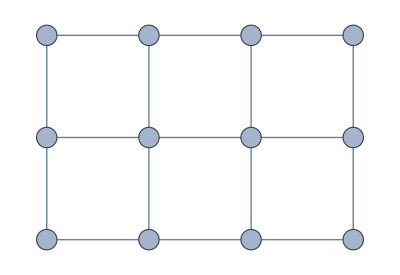
```mathematica
IGOuterplanarQ[-Graphics-]
```

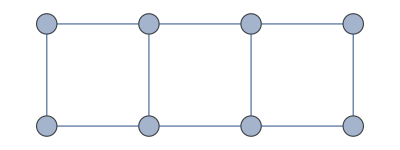
```mathematica
IGOuterplanarQ[-Graphics-]
```

IGOuterplanarQ[embedding] checks if a combinatorial embedding is outerplanar. Not all planar embeddings of an outerplanar graph are also outerplanar embeddings.

Consider the following outerplanar graph …

```mathematica
g=IGShorthand["0-1-2-3-4-2,1-4"]
```

```mathematica
IGOuterplanarQ[g]
```

… and two of its embeddings:

```mathematica
emb1=<|0->{1},1->{2,0,4},2->{1,3,4},3->{2,4},4->{3,1,2}|>;
emb2=<|0->{1},1->{0,2,4},2->{1,3,4},3->{2,4},4->{3,1,2}|>;
```

They are both planar, but only the second one is outerplanar.

```mathematica
IGPlanarQ/@{emb1,emb2}
```

```mathematica
IGOuterplanarQ/@{emb1,emb2}
```

```mathematica
Graph[g,VertexCoordinates->IGEmbeddingToCoordinates[#]]&/@{emb1,emb2}
```

#### IGKuratowskiEdges

```mathematica
?IGKuratowskiEdges
```

IGKuratowskiEdges finds a Kuratowski subgraph of a non-planar graph. The subgraph is returned as a set of edges. If the graph is planar, {} is returned.

According to Kuratowski’s theorem, any non-planar graph contains a subgraph homeomorphic to the K_5 complete graph or the K_(3,3) complete bipartite graph. This is called a Kuratowski subgraph.

Generate a random graph, which is non-planar with high probability.

```mathematica
g=RandomGraph[{20,40}]
```

```mathematica
IGPlanarQ[g]
```

Compute a set of edges belonging to a Kuratowski subgraph.

```mathematica
kur=IGKuratowskiEdges[g]
```

Highlight the Kuratowski subgraph.

```mathematica
HighlightGraph[g,Graph[kur]]
```

Display the Kuratowski subgraph on its own.

```mathematica
Graph[kur]
```

By smoothening the Kuratowski subgraph, we obtain either K_5 or K_(3,3).

```mathematica
IGSmoothen@Graph[kur]
```

```mathematica
IGHomeomorphicQ[Graph[kur],#]&/@{CompleteGraph[5],CompleteGraph[{3,3}]}
```

For planar graphs, {} is returned.

```mathematica
IGKuratowskiEdges@CycleGraph[5]
```

#### IGFaces

```mathematica
?IGFaces
```

IGFaces returns the faces of a planar graph, or the faces corresponding to a specific (not necessarily planar) embedding. The faces are represented by a counter-clockwise ordering of vertices. The current implementation ignores self-loops and multi-edges.

The faces of a planar graph are unique if the graph is 3-vertex-connected. This can be checked using KVertexConnectedGraphQ.

```mathematica
g=GraphData["DodecahedralGraph"]
```

```mathematica
IGFaces[g]
```

```mathematica
KVertexConnectedGraphQ[g,3]
```

If the graph is not connected and has C connected components, then C-1 faces will be redundant.

```mathematica
g=IGDisjointUnion[{CycleGraph[3],CycleGraph[3]},VertexLabels->Automatic]
```

```mathematica
IGFaces[g]
```

In the above-drawn arrangement, the outer faces of the two triangles are the same face. However, one triangle could have been drawn inside of the other. Then the inner face of one would be the same as the outer face of the other. Thus the choice of faces to be eliminated as redundant is arbitrary, and is left up to the user.

IGFaces can also be used with a non-planar combinatorial embedding. The below embeddings both belong to the 4-vertex complete graph, however, only the first is planar.

```mathematica
emb1=<|1->{2,3,4},2->{1,4,3},3->{2,4,1},4->{3,2,1}|>;
emb2=<|1->{2,4,3},2->{4,3,1},3->{1,2,4},4->{3,1,2}|>;
```

```mathematica
IGFaces[emb1]
```

```mathematica
IGFaces[emb2]
```

Determine the genus g of an embedding belonging to a connected graph based on its face count F, vertex count V, and edge count E, using the formula for the Euler characteristic 2g-2=χ=V-E+F.

```mathematica
genus[emb_?IGEmbeddingQ]:= (2+Total[Length/@emb]/2-Length[emb]-Length@IGFaces[emb])/2
```

```mathematica
genus/@{emb1,emb2}
```

#### IGDualGraph

```mathematica
?IGDualGraph
```

IGDualGraph returns a dual graph of a planar graph, or the dual corresponding to a specific embedding. The ordering of the dual graph’s vertices is consistent with the result of IGFaces.

Limitations:

Multi-edges and self-loops are currently ignored.

The result is always a simple graph. No multi-edges or self-loops are generated

The dual of a simple 3-vertex-connected graph is simple and unique, thus such graphs are not affected by the above limitations.

```mathematica
TableForm[
Table[{CompleteGraph[k],IGDualGraph@CompleteGraph[k]},{k,1,4}],
TableHeadings->{None,{"graph","dual"}}
]
```

Currently, if the input is a graph, it must be planar.

```mathematica
IGDualGraph[CompleteGraph[5]]
```

If the input is a combinatorial embedding, it does not need to be planar.

```mathematica
emb=<|1->{2,4,3},2->{4,3,1},3->{1,2,4},4->{3,1,2}|>;
IGPlanarQ[emb]
```

```mathematica
IGDualGraph[emb]
```

Find the dual of a square lattice graph. The dual graph also includes the outer face as a vertex.

```mathematica
IGSquareLattice[{5,5}]
```

```mathematica
IGDualGraph[%]
```

The dual is unique if the graph is 3-vertex-connected. This can be verified using KVertexConnectedGraphQ. In this case, IGDualGraph@IGDualGraph[g] is isomorphic to g.

```mathematica
g=GraphData["IcosahedralGraph"]
```

```mathematica
dg=IGDualGraph[g]
```

```mathematica
IGIsomorphicQ[dg,GraphData["DodecahedralGraph"]]
```

```mathematica
IGIsomorphicQ[IGDualGraph[dg],g]
```

If the graph is not connected, the dual of each component is effectively computed separately.

```mathematica
IGDualGraph@IGDisjointUnion[{CycleGraph[3],CycleGraph[3]}]
```

#### IGEmbeddingQ

```mathematica
?IGEmbeddingQ
```

IGEmbeddingQ checks if an embedding is valid, and whether it belongs to a graph without self-loops and multi-edges.

This is a valid combinatorial embedding of the graph 1<->3<->2.

```mathematica
IGEmbeddingQ[<|1->{3},2->{3},3->{1,2}|>]
```

The following embeddings do not belong to simple (i.e. loop free and multi-edge free) graphs:

```mathematica
IGEmbeddingQ[<|1->{3},2->{3,3},3->{1,2,2}|>]
```

```mathematica
IGEmbeddingQ[<|1->{1,2},2->{1}|>]
```

The following embedding is not valid because it does not contain the arc 2->1 but it does contain 1->2.

```mathematica
IGEmbeddingQ[<|1->{2},2->{}|>]
```

#### IGPlanarEmbedding

```mathematica
?IGPlanarEmbedding
```

IGPlanarEmbedding computes a combinatorial embedding of a planar graph. The current implementation ignores self-loops and multi-edges.

```mathematica
g=IGShorthand["a:b:c:d -- a:b:c:d"]
```

```mathematica
emb=IGPlanarEmbedding[g]
```

The representation of a combinatorial embedding is also a valid adjacency list, thus it can be easily converted back to an undirected graph using IGAdjacencyGraph.

```mathematica
IGAdjacencyGraph[emb,VertexLabels->Automatic]
```

#### IGOuterplanarEmbedding

```mathematica
?IGOuterplanarEmbedding
```

IGOuterplanarEmbedding returns an outerplanar combinatorial embedding of a graph, if it exists. If the corresponding graph is connected, then one face of such an embedding contains all vertices of the graph.

```mathematica
g=IGTriangularLattice[{5,2}]
```

```mathematica
emb=IGOuterplanarEmbedding[g]
```

```mathematica
IGLayoutCircle@IGReorderVertices[First@MaximalBy[Length]@IGFaces[emb],g]
```

#### IGCoordinatesToEmbedding

```mathematica
?IGCoordinatesToEmbedding
```

IGCoordinatesToEmbedding computes a combinatorial embedding, i.e. a cyclic ordering of neighbours around each vertex, based on the given vertex coordinates. By default, the coordinates are taken from the VertexCoordinates property.

```mathematica
g=CompleteGraph[4,VertexLabels->"Name"]
```

```mathematica
emb=IGCoordinatesToEmbedding[g]
```

The embedding can then be used to compute the faces of the graph …

```mathematica
IGFaces[emb]
```

… or can be converted back to coordinates.

```mathematica
Graph[g,VertexCoordinates->IGEmbeddingToCoordinates[emb]]
```

If we start with a non-planar graph layout, the embedding will not be planar either.

```mathematica
g=CompleteGraph[4,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

```mathematica
emb=IGCoordinatesToEmbedding[g]
```

```mathematica
IGFaces[emb]
```

```mathematica
IGPlanarQ[emb]
```

#### IGEmbeddingToCoordinates

```mathematica
?IGEmbeddingToCoordinates
```

IGEmbeddingToCoordinates computes the coordinates of a straight-line planar drawing based on the given combinatorial embedding, using Schnyder’s algorithm.

```mathematica
emb1=<|1->{2,3,4},2->{1,4,3},3->{2,4,1},4->{3,2,1}|>;
```

```mathematica
IGEmbeddingToCoordinates[emb1]
```

The embedding must be planar.

```mathematica
emb2=<|1->{2,4,3},2->{4,3,1},3->{1,2,4},4->{3,1,2}|>;
```

```mathematica
IGPlanarQ[emb2]
```

```mathematica
IGEmbeddingToCoordinates[emb2]
```

#### IGLayoutPlanar

```mathematica
?IGLayoutPlanar
```

IGLayoutPlanar computes a layout of a planar graph without edge crossings using Schnyder’s algorithm. The vertex coordinates will lie on an (n-2) ×(n-2) integer grid, where n is the number of vertices.

```mathematica
While[Not@IGPlanarQ[g=RandomGraph[{10,20},VertexLabels->"Name"]]]
g
```

```mathematica
IGLayoutPlanar[g]
```

IGLayoutPlanar produces a drawing based on the combinatorial embedding returned IGPlanarEmbedding. A combinatorial embedding is a counter-clockwise ordering of the incident edges around each vertex.

```mathematica
emb=IGPlanarEmbedding[g]
```

The embedding can also be used to directly compute coordinates for a drawing.

```mathematica
IGEmbeddingToCoordinates[emb]
```

```mathematica
Graph[g,VertexCoordinates->%]
```

#### IGLayoutTutte

```mathematica
?IGLayoutTutte
```

The Tutte embedding can be computed for a 3-vertex-connected planar graph. The faces of such a graph are uniquely defined. This embedding ensures that the coordinates of any vertex not on the outer face are the average of its neighbour’s coordinates, thus it is also called barycentric embedding.

IGLayoutTutte supports weighted graphs, and uses the weights for computing barycentres.

The available options are:

"OuterFace" sets the planar graph face to use as the outer face for the layout. The vertices of the face can be given in any order.  Use IGFaces to obtain a list of faces.

By default, a largest face is chosen to be the outer one.

```mathematica
g=IGShorthand["1-2-3-1,4-5-6-4,1-4,2-5,3-6"]
```

```mathematica
IGLayoutTutte[g]
```

We can specify a different outer face manually.

```mathematica
IGLayoutTutte[g,"OuterFace"->{5,4,6}]
```

For some graphs, the best result is achieved when the outer face is not chosen to be a largest one.

```mathematica
g=GraphData["TutteGraph"];
```

```mathematica
{IGLayoutTutte[g],IGLayoutTutte[g,"OuterFace"->{2,8,9,10,7,6,5,4,3}]}
```

IGLayoutTutte requires a 3-vertex-connected planar input.

```mathematica
IGLayoutTutte[CompleteGraph[5]]
```

```mathematica
IGLayoutTutte[CycleGraph[5]]
```

IGLayoutTutte will take into account edge weights. For a weighted graph, the barycenter of neighbours is computed with a weighting corresponding to the edge weights.

A disadvantage of the Tutte embedding is that the ratio of the shortest and longest edge it creates is often very large. This can be partially remedied by first computing an unweighted Tutte embedding, then setting edge weights based on the obtained edge lengths.

```mathematica
pg=IGLayoutTutte@GraphData["GreatRhombicosidodecahedralGraph"]
```

```mathematica
IGLayoutTutte@IGEdgeMap[Apply[EuclideanDistance],EdgeWeight->IGEdgeVertexProp[VertexCoordinates],pg]
```

By applying a  further power-transformation of the weight, we can fine-tune the layout.

```mathematica
Manipulate[
IGLayoutTutte[
IGEdgeMap[(EuclideanDistance@@#)^power&,EdgeWeight->IGEdgeVertexProp[VertexCoordinates],pg],
VertexSize->1/2
],
{{power,1},0.5,3}
]
```

## Geometrical computation and meshes

### Geometrical meshes

#### IGMeshGraph

```mathematica
?IGMeshGraph
```

The available options are:

EdgeWeight sets either the explicit edge weights, or the mesh property to be used as edge weights. The default value is MeshCellMeasure. Use None to obtain an unweighted graph.

The following example demonstrates finding a shortest path on a geometric mesh.

```mathematica
mesh=DiscretizeRegion[RegionDifference[Rectangle[{0,0},{3,3}],Rectangle[{0,1},{2,2}]],MaxCellMeasure->0.02]
```

IGMeshGraph preserves the vertex coordinates, and uses edge lengths as edge weights by default.

```mathematica
g=IGMeshGraph[mesh]
```

Find the corners.

```mathematica
st=First/@Through[
{MinimalBy,MaximalBy}[VertexList[g],Norm@PropertyValue[{g,#},VertexCoordinates]&]
]
```

Highlight the shortest path.

```mathematica
HighlightGraph[g,
PathGraph@FindShortestPath[g,First[st],Last[st]],
Frame->True,FrameTicks->True
]
```

Find a Hamiltonian path on a mesh.

```mathematica
g=IGMeshGraph@DiscretizeRegion[Disk[],MaxCellMeasure->1/40];
HighlightGraph[g,PathGraph@FindHamiltonianPath[g],GraphHighlightStyle->"DehighlightHide"]
```

Get a spikey as a graph.

```mathematica
IGMeshGraph@PolyhedronData["Spikey","BoundaryMeshRegion"]
```

#### IGMeshCellAdjacencyGraph and IGMeshCellAdjacencMatrix

```mathematica
?IGMeshCellAdjacencyGraph
```

```mathematica
?IGMeshCellAdjacencyMatrix
```

The available options for IGMeshCellAdjacencyGraph are:

VertexCoordinates→Automatic will use the mesh cell centroids as vertex coordinates if the mesh is 2 or 3-dimensional. The default is VertexCoordinates→None, which does not compute any coordinates.

Compute the connectivity of mesh vertices (zero-dimensional cells).

```mathematica
mesh=DiscretizeRegion[Disk[],MaxCellMeasure->0.1]
```

```mathematica
IGMeshCellAdjacencyGraph[mesh,0,VertexCoordinates->Automatic]
```

Compute the connectivity of faces (two-dimensional cells).

```mathematica
IGMeshCellAdjacencyGraph[mesh,2]
```

Create the graph of a Goldberg polyhedron.

```mathematica
IGMeshCellAdjacencyGraph[
BoundaryDiscretizeRegion[Ball[],PrecisionGoal->1,MaxCellMeasure->0.5],2,
VertexCoordinates->Automatic]
```

Compute the connectivity of faces and edges, and colour nodes based on whether they represent a face or an edge.

```mathematica
g=IGMeshCellAdjacencyGraph[
mesh,2,1,
VertexSize->0.9,VertexStyle->{EdgeForm[],{1,_}->Red,{2,_}->Black},EdgeStyle->Gray]
```

This is a bipartite graph.

```mathematica
IGBipartiteQ[g]
```

The vertex names are the same as the mesh cell indices (see MeshCellIndex).

```mathematica
VertexList[g]//Short
```

Colour the faces of the mesh.

```mathematica
SetProperty[{mesh,{2,All}},
MeshCellStyle->ColorData[100]/@IGVertexColoring@IGMeshCellAdjacencyGraph[mesh,2]
]
```

The edge-edge connectivity is identical to the line graph of the vertex-vertex connectivity.

```mathematica
IGIsomorphicQ[
LineGraph@IGMeshCellAdjacencyGraph[mesh,0],IGMeshCellAdjacencyGraph[mesh,1]
]
```

Compute the adjacency matrix of the vertex-vertex connectivity.

```mathematica
mesh=DiscretizeRegion[Sphere[],
PrecisionGoal->1.5,MaxCellMeasure->1,ImageSize->Small]
```

```mathematica
MatrixPlot@IGMeshCellAdjacencyMatrix[mesh,0]
```

Compute the adjacency matrix of the edge-face connectivity.

```mathematica
bm=IGMeshCellAdjacencyMatrix[mesh,1,2]
```

```mathematica
MatrixPlot[bm]
```

This is the (non-square) incidence matrix of a bipartite graph. The graph can be reconstructed using IGBipartiteIncidenceGraph.

```mathematica
Graph3D@IGBipartiteIncidenceGraph[bm]
```

Paint a Hamiltonian path on triangulation using a gradient of colours.

```mathematica
mesh=DiscretizeRegion[Disk[],MaxCellMeasure->1/50,MeshCellStyle->{1->None}];
path=FindHamiltonianPath@IGMeshCellAdjacencyGraph[mesh,2];
```

```mathematica
MeshRegion[
mesh,
MeshCellStyle->MapIndexed[#1->ColorData["Pastel"][First[#2]/Length[path]]&,path]
]
```

#### IGLatticeMesh

```mathematica
?IGLatticeMesh
```

IGLatticeMesh can generate meshes of various periodic tilings. IGMeshGraph and IGMeshCellAdjacencyGraph can be used to convert these to graphs. The primary use case is the easy generation of various lattice graphs.

IGLatticeMesh[] returns the list of available lattices. Let us explore them using a graphical interface.

```mathematica
Manipulate[IGLatticeMesh[type],{type,IGLatticeMesh[]}]
```

IGraph/M knows about a subset of the tilings available in EntityClass["PeriodicTiling", All]. Use these entities to obtain additional geometric information about the tilings.

Generate a kagome lattice consisting of 6 by 4 unit cells.

```mathematica
IGLatticeMesh["Trihexagonal",{6,4}]
```

Create a hexagonal graph of 4 by 3 cells. Notice that the nodes are labelled with consecutive integers along the translation vectors of the lattice.

```mathematica
IGMeshGraph[
IGLatticeMesh["Hexagonal",{4,3}],
VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
```

This specific node labelling allows for the creation of convenient directed lattices.

```mathematica
DirectedGraph[%,"Acyclic"]
```

Create a hexagonal mesh from points that fall within a rectangular region.

```mathematica
IGLatticeMesh["Hexagonal",Rectangle[{0,0},{5,5}]]
```

Create a hexagonal mesh from points that fall within a hexagonal region.

```mathematica
IGLatticeMesh["Hexagonal",Polygon@CirclePoints[3,6]]
```

Create a triangular grid graph in the shape of a hexagon, as the face-adjacency graph of the above mesh.

```mathematica
IGMeshCellAdjacencyGraph[%,2,VertexCoordinates->Automatic]
```

Create a face adjacency graph of the Cairo pentagonal tiling, and display it along with its mesh.

```mathematica
mesh=IGLatticeMesh["CairoPentagonal",MeshCellStyle->{1->Darker@Green,2->LightGreen}];
```

```mathematica
Show[
mesh,
IGMeshCellAdjacencyGraph[mesh,2,
VertexCoordinates->Automatic,GraphStyle->"BasicBlack"],
ImageSize->Medium
]
```

Compute a colouring of a periodic tiling so that neighbouring cells have different colours.

```mathematica
colorMesh[mesh_]:=
SetProperty[{MeshRegion[mesh,MeshCellStyle->{1->White}],{2,All}},
MeshCellStyle->ColorData[8]/@IGMinimumVertexColoring@IGMeshCellAdjacencyGraph[mesh,2]
]
```

```mathematica
colorMesh@IGLatticeMesh["Rhombille",Rectangle[{0,0},{10,10}],ImageSize->Medium]
```

```mathematica
colorMesh@IGLatticeMesh["PentagonType2",{6,4},ImageSize->Medium]
```

Explore the face-adjacency graphs of lattices. These correspond to the dual lattice.

```mathematica
Manipulate[
IGMeshCellAdjacencyGraph[IGLatticeMesh[type],2,VertexCoordinates->Automatic],
{type,IGLatticeMesh[]}
]
```

Make a maze through the faces of a lattice. We start by finding a spanning tree of the face-edge incidence graph of the lattice.

```mathematica
mesh=IGLatticeMesh["Square",Disk[{0,0},9.5],MeshCellStyle->{1|2->GrayLevel[0.9]}];
t=IGRandomSpanningTree@IGMeshCellAdjacencyGraph[mesh,2,1];
```

The walls of the maze will be the leaves of this tree which are edges.

```mathematica
walls=Cases[Pick[VertexList[t],VertexDegree[t],1],{1,_}];
```

We will remove two outer walls to serve as the

```mathematica
exits=SortBy[walls,PropertyValue[{mesh,#},MeshCellCentroid].{1,0.1}&][[{1,-1}]];
```

Draw the maze.

```mathematica
MeshRegion[mesh,
MeshCellStyle->Thread[Complement[walls,exits]->Directive[AbsoluteThickness[4],Black]],
Epilog->{Text["⟶",#]&/@PropertyValue[{mesh,exits},MeshCellCentroid]}
]
```

Create a Moiré pattern by superimposing two rotated hexagonal lattices.

```mathematica
m=IGLatticeMesh["Hexagonal",Polygon@CirclePoints[12.,6]];
Manipulate[
Show@Table[
MeshRegion[
TransformedRegion[m,RotationTransform[angle]],
MeshCellStyle->{2->None,1->AbsoluteThickness[1.5]},PlotRange->13{{-1,1},{-1,1}}
],
{angle,{0,a}}
],
{{a,0.15},0,0.3}
]
```

### Proximity graphs

Proximity graphs are connectivity structures of geometric points based on geometric criteria. IGraph/M implements several proximity graphs for points in two-dimensional Euclidean space.

#### IGDelaunayGraph

```mathematica
?IGDelaunayGraph
```

IGDelaunayGraph[points] creates computes the Delaunay graph of the given points in one, two or three dimensions. It is equivalent to IGMeshGraph@DelaunayMesh[points], but it is faster and it supports collinear points in 2D and coplanar points in 3D.

IGDelaunayGraph works in 1D, 2D and 3D.

```mathematica
Table[
IGDelaunayGraph@RandomPoint[Ball@ConstantArray[0,dim],30],
{dim,1,3}
]
```

IGDelaunayGraph works with collinear points in 2D ...

```mathematica
IGDelaunayGraph[{{0,0},{2,1},{8,4},{6,3}}]
```

... or coplanar points in 3D.

```mathematica
IGDelaunayGraph[{{0,0,0},{1,0,0},{0,1,0},{1,1,0}}]
```

IGDelaunayGraph takes all the usual graph options.

```mathematica
IGDelaunayGraph[RandomReal[1,{10,2}],GraphStyle->"DiagramGold"]
```

When there is more than one valid Delaunay triangulation, only one is returned.

```mathematica
IGDelaunayGraph@CirclePoints[5]
```

Find and plot an Euclidean minimum spanning tree of a set of points in three dimensions.

```mathematica
pts=RandomPoint[Ball[],100];
```

```mathematica
dg=IGDelaunayGraph[pts];
IGTakeSubgraph[dg,
IGSpanningTree@IGEdgeMap[Apply[EuclideanDistance],EdgeWeight->IGEdgeVertexProp[VertexCoordinates],dg]
]
```

#### IGLuneBetaSkeleton

```mathematica
?IGLuneBetaSkeleton
```

The lune-based β skeleton connects two points A and B when the intersection of two disks (a lune) having A and B on its boundary contains no other points.

For β≤1, the lune is defined by disks of radius AB/(2β).

|  |

For β≥1, the lune is defined by disks of radius β AB/2.

|  |  |

For β≥1, the definition generalizes to higher dimensions too. IGLuneBetaSkeleton supports 2D and 3D point sets.

-Graphics3D-

For β≥1, the β skeleton is a subgraph of the Delaunay graph, thus its edges do not cross. For β≤2, it contains the Euclidean minimum spanning tree, thus it is connected. For β>2, it is typically disconnected.

The implementation of β skeleton computation is efficient only for β≥1.

β skeletons can be used to reconstruct a shape from a set of points.

```mathematica
points={{2.21,3.83},{2.5,3.59},{2.9,3.49},{3.33,3.48},{3.79,3.55},{4.27,3.63},{4.74,3.65},{5.25,3.7},{5.66,3.65},{5.98,3.58},{6.25,3.47},{6.43,3.23},{6.47,2.86},{6.35,2.39},{6.19,2.02},{5.98,1.77},{5.8,1.57},{5.51,1.31},{5.32,0.94},{5.19,0.59},{5.,0.42},{4.83,0.31},{4.62,0.28},{4.5,0.37},{4.54,0.51},{4.7,0.58},{4.82,0.68},{4.87,0.91},{4.87,1.17},{4.9,1.6},{4.91,1.81},{4.7,1.7},{4.47,1.67},{4.2,1.7},{3.89,1.72},{3.55,1.84},{3.53,1.61},{3.52,1.33},{3.51,0.95},{3.51,0.48},{3.4,0.25},{3.11,0.21},{3.02,0.34},{3.17,0.5},{3.16,0.63},{3.07,0.94},{3.,1.27},{2.93,1.48},{2.81,1.61},{2.6,1.4},{2.37,1.29},{2.11,1.1},{1.83,0.99},{1.66,0.7},{1.52,0.46},{1.33,0.53},{1.37,0.76},{1.47,1.01},{1.7,1.3},{1.91,1.55},{2.1,1.73},{2.29,1.92},{2.54,1.78},{1.97,2.17},{1.76,2.5},{1.6,2.74},{1.36,2.98},{1.29,2.92},{1.11,2.88},{0.87,2.97},{0.95,3.16},{0.95,3.45},{1.09,3.78},{1.31,3.92},{1.46,4.01},{1.22,4.11},{1.09,4.31},{1.09,4.39},{1.3,4.34},{1.49,4.23},{1.56,4.07},{1.95,4.01},{0.98,3.91},{0.88,4.07},{0.86,4.26},{1.04,4.17},{5.99,1.32},{6.21,1.08},{6.52,0.85},{6.53,0.61},{6.53,0.41},{6.46,0.26},{6.63,0.16},{6.84,0.25},{6.88,0.47},{6.89,0.81},{6.86,1.12},{6.69,1.35},{6.56,1.65},{6.55,1.94},{6.6,2.4},{6.61,3.39},{6.77,3.72},{6.81,4.18},{6.76,4.6},{6.7,5.07},{6.74,5.51},{6.99,5.63},{7.3,5.71},{7.41,5.92},{7.17,6.11},{6.74,6.11},{6.34,5.86},{6.17,5.46},{6.08,4.98},{6.15,4.57},{6.25,4.19},{6.21,3.77}};
```

```mathematica
IGLuneBetaSkeleton[points,#,PlotLabel->#]&/@{0.8,1,2,5}
```

IGLuneBetaSkeleton works in 3D for β≥1.

```mathematica
IGLuneBetaSkeleton[RandomPoint[Ball[],20],1.5]
```

```mathematica
IGLuneBetaSkeleton[RandomPoint[Ball[],20],0.5]
```

#### IGCircleBetaSkeleton

```mathematica
?IGCircleBetaSkeleton
```

The circle-based β skeleton connects two points A and B if there is no other point C so that the angle ∡ACB is less sharp the threshold

θ={sin^-1(1/β) | β≥1
π-sin^-1(β) | β≤1

This is equivalent to no point C being contained in the intersection or unions of the disks illustrated below.

|  |  |  |

For β≤1, the circle based and lune based beta skeletons coincide. For β>1, the circle-based beta skeleton is a subgraph of the lune-based one.

Compute the circle-based β skeleton of a random point set.

```mathematica
IGCircleBetaSkeleton[RandomVariate[NormalDistribution[0,1],{100,2}],1.2]
```

#### IGRelativeNeighborhoodGraph

```mathematica
?IGRelativeNeighborhoodGraph
```

The relative neighbourhood graph is constructed from a set of points in space. Two points A and B are connected if and only if there is no other point C so that A C<A B and B C<A B.

The relative neighbourhood graph coincides with a β-skeleton for β=2.

Compute the relative neighbourhood graph of a random set of points.

```mathematica
g=IGRelativeNeighborhoodGraph[RandomReal[1,{1000,2}],GraphStyle->"VibrantColor",VertexSize->{"Scaled",0.005}]
```

Assign edge lengths as weights ...

```mathematica
g=IGDistanceWeighted[g];
```

... and compute their distribution.

```mathematica
Histogram[IGEdgeProp[EdgeWeight][g]]
```

Plot the relative neighbourhood graph of African capitals.

```mathematica
capitals=CountryData["Africa","CapitalCity"];
edges=IGIndexEdgeList@IGRelativeNeighborhoodGraph@EntityValue[capitals,"Coordinates"];
```

```mathematica
GeoGraphics[{{Red,Thick,Line[capitals[[#]]&/@edges]},{PointSize[0.01],Point[capitals]}}]
```

#### IGGabrielGraph

```mathematica
?IGGabrielGraph
```

The Gabriel graph is constructed from a set of points in space. Two points A and B are connected if and only if no other point is contained in the disk of which A B is a diameter.

The Gabriel graph coincides with a β-skeleton for β=1.

```mathematica
pts=RandomPoint[Disk[],100];
g=IGGabrielGraph[pts]
```

The Gabriel graph is a subgraph of the Delaunay graph.

```mathematica
HighlightGraph[IGMeshGraph@DelaunayMesh[pts],g]
```

Convert the Gabriel graph to a MeshRegion object by finding its faces, and removing the outer face. Here we use the heuristic that for a graph generated from a random point set, the face with the most vertices is likely to be the outer face.

```mathematica
faces=IGFaces@IGCoordinatesToEmbedding[g];
faces=Delete[faces,Ordering[Length/@faces,-1]];
```

```mathematica
MeshRegion[pts,Polygon[faces]]
```

Compute a Gabriel graph in 3D.

```mathematica
IGGabrielGraph@RandomVariate[MultinormalDistribution@IdentityMatrix[3],100]
```

## Weighted graphs

These functions perform basic operations on edge-weighted graphs without discarding edge weights. They are not based on the igraph C library.

#### IGWeightedAdjacencyGraph

IGWeightedAdjacencyGraph constructs an edge-weighted graph from a weighted adjacency matrix. By default, 0 elements in the matrix are taken to indicate a lack of connection. An alternative value may be specified to indicate the lack of connections.

IGWeightedAdjacencyGraph takes the same options as WeightedAjdacencyGraph.

```mathematica
?IGWeightedAdjacencyGraph
```

```mathematica
IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}})]
```

The built-in WeightedAdjacencyGraph uses Infinity to indicate the lack of connection. This makes it inconsistent with WeightedAdjacencyMatrix, which uses 0. The purpose of IGWeightedAdjacencyGraph is to be able to easily interoperate with WeightedAdjacencyMatrix, and to easily cycle a weighted graph through an adjacency matrix representation.

```mathematica
wg=RandomGraph[{8,15},EdgeWeight->{_:>RandomReal[]}]
```

```mathematica
WeightedAdjacencyMatrix[wg]//MatrixForm
```

```mathematica
{IGWeightedAdjacencyGraph@WeightedAdjacencyMatrix[wg],WeightedAdjacencyGraph@WeightedAdjacencyMatrix[wg]}
```

```mathematica
PropertyValue[%,EdgeWeight]
```

IGWeightedAdjacencyGraph[g,Infinity] is equivalent to WeightedAdjacencyGraph[g].

```mathematica
{IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}}),Infinity],WeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}})]}
```

Use DirectedEdges→True to force creating a directed graph even from a symmetric matrix.

```mathematica
IGWeightedAdjacencyGraph[({{0, 2, 0}, {2, 0, 3}, {0, 3, 0}}),DirectedEdges->True]
```

#### IGWeightedAdjacencyMatrix

```mathematica
?IGWeightedAdjacencyMatrix
```

IGWeightedAdjacencyMatrix is equivalent to the built-in WeightedAdjacencyMatrix with the difference that it allows specifying the value to use for representing absent connections.

By default, absent connections are represented with 0. This does not allow for distinguishing between absent connections and connections with weight 0.

```mathematica
g=Graph[{1<->2,2<->3},EdgeWeight->{2,0}]
```

```mathematica
IGWeightedAdjacencyMatrix[g]//MatrixForm
```

```mathematica
IGWeightedAdjacencyMatrix[g,Infinity]//MatrixForm
```

#### IGEdgeWeightedQ

```mathematica
?IGEdgeWeightedQ
```

Unlike WeightedGraphQ, IGEdgeWeightedQ does not return True for vertex-weighted graphs that have no edge weights.

```mathematica
g=Graph[{1<->2},VertexWeight->{1.2,2.3}];
```

```mathematica
IGEdgeWeightedQ[g]
```

```mathematica
IGEdgeWeightedQ[SetProperty[g,EdgeWeight->{1}]]
```

#### IGVertexWeightedQ

```mathematica
?IGVertexWeightedQ
```

Unlike WeightedGraphQ, IGVertexWeightedQ does not return True for edge-weighted graphs that have no vertex weights.

```mathematica
g=Graph[{1<->2},EdgeWeight->{3.1}];
```

```mathematica
IGVertexWeightedQ[g]
```

```mathematica
IGVertexWeightedQ[SetProperty[g,VertexWeight->{2,1}]]
```

#### IGVertexStrength

IGVertexStrength returns the strength of each vertex, i.e. the total edge weight of edges adjacent to it.

```mathematica
?IGVertex*Strength
```

```mathematica
g=ExampleData[{"NetworkGraph","EurovisionVotes"}];
```

```mathematica
IGVertexStrength[g]
```

In- and out-strength can be calculated separately for directed graphs.

```mathematica
{IGVertexInStrength[g],IGVertexOutStrength[g]}
```

```mathematica
IGVertexInStrength[g]+IGVertexOutStrength[g]==IGVertexStrength[g]
```

Scale vertices by strength:

```mathematica
IGVertexMap[{"Scaled",0.1#}&,VertexSize->(Normalize[IGVertexStrength[#],Max]&),g]
```

#### IGUnweighted

IGUnweighted[g] returns a version of the graph g with edge weights removed.

```mathematica
?IGUnweighted
```

This function is useful for computing graph properties such as betweenness centrality without taking weights into account.

```mathematica
g=ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}];
```

```mathematica
IGBetweenness[g]
```

```mathematica
IGBetweenness@IGUnweighted[g]
```

#### IGDistanceWeighted

IGDistanceWeighted[g] returns a weighted version of the graph g, setting the weights of edges to the distance between their endpoints. The distances are computed based on the VertexCoordinates property.

```mathematica
?IGDistanceWeighted
```

The available options are:

DistanceFunction sets the function used to compute distances. The default is EuclideanDistance.

Create a Delaunay graph.

```mathematica
pts=RandomPoint[Disk[],100];
g=IGDelaunayGraph[pts,GraphStyle->"BasicBlack",VertexSize->{"Scaled",0.03}]
```

IGDelaunayGraph returns unweighted graphs.

```mathematica
IGEdgeWeightedQ[g]
```

Set edge weights based on the geometrical distances between the edge endpoints.

```mathematica
wg=IGDistanceWeighted[g]
```

```mathematica
IGEdgeWeightedQ[wg]
```

Edge weights are taken into account by many graph analysis functions.

```mathematica
IGVertexMap[ColorData["Rainbow"],VertexStyle->Rescale@*IGBetweenness]/@{wg,g}
```

Compute the mean edge length.

```mathematica
Mean[IGEdgeProp[EdgeWeight][wg]]
```

Use Manhattan distances instead of Euclidean distances.

```mathematica
IGDistanceWeighted[g,DistanceFunction->ManhattanDistance]//IGEdgeProp[EdgeWeight]//Mean
```

IGDistanceWeighted[g] is effectively equivalent to the following IGEdgeMap construct, but faster for several specific distance functions:

```mathematica
wg1=IGEdgeMap[Apply[EuclideanDistance],EdgeWeight->IGEdgeVertexProp[VertexCoordinates],g];//RepeatedTiming
```

```mathematica
wg2=IGDistanceWeighted[g];//RepeatedTiming
```

```mathematica
IGEdgeProp[EdgeWeight][wg1]==IGEdgeProp[EdgeWeight][wg2]
```

#### IGWeightedSimpleGraph

```mathematica
?IGWeightedSimpleGraph
```

IGWeightedSimpleGraph creates an edge-weighted graph by combining the weights of parallel edges. The default combiner function is Plus. If the input is an unweighted graph, the resulting weights will be the edge multiplicities of the input graph.

Available options:

SelfLoops→False will discard self-loops. The default is to keep them.

Convert edge multiplicities to weights.

```mathematica
g=IGGrowingGame[30,3]
```

```mathematica
IGWeightedSimpleGraph[g]//IGEdgeMap[AbsoluteThickness,EdgeStyle->IGEdgeProp[EdgeWeight]]
```

Discard self-loops and apply additional graph options.

```mathematica
IGWeightedSimpleGraph[g,SelfLoops->False,PlotTheme->"NeonColor"]
```

```mathematica
IGEdgeWeightedQ[%]
```

Combine edge weights by adding, multiplying or averaging, as controlled by the second argument of IGWeightedSimpleGraph.

```mathematica
MatrixForm@WeightedAdjacencyMatrix@IGWeightedSimpleGraph[
Graph[{1<->2,1<->2,2<->3},EdgeWeight->{2,3,4}],
#
]&/@{Plus,Times,Mean[{##}]&}
```

#### IGWeightedUndirectedGraph

```mathematica
?IGWeightedUndirectedGraph
```

IGWeightedUndirectedGraph works like the built-in UndirectedGraph, but preserves edge weights. The weights of reciprocal edges will be combined with the given combiner function. By default, Plus is used, i.e. they are added up.

```mathematica
IGWeightedUndirectedGraph[
Graph[{1->2,2->1,2->3},EdgeWeight->{3,4,5}]
]//WeightedAdjacencyMatrix//MatrixForm
```

Average weights instead of adding them.

```mathematica
IGWeightedUndirectedGraph[
Graph[{1->2,2->1,2->3},EdgeWeight->{3,4,5}],
Mean[{##}]&
]//WeightedAdjacencyMatrix//MatrixForm
```

This function is not meant to be used with multigraphs. If the input is a multigraph, weights of parallel edges will be combined with the same combiner function that is used for reciprocal edges. This may lead to unexpected results, thus a warning is issued.

```mathematica
IGWeightedUndirectedGraph[
Graph[{1->2,1->2,2->1,2->3},EdgeWeight->{3,4,4,5}],
Mean[{##}]&
]//WeightedAdjacencyMatrix//MatrixForm
```

Use IGWeightedSimpleGraph to combine parallel edges before converting the graph to undirected.

```mathematica
IGWeightedUndirectedGraph[
IGWeightedSimpleGraph[
Graph[{1->2,1->2,2->1,2->3},EdgeWeight->{3,4,4,5}],
Mean[{##}]&
],
Mean[{##}]&
]//WeightedAdjacencyMatrix//MatrixForm
```

If None is used for the combiner, reciprocal edges are not combined. A weighted multigraph is created instead.

```mathematica
IGWeightedUndirectedGraph[
Graph[{1->2,2->1,2->3},EdgeWeight->{3,4,5}],
None
]
```

```mathematica
IGEdgeWeightedQ[%]
```

#### IGWeightedVertexDelete

```mathematica
?IGWeightedVertexDelete
```

In Mathematica 11.3 and earlier, the built-in VertexDelete does not handle edge weights correctly, and may sometimes produce Graph expressions with a broken internal structure. The purpose of IGWeightedVertexDelete is to provide a fast and reliable way to remove a vertex while preserving edge weights. Only edge weights are retained. All other properties are discarded.

```mathematica
g=Graph[{1<->2,2<->3},EdgeWeight->{4,5}];
```

```mathematica
IGEdgeProp[EdgeWeight][g]
```

```mathematica
IGEdgeProp[EdgeWeight]@IGWeightedVertexDelete[g,3]
```

Possible issues:

To delete a single vertex whose name is a list, it is necessary to use the syntax IGWeightedVertexDelete[g,{v}] to avoid ambiguity.

Graphs with list vertices commonly appear in the output of several functions, such as NearestNeighborGraph, RelationGraph, IGDisjointUnion or IGMeshCellAdjacencyGraph.

```mathematica
g=NearestNeighborGraph[RandomInteger[4,{10,2}],VertexLabels->"Name"]//IGEdgeMap[Apply[EuclideanDistance],EdgeWeight->EdgeList]
```

```mathematica
v=First@VertexList[g]
```

In this case, the single-vertex convenience syntax will not work.

```mathematica
IGWeightedVertexDelete[g,v]
```

Wrap the vertex in a list instead.

```mathematica
IGWeightedVertexDelete[g,{v}]
```

#### IGWeightedSubgraph

```mathematica
?IGWeightedSubgraph
```

In Mathematica 11.3 and earlier, the built-in Subgraph function does not preserve edge weights. IGWeightedSubgraph preserves edge weights, but discards all other properties.

To retain not only edge weights, but also other properties, use IGTakeSubgraph. IGWeightedSubgraph offers much better performance than IGTakeSubgraph at the cost of discarding other properties.

```mathematica
g=Graph[{1->2,2->3,3->4,4->1},EdgeWeight->{1,2,3,4},EdgeLabels->"EdgeWeight",VertexLabels->"Name"]
```

```mathematica
IGWeightedSubgraph[g,{2,3,4},EdgeLabels->"EdgeWeight",VertexLabels->"Name"]
```

## Degree sequences

### Graphicality

A sequence of integers is called graphical if there is a simple undirected graph that has them as its degree sequence.

```mathematica
?IGGraphicalQ
```

IGGraphicalQ uses the Erdős–Gallai theorem (for the undirected case) or the Fulkerson–Chen–Antsee theorem (for the directed case) to check if a degree sequence can be realized as a simple graph.

To actually construct a realization, use the IGRealizeDegreeSequence function. To sample random realizations, use IGDegreeSequenceGame.

```mathematica
IGGraphicalQ[{4,3,3,2,1,1}]
```

```mathematica
IGRealizeDegreeSequence[{4,3,3,2,1,1}]
```

```mathematica
{IGGraphicalQ[{0,2,0},{1,0,1}],IGGraphicalQ[{1,0,1},{0,2,0}]}
```

```mathematica
{IGRealizeDegreeSequence[{0,2,0},{1,0,1}],IGRealizeDegreeSequence[{1,0,1},{0,2,0}]}
```

```mathematica
seq=RandomInteger[10,6]
```

```mathematica
IGGraphicalQ[seq]
```

### Constructing graphs

See the Graph creation section for a detailed description of these functions.

```mathematica
?IGRealizeDegreeSequence
```

```mathematica
?IGDegreeSequenceGame
```

## Property handling and transformations

IGraph/M includes a set of functions that make it easy to extract vertex and edge properties (attributes), transform them with an arbitrary function, set their values based on the output of various functions such as IGBetweenness, or to copy values from one graph property into another.

To simplify these tasks, IGraph/M’s property handling framework takes a somewhat more restrictive view of graph properties than Mathematica’s built-ins. Edge and vertex properties are strictly distinguished, and it is assumed that when a property exists for one vertex (or edge), it also exists for all others. When this is not the case, the value Missing["Nonexistent"] is used.

Let us use the following example network to demonstrate the basic usage of these functions.

```mathematica
g=Graph[ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],ImageSize->Medium]
```

```mathematica
?IGVertexPropertyList
```

```mathematica
?IGEdgePropertyList
```

Find what custom edge and vertex properties this graph has.

```mathematica
IGVertexPropertyList[g]
```

```mathematica
IGEdgePropertyList[g]
```

```mathematica
?IGVertexProp
```

```mathematica
?IGEdgeProp
```

```mathematica
?IGEdgeVertexProp
```

Extract the "Group" property of each node:

```mathematica
IGVertexProp["Group"][g]
```

Extract the weight of each edge:

```mathematica
IGEdgeProp[EdgeWeight][g]
```

```mathematica
?IGVertexMap
```

```mathematica
?IGEdgeMap
```

Show the value of the "FullName" custom property in tooltips.

```mathematica
IGVertexMap[#&,Tooltip->IGVertexProp["FullName"],g]
```

#### Styling graphs according to stored or computed properties

```mathematica
g=Graph[ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],ImageSize->Medium];
```

Scale vertices according to degree:

```mathematica
IGVertexMap[0.1#&,VertexSize->VertexDegree,g]
```

Let us colour edges by betweenness and set their thickness based on weight. Betweenness calculations treat high weight values as a “long distance”, thus we invert EdgeWeight before calculating the betweenness. To be able to use the original weights, we save them into a new "weight" property.

Calls to IGEdgeMap or IGVertexMap can be conveniently chained together using their operator form.

```mathematica
g//
IGEdgeMap[ (* save original weight in "weight" property *)
Identity,"weight"->IGEdgeProp[EdgeWeight]
]/*
IGEdgeMap[ (* invert edge weights for betweenness calculation *)
1/#&,EdgeWeight
]/*
IGEdgeMap[ (* thickness by original weight, colour by betweenness based on inverse weight *)
Directive[AbsoluteThickness[9#1],ColorData["Rainbow"][#2]]&,
EdgeStyle->{IGEdgeProp["weight"],Rescale@*EdgeBetweennessCentrality}
]
```

Label a graph with a circular layout:

```mathematica
IGVertexMap[
Function[{name,coord},
Placed[
name,
{{.5,.5},-0.8Normalize[coord]+{.5,.5}},
Rotate[#,Mod[ArcTan@@coord,Pi,-Pi/2]]&
]
],
VertexLabels->{VertexList,IGVertexProp[VertexCoordinates]},
IGLayoutCircle[ExampleData[{"NetworkGraph","FamilyGathering"}]]
]
```

Use edge weights as edge labels, and line up labels with edges:

```mathematica
g=RandomGraph[{10,20},EdgeWeight->RandomReal[1,20]];
```

```mathematica
(* returns edge angle for each edge *)
edgeAngle[g_]:=
With[{asc=AssociationThread[VertexList[g],GraphEmbedding[g]]},
ArcTan@@(asc[#1]-asc[#2])&@@@EdgeList[g]
]
```

```mathematica
IGLayoutDavidsonHarel[g]//
IGEdgeMap[
Function[{weight,angle},
Placed[
Style[NumberForm[weight,2],Background->White],
Center,Rotate[#,Mod[angle,Pi,-Pi/2]]&
]
],
EdgeLabels->{IGEdgeProp@EdgeWeight,edgeAngle}
]
```

Colour vertices based on their graph distance form a given vertex:

```mathematica
g=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}];
```

```mathematica
Graph[g,EdgeStyle->LightGray,VertexSize->1,ImageSize->Medium]//
IGVertexMap[
ColorData["Rainbow"],VertexStyle->(Rescale@First@IGDistanceMatrix[#,{"Feather"}]&)
]
```

Colour the vertices of an annotated bipartite disease-gene graph based on whether they represent diseases or genes.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}];
```

There are two types of vertices:

```mathematica
IGVertexProp["Type"][g]//Union
```

```mathematica
IGVertexMap[
<|"Disease"->Red,"Entrez"->Blue|>,
VertexStyle->IGVertexProp["Type"],
g
]
```

Compute the edge weights of a spatially embedded graph as lengths, then colour edges based on this value.

```mathematica
g=IGMeshCellAdjacencyGraph[
IGLatticeMesh["Pinwheel",Disk[{0,0},4]],2,
VertexCoordinates->Automatic,
GraphStyle->"ThickEdge",EdgeStyle->Opacity[2/3]
]
```

```mathematica
g//
IGEdgeMap[Apply[EuclideanDistance],EdgeWeight->IGEdgeVertexProp[VertexCoordinates]]/*
IGEdgeMap[ColorData["DarkRainbow"],EdgeStyle->Rescale@*IGEdgeProp[EdgeWeight]]
```

#### Style social network by gender

```mathematica
g=ExampleData[{"NetworkGraph","FamilyGathering"}]
```

```mathematica
g=IGVertexMap[
Interpreter["GivenName"][#]["Gender"]&,
"gender"->VertexList,
g
];
```

```mathematica
IGVertexMap[
<|Entity["Gender","Male"]->RGBColor[0., 0.749, 1.],Entity["Gender","Female"]->RGBColor[1., 0.388195, 0.278405]|>,
VertexStyle->IGVertexProp["gender"],
Graph[g,EdgeStyle->Gray,VertexSize->Large]
]
```

#### Transform vertex coordinates

Transform the vertex coordinates of a graph to obtain a more pleasing layout:

```mathematica
g=Graph[GraphData[{"Apollonian",5},"EdgeList"],GraphLayout->"PlanarEmbedding"]
```

```mathematica
IGVertexMap[AffineTransform[{{1,1/2},{0,(√3)/2}}],VertexCoordinates,g]
```

Project coordinates from the sphere to the plane using stereographic projection:

```mathematica
g=Graph3D[GraphData["DodecahedralGraph","EdgeList"]]
```

```mathematica
project=
CoordinateTransform[
{"Standard"->"Stereographic",{"Sphere",1}},
Rest@CoordinateTransform["Cartesian"->"Spherical",#]
]&;
```

```mathematica
Graph[
IGVertexMap[project,VertexCoordinates->Standardize@*IGVertexProp[VertexCoordinates],g],
GraphLayout->{"Dimension"->2}
]
```

#### Copy one property into another

Let us import this network:

```mathematica
g=Import["http://networkdata.ics.uci.edu/data/lesmis/lesmis.gml",ImageSize->Large]
```

According to the description, this should be a weighted graph:

```mathematica
Import["http://networkdata.ics.uci.edu/data/lesmis/lesmis.txt"]
```

But as imported by Mathematica, it is not edge-weighted:

```mathematica
IGEdgeWeightedQ[g]
```

This is because the edge weights are imported into the "value" property instead of the standard EdgeWeight:

```mathematica
IGEdgePropertyList[g]
```

Copy the values of one property into another:

```mathematica
g=IGEdgeMap[#&,EdgeWeight->IGEdgeProp["value"],g];
```

Now we have a weighted graph.

```mathematica
IGEdgeWeightedQ[g]
```

## Matrix functions

#### IGKirchhoffMatrix

```mathematica
?IGKirchhoffMatrix
```

The Kirchhoff matrix of a graph is defined as

K_(i,j)=Piecewise[{{-a_(i,j), where a_(i,j) is the number of i->j connections, i≠j}, {-∑_(k≠i) K_(k,i), i=j}}]

In other words, non-diagonal entries are the negative of the adjacency matrix and diagonal entries are equal to the out-degree. Rows sum up to zero.

The built-in KirchoffMatrix function uses the total degree on the diagonal even if the input graph is directed, making it unsuitable for many of the usual operations done with Kirchhoff matrices.

```mathematica
g=-Graphics-;
```

```mathematica
KirchhoffMatrix[g]//MatrixForm
```

By default, the diagonal contains the out-degrees, and rows sum to zero. This can also be requested explicitly using IGKirchhoffMatrix[g, "Out"].

```mathematica
IGKirchhoffMatrix[g]//MatrixForm
```

IGKirchhoffMatrix[g, "In"] will place the in-degrees on the diagonal, so that the columns will sum to zero.

```mathematica
IGKirchhoffMatrix[g,"In"]//MatrixForm
```

Unlike the built-in KirchhoffMatrix, IGKirchoffMatrix takes into account edge multiplicities.

```mathematica
KirchhoffMatrix[-Graphics-]//MatrixForm
```

```mathematica
IGKirchhoffMatrix[-Graphics-]//MatrixForm
```

#### IGJointDegreeMatrix

```mathematica
?IGJointDegreeMatrix
```

Entry J_(i,j) of the joint degree matrix J is the number of edges connecting a degree i and a degree j vertex. For a directed graph, J_(i,j) is the number of edges from a vertex with out-degree i to a vertex with in-degree j.

For an empty (i.e. edgeless) graph, {{}} is returned.

The available options are:

Normalized→True will normalize the matrix by the sum of entries for directed graphs. For undirected graphs, the sum of upper triangular entries is used. Thus a matrix entry J_(i,j) can be interpreted as the probability that a randomly selected edge will connect vertices of degrees i and j.

```mathematica
g=IGShorthand["1-2-3-4-2"]
```

```mathematica
jdm=IGJointDegreeMatrix[g];
MatrixForm[jdm,TableHeadings->Automatic]
```

The degree distribution (excluding zero-degree nodes) can be recovered as follows. The result array contains the number of nodes having each degree.

```mathematica
(Total[jdm]+Diagonal[jdm])/(Range@Max@VertexDegree[g])
```

Compute the degree distribution directly, for comparison.

```mathematica
Rest@BinCounts@VertexDegree[g]
```

Some other systems use a slightly different definition of the joint degree matrix for undirected graphs: the number of degree i vertices connecting to degree j vertices. Compared to the definition used here, this definition counts edges running between nodes of the same degree twice. To obtain this type of joint degree matrix, simply add the diagonal to the original matrix.

```mathematica
MatrixForm[jdm+DiagonalMatrix@Diagonal[jdm],TableHeadings->Automatic]
```

Multi-edges are supported.

```mathematica
MatrixForm[IGJointDegreeMatrix[-Graphics-],TableHeadings->Automatic]
```

Self-loops are also supported. Note that IGJointDegreeMatrix counts loop edges twice when computing the vertex degree, just like VertexDegree. Thus the vertices of the below graph have degrees 1 and 3.

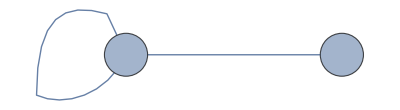
```mathematica
MatrixForm[IGJointDegreeMatrix[-Graphics-],TableHeadings->Automatic]
```

```mathematica
IGJointDegreeMatrix@ExampleData[{"NetworkGraph","ZacharyKarateClub"}]//MatrixPlot
```

The joint degree matrix of a directed graph is not necessarily square.

```mathematica
IGBarabasiAlbertGame[15,3]//IGJointDegreeMatrix//MatrixPlot
```

The second argument allows for obtaining joint degree matrices of a predictable size. This makes it convenient to operate together multiple joint degree matrices.

```mathematica
MatrixPlot@Mean@Table[
IGJointDegreeMatrix[RandomGraph[{10,20}],9,Normalized->True],
{1000}
]
```

#### IGAdjacencyMatrixPlot

```mathematica
?IGAdjacencyMatrixPlot
```

IGAdjacencyMatrixPlot is based on MatrixPlot, but optimized for the convenient display of labelled adjacency matrices.

Available options:

EdgeWeight sets the edge property to use for matrix elements. By default edge weights are used for weighted graphs. Set EdgeWeight→None to visualize the unweighted adjacency matrix even for a weighted graph.

"UnconnectedColor" sets the colour to use to represent non-existent connections.

VertexLabels controls how to label the matrix’s columns and rows. Possible values:

"Index" uses row and column numbers. These are identical to vertex indices when the full adjacency matrix is plotted, but not when a partial matrix is plotted or if the vertices are re-ordered.

"Name" uses vertex names.

Automatic uses indices for large graphs and names for small ones. Use a list of rules to set different names for each vertex.

"RotateColumnLabels"→False will not rotate columns labels.

Mesh controls the drawing of grid lines. By default, a grid is drawn only for small graphs. Use Mesh→All to force drawing the grid.

IGAdjacencyMatrixPlot also accepts all standard MatrixPlot options.

```mathematica
g=ExampleData[{"NetworkGraph","Friendship"}]
```

```mathematica
IGAdjacencyMatrixPlot[g]
```

Reorder graph vertices before plotting.

```mathematica
IGAdjacencyMatrixPlot[g,Sort@VertexList[g]]
```

Plot a subgraph only.

```mathematica
IGAdjacencyMatrixPlot[g,{"Anna","Ben","Larry","Carol"}]
```

Plot a weighted adjacency matrix.

```mathematica
g=ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}];
IGAdjacencyMatrixPlot[g,PlotLegends->Automatic,ImageSize->300]
```

Use a different edge property than weights for the matrix entries.

```mathematica
g2=g//IGEdgeMap[1/#&,EdgeWeight]//
IGEdgeMap[#&,"Betweenness"->IGEdgeBetweenness];
```

```mathematica
IGAdjacencyMatrixPlot[g2,EdgeWeight->"Betweenness",ImageSize->300]
```

Control the style of matrix entries denoting the lack of a connection, to be able to distinguish them from zero entries.

```mathematica
IGAdjacencyMatrixPlot[g2,EdgeWeight->"Betweenness","UnconnectedColor"->Black,ImageSize->300]
```

Plot the adjacency matrix of a very large network.

```mathematica
IGAdjacencyMatrixPlot[ExampleData[{"NetworkGraph","PowerGrid"}]]
```

Large adjacency matrices, like the one above, are downsampled by default to improve readability. This can be controlled using the MaxPlotPoints option.

```mathematica
IGAdjacencyMatrixPlot[ExampleData[{"NetworkGraph","USPoliticsBooks"}],MaxPlotPoints->#]&/@{Automatic,Infinity}
```

The vertex names and the grid are not shown by default for large graphs.

```mathematica
g=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}]
```

```mathematica
IGAdjacencyMatrixPlot[g]
```

Force drawing vertex names and a grid regardless of the matrix size.

```mathematica
IGAdjacencyMatrixPlot[g,VertexLabels->"Name",Mesh->All,ImageSize->440,FrameTicksStyle->Tiny,MeshStyle->Thin]
```

Reorder the adjacency matrix and draw grid lines to show community structure.

```mathematica
cl=IGCommunitiesEdgeBetweenness[g]
```

```mathematica
IGAdjacencyMatrixPlot[g,Catenate@cl["Communities"],Mesh->({#,#}&@FoldList[Plus,0,Length/@cl["Communities"]])]
```

Avoid rotating vertex names when not necessary:

```mathematica
IGAdjacencyMatrixPlot[IGShorthand["A-B-C-D,A-C"],"RotateColumnLabels"->False]
```

Use custom labels for vertices.

```mathematica
g=ExampleData[{"NetworkGraph","SimpleFoodWeb"}]
```

```mathematica
names=Thread[VertexList[g]->(Show[#,ImageSize->20]&/@IGVertexProp[VertexShape][g])]
```

```mathematica
IGAdjacencyMatrixPlot[g,VertexLabels->names,"RotateColumnLabels"->False,ImageSize->Medium,ColorRules->{0->White,1->Black}]
```

#### IGZeroDiagonal

```mathematica
?IGZeroDiagonal
```

IGZeroDiagonal replaces the diagonal of a matrix with zeros. It works on dense and sparse matrices, and supports non-square matrices. This function is particularly useful when constructing adjacency matrices that are to be converted to a graph.

```mathematica
mat=RandomReal[1,{6,4}];
```

```mathematica
IGZeroDiagonal[mat]//MatrixForm
```

Connect those points in the plane whose Euclidean distance is less than 0.2, but do not connect each point with itself.

```mathematica
pts=RandomReal[1,{30,2}];
AdjacencyGraph[
IGZeroDiagonal@UnitStep[0.2-DistanceMatrix[pts]],
VertexCoordinates->pts
]
```

Connect each cell in a rectangular mesh to its Moore neighbours.

```mathematica
arr=RandomInteger[1,{10,10}];
mesh=ArrayMesh[arr]
```

First, generate the square–vertex adjacency matrix.

```mathematica
mat=IGMeshCellAdjacencyMatrix[mesh,2,0]
```

Then find the graph of squares adjacent through a corner point, but excluding self-adjacencies.

```mathematica
AdjacencyGraph[
IGZeroDiagonal@Unitize[mat.Transpose[mat]],
VertexCoordinates->PropertyValue[{mesh,2},MeshCellCentroid],
GraphStyle->"BasicBlack"
]
```

```mathematica
Show[mesh,%]
```

#### IGTakeUpper and IGTakeLower

```mathematica
?IGTakeUpper
```

```mathematica
?IGTakeLower
```

IGTakeUpper and IGTakeLower extract the above-diagonal and below-diagonal elements of a matrix. The matrix does not need to be square. The elements are always extracted row-by-row.

```mathematica
mat=Partition[Range[16],4];
MatrixForm[mat]
```

```mathematica
IGTakeUpper[mat]
```

```mathematica
IGTakeLower[mat]
```

IGTakeUpper and IGTakeLower support sparse matrices. When given a sparse array as input, the result will also be a sparse array.

```mathematica
sa=SparseArray[RandomInteger[{1,6},{10,2}]->RandomInteger[10,10]];
MatrixForm[sa]
```

```mathematica
IGTakeUpper[sa]
```

```mathematica
Normal[%]
```

IGTakeUpper and IGTakeLower are optimized for performance.

```mathematica
mat=RandomReal[1,{1000,1000}];
```

```mathematica
IGTakeUpper[mat];//RepeatedTiming
```

Compute the mean pairwise distance of a random point set.

```mathematica
pts=RandomReal[1,{100,2}];
Mean@IGTakeUpper@DistanceMatrix[pts]
```

## Import and export

IGraph/M provides importers and exporters for certain graph formats.

### Importing

```mathematica
?IGImport
```

Importing is done using IGImport and IGImportString, which work analogously to the built-in Import and ImportString. The supported export formats are listed in $IGImportFormats:

```mathematica
$IGImportFormats
```

#### Nauty / Graph6

The Graph6, Sparse6 and Digraph6 formats are used by the gtools suite included with nauty. IGraph/M refers to this family of formats collectively as the “Nauty formats”. gtools includes many command line programs for generating, transforming and filtering graphs. For more information about gtools, see http://pallini.di.uniroma1.it/

The formal description of these formats is available on the home page of Brendan McKay at https://users.cecs.anu.edu.au/~bdm/data/formats.html.

As of version 12.0, Mathematica has built-in support for Graph6 and Sparse6, but not Digraph6. IGraph/M provides Digraph6, a unified interface to all three formats, as well as significantly better performance.

To convert a single string to a graph, use IGFromNauty.

```mathematica
IGFromNauty["JR_IK?@?I?_"]
```

The purpose of IGImport and IGImportString is to read lists containing several graphs.

```mathematica
IGImportString["
G]kq]K
G]dq\\S
G]Ku]W
G[|akk
GS\\unO
G~`HW{","Graph6"]
```

The following examples assume that the gtools programs are in a directory that is on the operating system’s PATH environment variable. If necessary, specify the full path to each program.

```mathematica
If[StringFreeQ[Environment["PATH"],"/opt/local/bin"],SetEnvironment["PATH"->Environment["PATH"]<>":/opt/local/bin"]
];
```

Generate all non-isomorphic undirected graphs on 4 vertices.

```mathematica
IGImport["!geng 4","Nauty"]
```

Generate all non-isomorphic directed graphs on 3 vertices.

```mathematica
IGImport["!geng 3 | directg","Graph6",GraphLayout->"CircularEmbedding"]
```

Find all non-isomorphic cactus graphs on 5 vertices. A cactus on V vertices has between V-1 and 3 (V-1)/2 edges. Thus we instruct the geng program to only generate connected graphs with an edge count in this range.

```mathematica
Select[
IGImport["!geng -c 5 4:6","Graph6",GraphStyle->"Minimal"],
IGCactusQ
]
```

Generate all strongly connected tournaments on 5 vertices.

```mathematica
IGImport["!gentourng -c 5 -z","Graph6"]
```

### Exporting

```mathematica
?IGExport
```

Exporting is done using IGExport and IGExportString, which work analogously to the built-in Export and ExportString. The supported export formats are listed in $IGExportFormats:

```mathematica
$IGExportFormats
```

#### GraphML

As of Mathematica 12.0, the built-in Export function produces non-standard GraphML files that cannot be read by some other graph manipulation packages, such as the igraph library itself. IGExport provides a standards-compliant implementation.

```mathematica
IGExportString[
ExampleData[{"NetworkGraph","EurovisionVotes"}],
"GraphML"
]//Short[#,15]& (* avoid showing more than 15 lines *)
```

## Utility functions

### Structural transformations

#### IGUndirectedGraph

```mathematica
?IGUndirectedGraph
```

IGUndirectedGraph[g, method] converts a directed graph to an undirected one, using the specified edge conversion method:

"Simple" creates a single undirected edge between connected vertices

"All" creates one undirected edge for each directed one. This may result in multiple edges between the same vertices.

"Mutual" creates an edge only between mutually connected vertices.

If the graph was already undirected, it will not be changed.

IGUndirectedGraph is guaranteed to preserve both the vertex names and the vertex ordering of the original graph. The built-in UndirectedGraph has a bug where it sometimes relabels vertices.

Warning: As of IGraph/M 0.3, IGUndirectedGraph discards graph properties such as edge weights.

```mathematica
g=-Graphics-;
```

```mathematica
IGUndirectedGraph[g,#]&/@{"Simple","All","Mutual"}
```

The default method is "Simple":

```mathematica
IGUndirectedGraph[g]
```

Self-loops are preserved by all methods:

```mathematica
IGUndirectedGraph[Graph[{1,2},{1->1,1->2}],#]&/@{"Simple","All","Mutual"}
```

#### IGReverseGraph

```mathematica
?IGReverseGraph
```

In Mathematica 11.3 and earlier, ReverseGraph does not correctly transfer graph properties such as edge weights to the result.

IGReverseGraph reverses the direction of each edge while preserving the following graph properties: EdgeWeight, EdgeCapacity, EdgeCost, VertexWeight, VertexCapacity. Other properties are discarded.

Undirected graphs are returned unmodified.

As of IGraph/M 0.3.0, IGReverseGraph does not support multigraphs.

#### IGSimpleGraph

```mathematica
?IGSimpleGraph
```

IGSimpleGraph removes self-loops and collapses multi-edges into simple ones, as specified in the options.

The available options are:

SelfLoops→True keeps self-loops in the graph.

MultiEdges→True keeps parallel edges in the graph.

```mathematica
IGSimpleGraph[-Graphics-,SelfLoops->#1,MultiEdges->#2]&@@@{{True,True},{True,False},{False,True},{False,False}}
```

#### IGDisjointUnion

```mathematica
?IGDisjointUnion
```

IGDisjointUnion will combine the given graphs into a single graph having them as its connected components.

IGDisjointUnion differs from the built-in GraphDisjointUnion in several ways.

IGDisjointUnion takes the input graphs in a list instead of as separate arguments. It can also take graph options to apply to the final graph.

```mathematica
IGDisjointUnion[{TuranGraph[8,2],TuranGraph[6,3]},
EdgeStyle->Black,VertexStyle->Directive[FaceForm[RGBColor[0.254906, 0.411802, 0.882397]],EdgeForm@Directive[Thick,GrayLevel[1, 1]]],VertexSize->Medium]
```

IGDisjointUnion is considerably faster than GraphDisjointUnion when combining moderately sized networks.

```mathematica
graphs=RandomGraph[{300,600},30];
```

```mathematica
IGDisjointUnion[graphs];//RepeatedTiming
```

```mathematica
GraphDisjointUnion@@graphs;//RepeatedTiming
```

IGDisjointUnion does not support mixed graphs.

```mathematica
IGDisjointUnion[{Graph[{1<->2}],Graph[{1->2}]}]
```

Use GraphDisjointUnion instead.

```mathematica
GraphDisjointUnion[Graph[{1<->2}],Graph[{1->2}]]
```

IGDisjointUnion will use vertex names of the form {gi,v}, where gi is an identifier of the original graph and v is the original name of the vertex. When the input is a list gi is the index of the original graph. When the input is an association, gi is its key.

In contrast, GraphDisjointUnion uses consecutive integers as vertex names. Use IndexGraph to obtain a similar result from the output of IGDisjointUnion.

```mathematica
g=IGDisjointUnion[<|"a"->CycleGraph[4],"b"->StarGraph[4]|>];
VertexList[g]
```

This allows for convenient further manipulation, or for copying over arbitrary properties stored in the original graphs.

```mathematica
Graph[g,VertexStyle->{{"a",_}->Green,{"b",_}->Red}]
```

```mathematica
graphs={
Graph[{Property[1->2,"length"->5]}],
Graph[{Property[1->2,"length"->3],Property[3->2,"length"->2]}]
};
IGDisjointUnion[graphs,
Properties->{{gi_,v1_}->{gi_,v2_}:>{"length"->PropertyValue[{graphs⟦gi⟧,v1->v2},"length"]}}]
```

```mathematica
IGEdgeProp["length"][%]
```

IGDisjointUnion is also practically useful for simply showing many small graphs together.

```mathematica
IGDisjointUnion[
Select[IGGraphAtlas/@Range[2,150],IGConnectedQ],
GraphStyle->"BasicBlue",VertexSize->1
]
```

```mathematica
g=IndexGraph[%]; (* workaround for highlighting in Mathematica ≤ 11.2 *)
HighlightGraph[IGLayoutFruchtermanReingold[g],ConnectedGraphComponents[g]]
```

#### IGOrientTree

```mathematica
?IGOrientTree
```

IGOrientTree creates an out-tree (also called an arborescence) out of an undirected tree. Graph properties are preserved, but the vertex ordering of the graph is changed.

```mathematica
g=KaryTree[10,3,VertexLabels->"Name"]
```

```mathematica
IGOrientTree[g,1]
```

```mathematica
IGOrientTree[g,5,GraphLayout->"LayeredDigraphEmbedding"]
```

The result is an out-tree, also called an arborescence.

```mathematica
IGTreeQ[%,"Out"]
```

Once the tree is made directed, it is easy to find its root and leaf nodes:

```mathematica
{IGSourceVertexList[%],IGSinkVertexList[%]}
```

Edges can be oriented towards or away from the root.

```mathematica
t=IGTreeGame[7,VertexLabels->Automatic]
```

```mathematica
IGOrientTree[t,4,#,GraphLayout->{"LayeredEmbedding","RootVertex"->4}]&/@{"In","Out"}
```

#### IGTakeSubgraph

```mathematica
?IGTakeSubgraph
```

IGTakeSubgraph[graph, subgraph] will effectively transfer graph properties of a larger graph onto its specified subgraph. It can be used in conjunction with other graph subsetting functions that do not retain some or all graph properties, such as Subgraph, VertexDelete, NeighborhoodGraph, etc.

If only the edge weights need to be preserved, use IGWeightedSubgraph when possible. It offers better performance.

Take a subgraph of a larger graph while preserving all graph properties, including styling attributes.

```mathematica
g=ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}]
```

```mathematica
IGTakeSubgraph[g,Subgraph[g,{"Osama","Salim","Abdullah","Hage","Abouhlaima","Owhali"}]]
```

Show the neighbourhood graph of a vertex while preserving vertex shapes.

```mathematica
g=ExampleData[{"NetworkGraph","SimpleFoodWeb"}]
```

```mathematica
IGTakeSubgraph[g,NeighborhoodGraph[g,"Sunflower"]]
```

Take a subgraph of a mesh graph while preserving vertex coordinates.

```mathematica
g=IGMeshGraph[DelaunayMesh@RandomReal[1,{10,2}],VertexLabels->"Name"]
```

```mathematica
IGTakeSubgraph[g,First@FindHamiltonianCycle[g]]
```

### Other utility functions

#### IGIndexEdgeList

```mathematica
?IGIndexEdgeList
```

IGIndexEdgeList is useful for implementing graph processing functions in Mathematica, and is used internally by many IGraph/M functions that do not call the igraph library.

```mathematica
IGIndexEdgeList[Graph[{a,b,c},{b<->c,c<->a}]]
```

```mathematica
Developer`PackedArrayQ[%]
```

IGIndexEdgeList[g] is faster than EdgeList[g] and usually much faster than EdgeList@IndexGraph[g].

```mathematica
g=ExampleData[{"NetworkGraph","CondensedMatterCollaborations"}];
```

```mathematica
{First@RepeatedTiming@EdgeList[g],
First@RepeatedTiming@EdgeList@IndexGraph[g],
First@RepeatedTiming@IGIndexEdgeList[g]}
```

```mathematica
List@@@Sort/@EdgeList@IndexGraph[g]===Sort/@IGIndexEdgeList[g]
```

A graph can be directly re-built from an index-based edge list.

```mathematica
Graph[{a,b,c},{{2,3},{1,3}}]
```

#### IGPartitionsToMembership and IGMembershipToPartitions

```mathematica
?IGPartitionsToMembership
```

```mathematica
?IGMembershipToPartitions
```

A partitioning of a set of elements can be represented in multiple ways. One way is to list the members of each partition. Another is to annotate each element with the index of the partition it belongs to, i.e. construct a “membership vector”. These functions convert between these representations.

IGraph/M generally uses disjoint subsets to represents partitions. Membership vectors are useful when storing the membership information as vertex attributes, or when exchanging data with other interfaces of igraph.

```mathematica
IGPartitionsToMembership[{a,b,c,d},{{a,c},{d,b}}]
```

```mathematica
IGMembershipToPartitions[{a,b,c,d},{1,2,1,2}]
```

If the given partitions do not cover the element set, the missing elements will be marked with 0 in the membership vector.

```mathematica
IGPartitionsToMembership[{a,b,c,d},{{a},{b,d}}]
```

The following graph has the type of nodes encoded as a vertex attribute.

```mathematica
g=ExampleData[{"NetworkGraph","BipartiteDiseasomeNetwork"}];
IGVertexProp["Type"][g]//Short
```

Let us extract the attribute values as a vector and construct the two vertex partitions.

```mathematica
parts=IGMembershipToPartitions[g,IGVertexProp["Type"][g]];
```

Verify that the graph is bipartite according to this partitioning.

```mathematica
IGBipartiteQ[g,parts]
```

Annotate the vertices of a bipartite graph with their computed membership value.

```mathematica
g=IGBipartiteGameGNM[5,6,14,VertexSize->Large];
```

```mathematica
g=IGVertexMap[
#&,
"membership"->IGPartitionsToMembership[VertexList[g]]@*IGBipartitePartitions,
g
];
```

Colour the vertices accordingly.

```mathematica
IGVertexMap[ColorData[100],VertexStyle->IGVertexProp["membership"],g]
```

Visualize a vertex colouring using HighlightGraph.

```mathematica
g=IGSquareLattice[{2,2,2,2},"Periodic"->True]
```

```mathematica
HighlightGraph[
g,IGMembershipToPartitions[g,IGVertexColoring[g]],
VertexSize->Medium,GraphHighlightStyle->"DehighlightGray"
]
```

#### IGReorderVertices

```mathematica
?IGReorderVertices
```

IGReorderVertices changes the order in which graph vertices are stored. The graph itself is not modified, only its representation. The ordering of vertices affects how several of Mathematica’s graph processing functions work.

Let us use a styled graph for illustration, to demonstrate that graph properties are preserved.

```mathematica
g1=RandomGraph[{5,5},VertexStyle->{1->LightRed,3->LightGreen},VertexSize->Medium,VertexLabels->Placed[Automatic,Center]]
```

```mathematica
g2=IGReorderVertices[{5,4,3,2,1},g1]
```

```mathematica
VertexList/@{g1,g2}
```

```mathematica
IGIsomorphicQ[g1,g2]
```

The result of certain operations, such as DirectedGraph[…,"Acyclic"] or AdjacencyMatrix, depends on the vertex ordering.

```mathematica
DirectedGraph[#,"Acyclic"]&/@{g1,g2}
```

Order the vertices of a directed acyclic graph so that its adjacency matrix is upper triangular.

```mathematica
g=RandomGraph[{10,30},DirectedEdges->True];
g=EdgeDelete[g,IGFeedbackArcSet[g]];
ArrayPlot/@AdjacencyMatrix/@{g,IGReorderVertices[TopologicalSort[g],g]}
```

Visualize a graph so that a Hamiltonian cycle is on a circle.

```mathematica
g=GraphData["DodecahedralGraph"];
IGLayoutCircle@IGReorderVertices[FindHamiltonianCycle[g][[1,All,1]],g]
```

Change the order how graph vertices are drawn in a circular layout without discarding any styling or other properties.

```mathematica
g=IGLayoutCircle[
ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],
VertexLabels->(_->Placed["Name",Tooltip])
]
```

```mathematica
IGLayoutCircle@IGReorderVertices[RandomSample@VertexList[g],g]
```

Reorder the vertices of a bipartite graph to make the bipartite structure explicit in its adjacency matrix. Note that if the goal is simply visualizing the adjacency matrix, IGAdjacencyMatrixPlot can be used instead.

```mathematica
g=CycleGraph[10];
ArrayPlot/@AdjacencyMatrix/@{g,IGReorderVertices[Flatten@IGBipartitePartitions[g],g]}
```

Order the vertices of a graph by increasing degree.

```mathematica
g=RandomGraph[{20,40}];
{IGLayoutCircle[g],IGLayoutCircle@IGReorderVertices[VertexList[g]⟦Ordering@VertexDegree[g]⟧,g]}
```

#### IGAdjacencyList

```mathematica
?IGAdjacencyList
```

IGAdjacencyList returns the adjacency list of a graph as an association. This is often a more useful format than what the built-in AdjacencyList provides.

```mathematica
IGAdjacencyList[Graph[{1<->2}]]
```

For directed graphs, only outgoing edges are considered when building the adjacency list. In contrast, the built-in AdjacencyList ignores edge directions.

```mathematica
IGAdjacencyList[Graph[{1->2}]]
```

```mathematica
AdjacencyList[Graph[{1->2}]]
```

Consider incoming edges instead.

```mathematica
IGAdjacencyList[Graph[{1->2}],"In"]
```

Consider both incoming and outgoing edges.

```mathematica
IGAdjacencyList[Graph[{1->2}],"All"]
```

With this option, reciprocal edges are considered individually in directed graphs.

```mathematica
IGAdjacencyList[Graph[{1->2,2->1}],"All"]
```

Multi-edges and self-loops are supported. In contrast, the built-in AdjacencyList ignores them.

```mathematica
IGAdjacencyList[Graph[{1->2,1->2,2->2,2->2}]]
```

```mathematica
AdjacencyList[Graph[{1->2,1->2,2->2}]]
```

Self-loops are traversed in only one direction in undirected graphs. Thus the result of the below is not <|1→{1,1}|> but simply <|1→{1}|>.  This is consistent with AdjacencyMatrix, but not with VertexDegree.

```mathematica
IGAdjacencyList[Graph[{1<->1}]]
```

IGAdjacencyList can be used to find the parent of each node in a rooted tree. The root itself will have no parent.

```mathematica
IGAdjacencyList[-Graphics-,"In"]
```

Find the children of each node.

```mathematica
IGAdjacencyList[-Graphics-,"Out"]
```

#### IGAdjacencyGraph

```mathematica
?IGAdjacencyGraph
```

IGAdjacencyGraph can convert an adjacency matrix or an adjacency list representation of a graph into a Graph expression. When given a matrix, it behaves equivalently to the built-in function AdjacencyGraph.

The available options are:

DirectedEdges→True and DirectedEdges→False create a directed or undirected graph, respectively. The default setting is DirectedEdges→Automatic, which creates an undirected graph when this is consistent with the given adjacency matrix or adjacency list.

Compute the adjacency list of a graph, then convert it back to a Graph expression.

```mathematica
g=RandomGraph[{5,6},DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
IGAdjacencyList[g]
```

```mathematica
IGAdjacencyGraph[%]
```

The representation of combinatorial embeddings used by IGraph/M is also a valid adjacency list.

```mathematica
IGPlanarEmbedding@CompleteGraph[4]
```

```mathematica
IGAdjacencyGraph[%]
```

## Built-in data

### Graph data

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order that motif counting functions use.

```mathematica
?IGData
```

```mathematica
IGData[]
```

These are all size 3 directed graphs.

```mathematica
IGData[{"AllDirectedGraphs",3}]//Map[Framed@Labeled[Graph[#,ImageSize->50],IGIsoclass[#]]&]//Multicolumn
```

"MANTriadLabels" refers to the mutual, asymmetric, null labelling of triads used by IGTriadCensus[]. Each label is mapped to the corresponding graph, ordered based on their IGIsoclass. This is useful for converting the output of IGTriadCensus[] to a format compatible with IGMotifs[].

```mathematica
g=RandomGraph[{20,50},DirectedEdges->True];
{IGMotifs[g,3],Lookup[IGTriadCensus[g],Keys@IGData["MANTriadLabels"]]}//Grid
```

The IGGraphAtlas function provides access to the graphs listed in An Atlas of Graphs by Ronald C. Read and Robin J. Wilson, Oxford University Press, 1998.

```mathematica
?IGGraphAtlas
```

```mathematica
IGGraphAtlas[341]
```

Finally, remember that Mathematica itself comes with a large database of graphs and their properties, accessible through GraphData.

### Lattice data

The IGLatticeMesh function includes a set of pre-defined two-dimensional lattice structures. Evaluate IGLatticeMesh[] to get the list of available lattices.

The data used by IGMeshGraph was sourced from Wolfram|Alpha and Mathematica’s curated data system in April 2018.

```mathematica
?IGLatticeMesh
```

```mathematica
IGLatticeMesh[]
```

## IGraph/M system functions

### The random number generator

IGraph/M makes use of Mathematica’s own random number generator by default, thus functions like SeedRandom and BlockRandom have the expected effect.

```mathematica
SeedRandom[137]
Table[BlockRandom@IGErdosRenyiGameGNM[6,9],{3}]
```

BlockRandom is useful for example to get consistent graph layouts without affecting subsequent uses of the random number generator.

```mathematica
g=RandomGraph[{100,150}];
Table[IGLayoutFruchtermanReingold[g],{4}]
```

```mathematica
Table[BlockRandom[SeedRandom[1234];IGLayoutFruchtermanReingold[g]],{4}]
```

IGraph/M can be configured to either use Mathematica’s built-in generator, or the default generator of the core igraph C library. The default generator of igraph will perform better, but it does not react to BlockRandom and must be seeded with IGSeedRandom (not with SeedRandom).

Benchmark IGRandomWalk when using Mathematica’s random number generator:

```mathematica
g=IGGiantComponent@RandomGraph[{1000,2000}];
```

```mathematica
IGRandomWalk[g,1,10000000];//RepeatedTiming
```

Benchmark it with igraph’s default generator:

```mathematica
IGSeedRandom[Method->"igraph"]
IGRandomWalk[g,1,10000000];//RepeatedTiming
```

Set the generator back to Mathematica’s:

```mathematica
IGSeedRandom[Method->"Mathematica"]
```

#### IGSeedRandom

```mathematica
?IGSeedRandom
```

Available Method option values are:

"Mathematica" uses Mathematica’s built-in random number generator. With this choice, functions like SeedRandom and BlockRandom will IGraph/M functions as expected. Performance is not as good as with the "igraph" generator

"igraph" uses the core igraph C library’s random number generator. SeedRandom and BlockRandom have no effect on this generator. Seeding can be done with IGSeedRandom. Performance is better than with the "Mathematica" generator.

### Library version

The following symbols and functions can be used to retrieve the IGraph/M version.

```mathematica
?IGVersion
```

```mathematica
IGVersion[]
```

```mathematica
?IGraphM`Information`$Version
```

```mathematica
IGraphM`Information`$Version
```

### Support and troubleshooting

If you find a problem with IGraph/M, please report it through the GitHub issue tracker or the Gitter chatroom. Always include the output of the GetInfo[] function with problem reports.

```mathematica
?IGraphM`Developer`GetInfo
```

## Acknowledgements

Most functions in IGraph/M are based on the igraph C library, written by Gábor Csárdi and Tamás Nepusz. To cite the igraph C library in publications, see Citing igraph in the igraph Reference Manual. Website: http://igraph.org/

Some functions, in particular in the area of planar graphs, use the LEMON graph library. Website: https://lemon.cs.elte.hu/

Some proximity graph functions make use of the nanoflann library. Website: https://github.com/jlblancoc/nanoflann

IGraph/M was developed with the Wolfram Language Plugin for IntelliJ IDEA by Patrick Scheibe. Without the help of this IDE, it would have been difficult to manage the complexity of this package. Website: http://wlplugin.halirutan.de/

The help of the Mathematica StackExchange community was invaluable while developing this package.

People who have contributed to IGraph/M:

Szabolcs Horvát (main author and maintainer)

Henrik Schumacher (help with mesh-graph conversion and proximity graph functions)

Juho Lauri (advice with the implementation of graph colouring functions)

To cite IGraph/M in a publication, please refer to doi:10.5281/zenodo.1134932